```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/phase_space_stoc/PDF_zetaR/math"]
```

/Users/yuichirotada/Documents/Univ/phase_space_stoc/PDF_zetaR/math

```mathematica
Integrate[1/2 EllipticTheta[2,-π/2(x-1),E^(-π^2 NN/μ^2)]-1/2 EllipticTheta[2,-π/2(x+1),E^(-π^2 NN/μ^2)],{NN,0,∞}]
```

$Aborted

```mathematica
1/2 EllipticTheta[2,-π/2(x-1),E^(-π^2 NN/μ^2)]-1/2 EllipticTheta[2,-π/2(x+1),E^(-π^2 NN/μ^2)]-EllipticTheta[1,π x/2,E^(-π^2 NN/μ^2)]//FunctionExpand
```

-EllipticTheta[1,(π x)/2,ⅇ^(-(NN π^2)/μ^2)]+1/2 EllipticTheta[2,-1/2 π (-1+x),ⅇ^(-(NN π^2)/μ^2)]-1/2 EllipticTheta[2,-1/2 π (1+x),ⅇ^(-(NN π^2)/μ^2)]

```mathematica
EllipticTheta[2,z+π/2,q]-EllipticTheta[1,-z,q]//FullSimplify
```

-EllipticTheta[1,-z,q]+EllipticTheta[2,π/2+z,q]

```mathematica
Integrate[EllipticTheta[1,π/2 x,E^(-π^2 NN/μ^2)],{NN,0,∞}]
```

$Aborted

```mathematica
Integrate[EllipticTheta[1,π/2 x,a]/a,{a,0,1},Assumptions->{0<x<1}]
```

Integrate[EllipticTheta[1,(π x)/2,a]/a,{a,0,1},Assumptions→{0<x<1}]

### plot

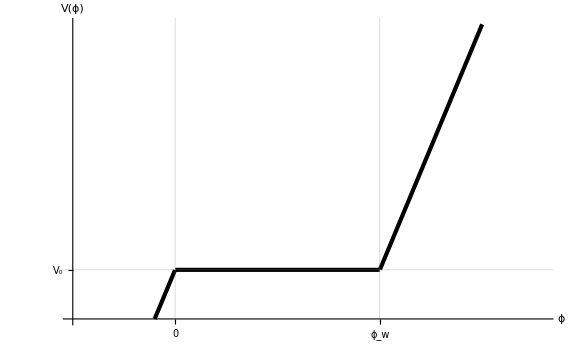

```mathematica
Plot[10x UnitStep[-x]+10(x-1)UnitStep[x-1],{x,-0.1,1.8},Frame->False,AxesStyle->Directive[Black,Thick],Ticks->{{0,{1,Subscript[ϕ, "w"]}},{{0,Subscript[V, 0]}}},AxesLabel->{ϕ,V[ϕ]},PlotStyle->{AbsoluteThickness[3],Black},AxesOrigin->{-0.5,-1},PlotRange->{-1,5},GridLines->{{0,1},{0}}]
```

### quadratic

```mathematica
v[x_]=1/(24 π^2)1/2 m^2 x^2;
v0=v[1];
xend=Sqrt[2];
alpha[t_]=Sqrt[1-(4I t)/v0];
```

```mathematica
chiN[t_,x_]=(v[x]/v[xend])^((1-alpha[t])/4)Hypergeometric1F1[(alpha[t]-1)/4,1+alpha[t]/2,-1/v[x]]/Hypergeometric1F1[(alpha[t]-1)/4,1+alpha[t]/2,-1/v[xend]]//Simplify
```

(2^(1/4 (-1+√(1-(192 ⅈ π^2 t)/m^2))) (x^2)^(1/4 (1-√(1-(192 ⅈ π^2 t)/m^2))) Hypergeometric1F1[1/4 (-1+√(1-(192 ⅈ π^2 t)/m^2)),1+1/2 √(1-(192 ⅈ π^2 t)/m^2),-(48 π^2)/(m^2 x^2)])/Hypergeometric1F1[1/4 (-1+√(1-(192 ⅈ π^2 t)/m^2)),1+1/2 √(1-(192 ⅈ π^2 t)/m^2),-(24 π^2)/m^2]

```mathematica
chiN[-I t,Sqrt[4 60+2]]/.{m->10^-5}//Simplify
```

(11^(1/2-1/2 √(1-1920000000000 π^2 t)) Hypergeometric1F1[1/4 (-1+√(1-1920000000000 π^2 t)),1/2 (2+√(1-1920000000000 π^2 t)),-(240000000000 π^2)/121])/Hypergeometric1F1[1/4 (-1+√(1-1920000000000 π^2 t)),1/2 (2+√(1-1920000000000 π^2 t)),-240000000000 π^2]

```mathematica
v0/.{m->10}//N
```

0.211086

```mathematica
chiN[-I 0.1,Sqrt[4 60+2]]^-1/.{m->10}
```

0.278937+0.258808 ⅈ

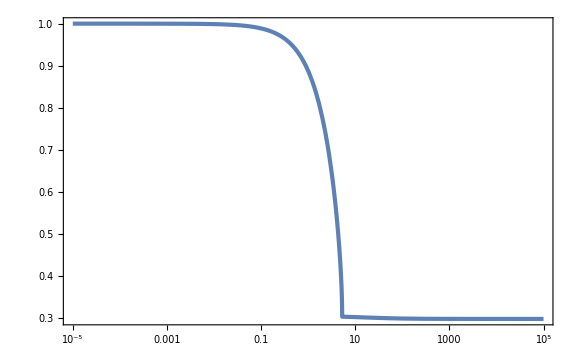

```mathematica
LogLinearPlot[{Abs[chiN[-I t,Sqrt[4 60+2]]^-1/.{m->10^2}//Simplify]},{t,10^-5,10^5},WorkingPrecision->30,PlotRange->Full]
```

### flat well

```mathematica
Ptail[z_,n_]:=π^2/4 NIntegrate[x/(1-x)^2 EllipticThetaPrime[2,π/2 x,E^(-π^2 n)]EllipticThetaPrime[2,π/2,E^(-π^2/(1-x)^2(z+(1-x)^2/2))]UnitStep[z+(1-x)^2/2],{x,0,1},WorkingPrecision->30]
```

```mathematica
Ptail[-0.8,1/4]
```

NIntegrate::precw: The precision of the argument function ((x EllipticThetaPrime[2,π/2,ⅇ^(-(π^2 (-0.8+1/2 («1»)^2))/(1-x)^2)] EllipticThetaPrime[2,(π x)/2,ⅇ^(-π^2/4)] UnitStep[-0.8+1/2 (1-x)^2])/(1-x)^2) is less than WorkingPrecision (30.).

0.

```mathematica
PtailList14=Table[{z,Ptail[z,1/4]},{z,-1+1/200,10,1/100}];//AbsoluteTiming
(*PtailList1=Table[{z,Ptail[z,1]},{z,-1+1/200,10,1/100}];//AbsoluteTiming*)
PtailList2=Table[{z,Ptail[z,2]},{z,-1+1/200,10,1/100}];//AbsoluteTiming
PtailList4=Table[{z,Ptail[z,4]},{z,-1+1/200,10,1/100}];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00159577513134611906569509945135}. NIntegrate obtained 6.32332124135865226337959712107×10^-31 and 1.25392329887667469083130379044×10^-40 for the integral and error estimates.

{51.8592,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00159577513134611906569509945135}. NIntegrate obtained 7.91481046230413119974695260681×10^-33 and 1.56951988791291822485085446433×10^-42 for the integral and error estimates.

{48.4235,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00159577513134611906569509945135}. NIntegrate obtained 5.69223936283654596148848844011×10^-35 and 1.12878039585193788092355258707×10^-44 for the integral and error estimates.

{42.8308,Null}

```mathematica
Normal[Series[EllipticThetaPrime[2,π/2,ϵ E^(-π^2/2)],{ϵ,0,1}]]
```

-2 ⅇ^(-π^2/8) ϵ^(1/4)

```mathematica
Normal[Series[x/(1-x)^2 EllipticThetaPrime[2,π/2 x,E^(-π^2 n)]EllipticThetaPrime[2,π/2,ϵ E^(-π^2/2)],{ϵ,0,1},{x,0,2}]]
```

-ⅇ^(-π^2/8) π x^2 ϵ^(1/4) EllipticThetaPrime^(0,1,0)[2,0,ⅇ^(-n π^2)]

```mathematica
Normal[Series[x/(1-x)^2 EllipticThetaPrime[2,π/2 x,E^(-π^2 n)],{ϵ,0,1},{x,0,2}]]
```

1/2 π x^2 EllipticThetaPrime^(0,1,0)[2,0,ⅇ^(-n π^2)]

```mathematica
Normal[Series[-(π^2 z)/(4(1-x)^2),{x,0,1}]]
```

-(π^2 z)/4-1/2 π^2 x z

```mathematica
Ptailapproxac[z_,n_]=π^2/4 Integrate[Normal[Series[x/(1-x)^2 EllipticThetaPrime[2,π/2 x,E^(-π^2 n)]EllipticThetaPrime[2,π/2,ϵ E^(-π^2/2)],{ϵ,0,1},{x,0,2}]]/.{ϵ^(1/4)->Exp[Normal[Series[-(π^2 z)/(4(1-x)^2),{x,0,1}]]]},{x,0,1}]
```

(ⅇ^(-1/8 π^2 (1+6 z)) (8-8 ⅇ^((π^2 z)/2)+π^2 z (4+π^2 z)) EllipticThetaPrime^(0,1,0)[2,0,ⅇ^(-n π^2)])/(2 π^3 z^3)

```mathematica
Ptailapprox[z_,n_]=-4(E^(-π^2/8))/π^3 D[EllipticThetaPrime[2,x,E^(-n π^2)], x](E^(-π^2/4 z))/z^3/.{x->0}
```

-(4 ⅇ^(-π^2/8-(π^2 z)/4) EllipticThetaPrime^(0,1,0)[2,0,ⅇ^(-n π^2)])/(π^3 z^3)

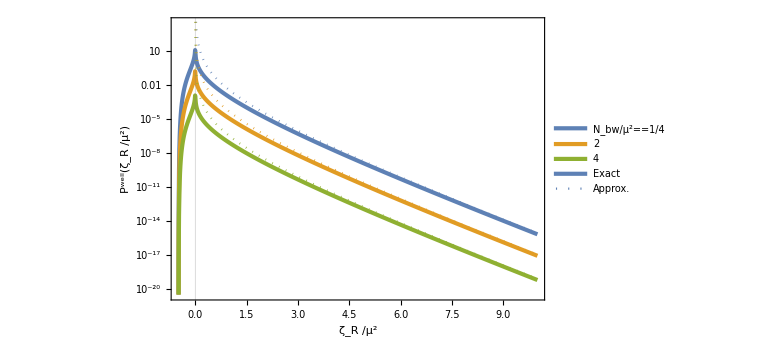

```mathematica
Show[ListLogPlot[{PtailList14,PtailList2,PtailList4,{{0,0},{1,0}},{{0,0},{1,0}}},PlotRange->{10^-20.5,10^3.5},FrameLabel->{Row[{Subscript[ζ, R]," /",μ^2}],(P^("well"))[Row[{Subscript[ζ, R]," /",μ^2}]]},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{Row[{Subscript[N, bw],"/",μ^2}]=="1/4",2,4,"Exact","Approx."},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Row",2}],{0.72,0.82}],GridLines->{{0},None}],LogPlot[{Ptailapprox[z,1/4],Ptailapprox[z,2],Ptailapprox[z,4]},{z,0,10},PlotStyle->Dotted]]
```

```mathematica
PtailList14long=Table[{z,Ptail[z,1/4]},{z,-1+1/200,5,1/10}];//AbsoluteTiming
PtailList1long=Table[{z,Ptail[z,1]},{z,-1+1/200,5,1/10}];//AbsoluteTiming
PtailList2long=Table[{z,Ptail[z,2]},{z,-1+1/200,5,1/10}];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00159577513134611906569509945135}. NIntegrate obtained 6.32332124135865226337959712107×10^-31 and 1.25392329887667469083130379044×10^-40 for the integral and error estimates.

{2.56144,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00159577513134611906569509945135}. NIntegrate obtained 9.33295586596598090159616084863×10^-32 and 1.85074044595315254280560982439×10^-41 for the integral and error estimates.

{2.09952,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00159577513134611906569509945135}. NIntegrate obtained 7.91481046230413119974695260681×10^-33 and 1.56951988791291822485085446433×10^-42 for the integral and error estimates.

{2.3936,Null}

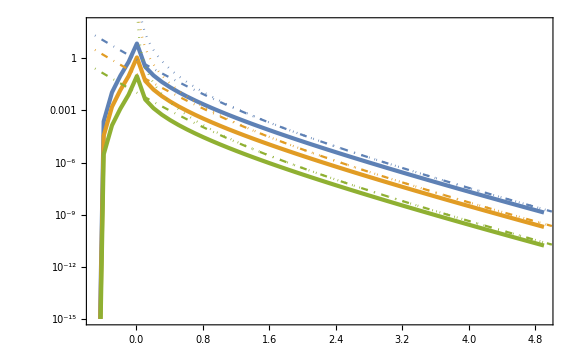

```mathematica
Show[ListLogPlot[{PtailList14long,PtailList1long,PtailList2long},PlotRange->{10^-15,10^2}],LogPlot[{Ptailapprox[z,1/4],Ptailapprox[z,1],Ptailapprox[z,2]},{z,-0.5,5},PlotStyle->Dotted],LogPlot[{Ptailapproxac[z,1/4],Ptailapproxac[z,1],Ptailapproxac[z,2]},{z,-0.5,5},PlotStyle->DotDashed]]
```

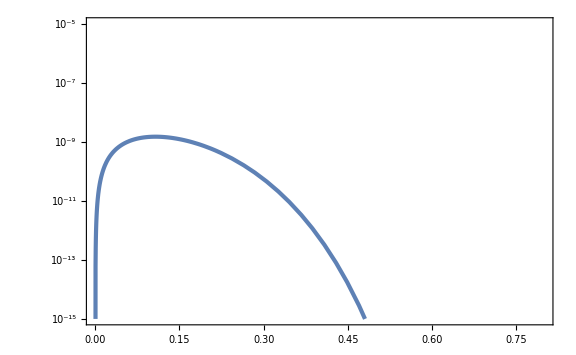

```mathematica
LogPlot[x/(1-x)^2 EllipticThetaPrime[2,π/2 x,E^(-π^2 n)]EllipticThetaPrime[2,π/2,E^(-π^2/(1-x)^2(z+(1-x)^2/2))]/.{n->3,z->3},{x,0,1},PlotRange->{10^-15,10^-5}]
```

```mathematica
TrigToExp[Simplify[Normal[Series[x EllipticThetaPrime[2,π/2 x,1-a],{a,0,0}]],{a>0}]]
```

((-4+a) (-12+6 a+a^2) ⅇ^(((-12+6 a+a^2) π^2 x^2)/(48 a)) π^(3/2) x (2 ⅇ^(1/12 (6-12/a+a) π^2) (-ⅇ^(-1/12 (6-12/a+a) π^2 x)+ⅇ^(1/12 (6-12/a+a) π^2 x))-x+ⅇ^(1/12 (6-12/a+a) π^2) (ⅇ^(-1/12 (6-12/a+a) π^2 x)+ⅇ^(1/12 (6-12/a+a) π^2 x)) x))/(48 a^(3/2))

```mathematica
48 ⅇ^((-12 π^2 x^2)/(48 a)) π^(3/2) x (2 ⅇ^(1/12(-12/a) π^2) (-ⅇ^(-1/12 (-12/a) π^2 x)+ⅇ^(1/12 (-12/a) π^2 x))-x+ⅇ^(1/12 (-12/a) π^2) (ⅇ^(-1/12 (-12/a) π^2 x)+ⅇ^(1/12 (-12/a) π^2 x)) x)//FullSimplify
```

48 ⅇ^(-(π^2 (2+x)^2)/(4 a)) π^(3/2) x (2+ⅇ^((2 π^2 x)/a) (-2+x)+x-ⅇ^((π^2 (1+x))/a) x)

```mathematica
48 ⅇ^(-(π^2 (2+x)^2)/(4 a)) π^(3/2) x (-ⅇ^((π^2 (1+x))/a) x)//Simplify
```

-48 ⅇ^(-(π^2 x^2)/(4 a)) π^(3/2) x^2

```mathematica
FullSimplify[1/μ^2 D[(1/2 EllipticTheta[2,-π/2(x-xi),e]-1/2 EllipticTheta[2,-π/2(x+xi),e]), x]/.{x->0},{xi>0,e>0}]
```

(π (EllipticThetaPrime[2,-(π xi)/2,e]-EllipticThetaPrime[2,(π xi)/2,e]))/(4 μ^2)

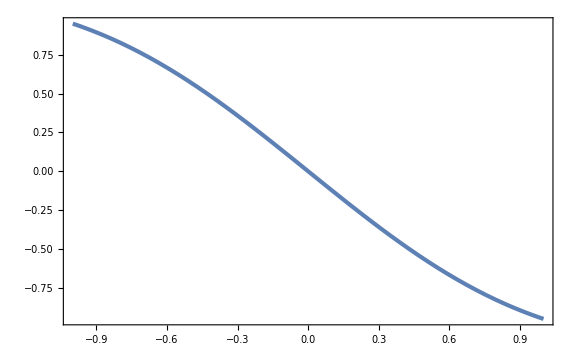

```mathematica
Plot[EllipticThetaPrime[2,z,1/10],{z,-1,1}]
```

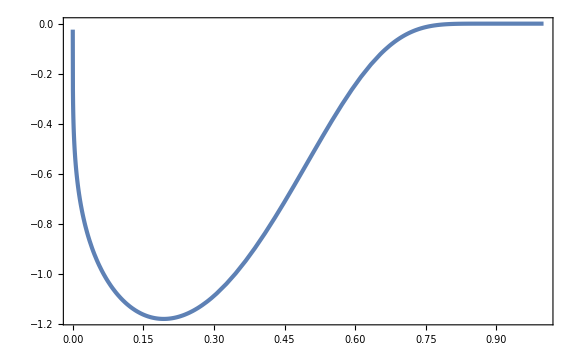

```mathematica
Plot[EllipticThetaPrime[2,π/2,x],{x,0,1}]
```

```mathematica
Normal[Series[EllipticThetaPrime[2,π/2 x,ϵ],{x,1,1}]]
```

EllipticThetaPrime[2,π/2,ϵ]+1/2 π (-1+x) EllipticThetaPrime^(0,1,0)[2,π/2,ϵ]

```mathematica
Integrate[x/(1-x)^2,{x,0,1}]
```

Integrate::idiv: Integral of x/(-1+x)^2 does not converge on {0,1}.

∫_0^1 x/(1-x)^2 ⅆx

```mathematica
Normal[Series[x/(1-x)^2,{x,1,0}]]
```

1/(-1+x)^2+1/(-1+x)

```mathematica
Simplify[Normal[Series[-π/(2 μ^2)EllipticThetaPrime[2,π/2 x,ϵ],{ϵ,0,1}]]]
```

(π ϵ^(1/4) Sin[(π x)/2])/μ^2

```mathematica
Integrate[-NN π/(2 μ^2)EllipticThetaPrime[2,π/2 x,E^(-π^2 NN/μ^2)],{NN,0,∞}]
```

∫_0^∞ -(NN π EllipticThetaPrime[2,(π x)/2,ⅇ^(-(NN π^2)/μ^2)])/(2 μ^2)ⅆNN

```mathematica
Nbar[x_,μ_]=μ^2/2(1-(1-x)^2);
f[dz_,x_,μ_,β_]=Nbar[x,μ]-Log[1+β]-dz;
```

```mathematica
P1[dz_,μ_,β_,Nbw_]:=-π/(4 μ^2)NIntegrate[UnitStep[f[dz,x,μ,β],μ^2/2-f[dz,x,μ,β]]/Sqrt[1-2/μ^2 f[dz,x,μ,β]] x EllipticThetaPrime[1,-π/2 Sqrt[1-2/μ^2 f[dz,x,μ,β]],Exp[-π^2/μ^2(Nbw-Log[1+β])]]
(EllipticTheta[1,π/2(Sqrt[1-2/μ^2 f[dz,x,μ,β]]-x),Exp[-π^2/μ^2 Log[1+β]]]
-EllipticTheta[1,π/2(Sqrt[1-2/μ^2 f[dz,x,μ,β]]+x),Exp[-π^2/μ^2 Log[1+β]]]),{x,0,1}]
P2[dz_,μ_,β_,Nbw_]:=π/(2 μ^3)NIntegrate[EllipticThetaPrime[1,-π/(Sqrt[2]μ)Sqrt[Log[1+β]+dz-N1],Exp[-π^2/μ^2(Nbw-Log[1+β])]]/(Sqrt[2]Sqrt[Log[1+β]+dz-N1])
EllipticTheta[2,π/(Sqrt[2]μ)Sqrt[Log[1+β]+dz-N1],Exp[-π^2/μ^2(Log[1+β]-N1)]],{N1,Max[0,Log[1+β]+dz-μ^2/2],Log[1+β]+Min[-10^-5,dz]},WorkingPrecision->30]/;dz+Log[1+β]>0&&μ^2/2-dz>0
P2[dz_,μ_,β_,Nbw_]:=0/;!(dz+Log[1+β]>0&&μ^2/2-dz>0)
```

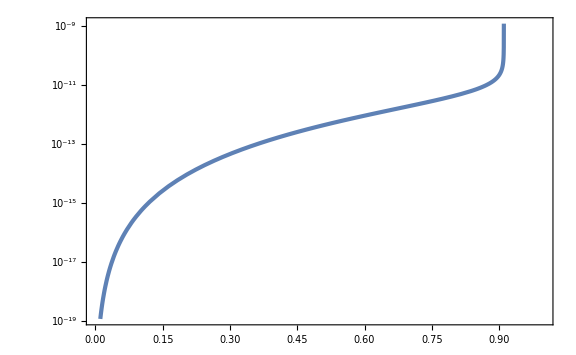

```mathematica
LogPlot[Abs[UnitStep[f[dz,x,μ,β],μ^2/2-f[dz,x,μ,β]]/Sqrt[1-2/μ^2 f[dz,x,μ,β]] x EllipticThetaPrime[1,-π/2 Sqrt[1-2/μ^2 f[dz,x,μ,β]],Exp[-π^2/μ^2(Nbw-Log[1+β])]](EllipticTheta[1,π/2(Sqrt[1-2/μ^2 f[dz,x,μ,β]]-x),Exp[-π^2/μ^2 Log[1+β]]]
-EllipticTheta[1,π/2(Sqrt[1-2/μ^2 f[dz,x,μ,β]]+x),Exp[-π^2/μ^2 Log[1+β]]])/.{dz->-Log[1+5772/1000]-10^-3,μ->1/2,β->5772/1000,Nbw->3}],{x,0,1}]
```

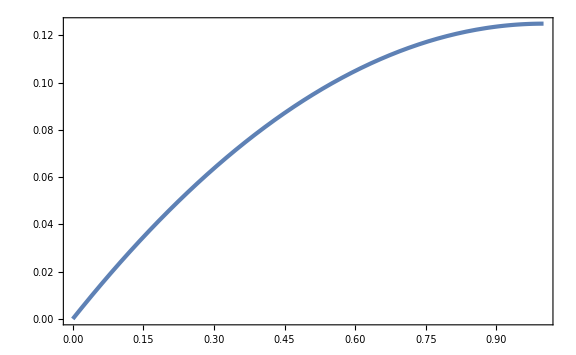

```mathematica
Plot[Nbar[x,1/2],{x,0,1}]
```

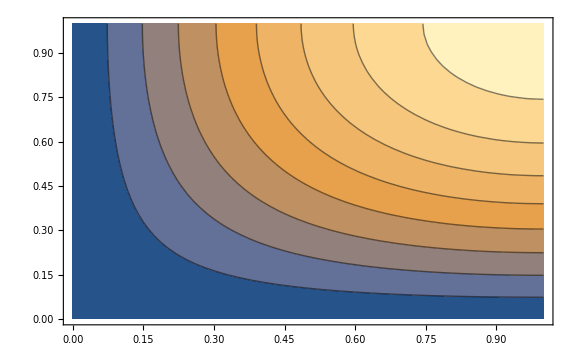

```mathematica
ContourPlot[EllipticTheta[2,-π/2(x2-x1),E^(-π^2 Log[1+11])]-EllipticTheta[2,-π/2(x2+x1),E^(-π^2 Log[1+11])],{x1,0,1},{x2,0,1}]
```

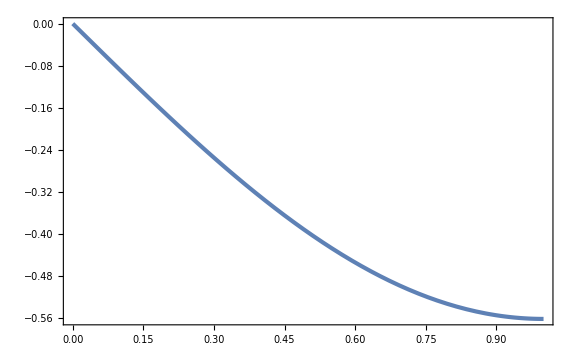

```mathematica
Plot[EllipticThetaPrime[2,π/2 x2,E^(-π^2(3-Log[1+11]))],{x2,0,1}]
```

```mathematica
P1[-Log[1+5772/1000],5/10,5772/1000,3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained -1.64001×10^-10 and 2.57346×10^-11 for the integral and error estimates.

5.15225×10^-10

```mathematica
P1Listp53=Table[{dz,P1[dz,5/10,5772/1000,3]},{dz,-5,1,1/100}];//AbsoluteTiming
P2Listp53=Table[{dz,P2[dz,5/10,5772/1000,3]},{dz,-5,1,1/100}];//AbsoluteTiming
PListp53=Table[{P1Listp53[[i,1]],P1Listp53[[i,2]]+P2Listp53[[i,2]]},{i,Length[P1Listp53]}];
```

{12.2439,Null}

{14.8245,Null}

```mathematica
Pp53int[dz_]=Interpolation[Re[PListp53]][dz];
```

```mathematica
NIntegrate[Pp53int[dz],{dz,-2,1}]
dzmeanp53=NIntegrate[dz Pp53int[dz],{dz,-0.01,0.01}]
s2p53=NIntegrate[(dz-dzmeanp53)^2 Pp53int[dz],{dz,-0.01,0.01}]
```

0.0000304915

-6.68212×10^-9

1.79749×10^-10

```mathematica
calPz[μ_,Nbw_]=0.02 μ^2 E^(-π^2/(4 μ^2)Nbw);
```

```mathematica
calPz[1/2,3]
```

6.91872×10^-16

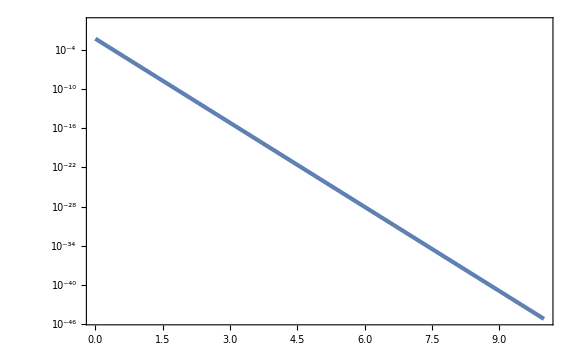

```mathematica
LogPlot[calPz[1/2,Nbw],{Nbw,0,10}]
```

```mathematica
s2Ando[μ_,Nbw_]=Integrate[calPz[μ,Np],{Np,Nbw,Nbw+Log[1+5772/1000]}]
```

0.00810569 (ⅇ^(-(Nbw π^2)/(4 μ^2))-ⅇ^(-(π^2 (Nbw+Log[1693/250]))/(4 μ^2))) μ^4

```mathematica
s2Ando[1/2,3]
```

7.01013×10^-17

General::munfl: Exp[-1.00822×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-927593.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-850326.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

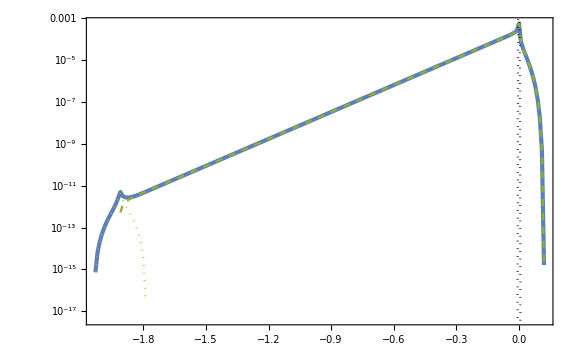

```mathematica
Show[ListLogPlot[{Re[PListp53],Re[P1Listp53],P2Listp53},PlotStyle->{AbsoluteThickness[3],{Color[2],Dotted},{Color[3],Dashed}}],LogPlot[1/Sqrt[2π s2p53] Exp[-dz^2/(2 s2p53)],{dz,-1,1},PlotStyle->{Black,Dotted}]]
```

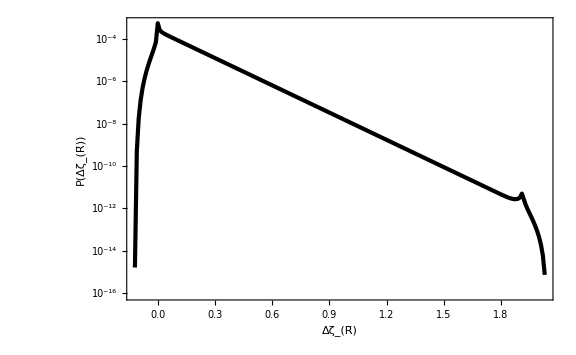

```mathematica
ListLogPlot[Re[PListp53].{{-1,0},{0,1}},PlotStyle->{AbsoluteThickness[3],Black},FrameLabel->{Subscript[Δζ, OverBar[R]],P[Subscript[Δζ, OverBar[R]]]}]
```

General::munfl: Exp[-278143.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255900.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-234584.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

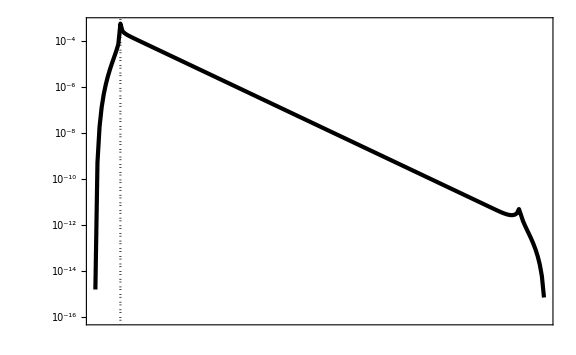

```mathematica
Show[ListLogPlot[Re[PListp53].{{-1,0},{0,1}},PlotStyle->{AbsoluteThickness[3],Black},FrameTicks->None],
LogPlot[1/Sqrt[2π s2p53] Exp[(-(dz-dzmeanp53)^2)/(2 s2p53)],{dz,-0.01,0.01},PlotStyle->{Black,Dotted}]]
```

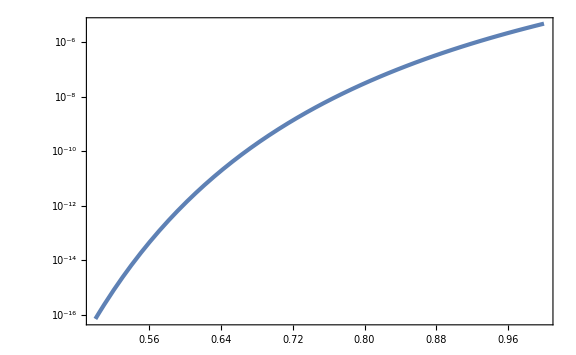

```mathematica
LogPlot[s2pAndo[μ,3],{μ,1/2,1}]
```

```mathematica
P1List13=Table[{dz,P1[dz,1,5772/1000,3]},{dz,-4,1,1/1000}];//AbsoluteTiming
P2List13=Table[{dz,P2[dz,1,5772/1000,3]},{dz,-4,1,1/1000}];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00079678170135991947354176330614675150344496427383595739402100122106}. NIntegrate obtained -1.03575×10^-10+7.13591×10^-17 ⅈ and 1.57483×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0017980808180471534597260369555163919848104355671942165828536275285}. NIntegrate obtained -7.92179×10^-10+1.18953×10^-15 ⅈ and 1.14596×10^-15 for the integral and error estimates.

{185.349,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9126459973547155343786145897244167496233994312013474312430042288678705000868076}. NIntegrate obtained 0.15064625836133376298186716737541659351933684088660672712204131925757337703861921 and 3.8401928923062963713427828063534449748541246113965507338236114047719692809307432×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9123845149007130696685044917424926285722272047850384701492665077654457984723157}. NIntegrate obtained 0.079196583488368842159317452311934418637829221818929876079795695598352703667290422 and 5.7755075410894393899185784194064705991855320464345748597480843921981213757386602×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9123869708531979012089576255064259351199125427873387573453244536200530369356647}. NIntegrate obtained 0.070147136466845394478971370249546282162875409179778029299244107248778416461946206 and 5.5349294991888670693649674807323588677907506396003067816709663529496473902216703×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{212.566,Null}

```mathematica
Export["P1List13.dat",P1List13];
Export["P2List13.dat",P2List13];
```

```mathematica
P1List13=Import["P1List13.dat"]//ToExpression;
P2List13=Import["P2List13.dat"]//ToExpression;
```

```mathematica
PList13=Table[{P1List13[[i,1]],P1List13[[i,2]]+P2List13[[i,2]]},{i,Length[P1List13]}];
```

```mathematica
P13int[dz_]=Interpolation[Re[PList13]][dz];
```

```mathematica
norm13=NIntegrate[P13int[dz],{dz,-0.1,0.1}]
dzmean13=NIntegrate[dz P13int[dz],{dz,-0.1,0.1}]
s213=NIntegrate[(dz-dzmean13)^2 P13int[dz],{dz,-0.1,0.1}]
```

0.0266741

-0.000700923

0.0000664863

```mathematica
calPz[1,3-Log[0.23]]
```

3.24654×10^-7

```mathematica
s2Ando[1,3]
```

4.89963×10^-6

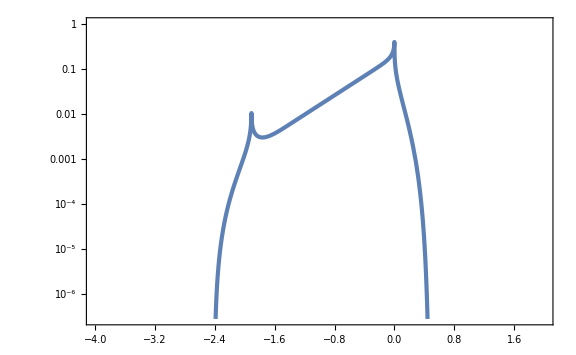

```mathematica
LogPlot[P13int[dz],{dz,-4,2}]
```

General::munfl: Exp[-120318.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-113064.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106036.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

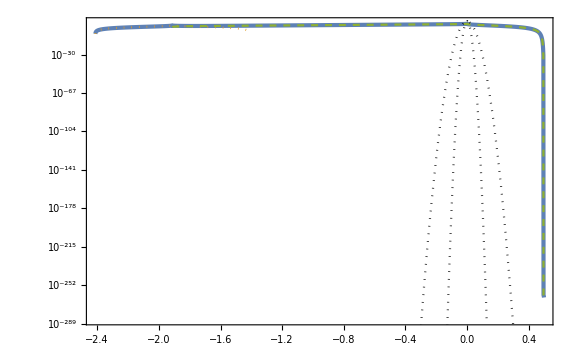

```mathematica
Show[ListLogPlot[{Re[PList13],Re[P1List13],P2List13},PlotStyle->{AbsoluteThickness[3],{Color[2],Dotted},{Color[3],Dashed}}],LogPlot[{1/Sqrt[2π s213] Exp[-dz^2/(2s213)],1/Sqrt[2π calPz[1,3]] Exp[-dz^2/(2calPz[1,3])]},{dz,-4,2},PlotStyle->{{Black,Dotted}}]]
```

General::munfl: Exp[-1020.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-938.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-860.599] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

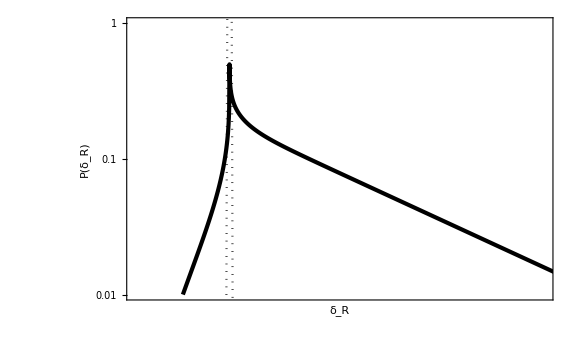

```mathematica
Show[ListLogPlot[PList13.{{-1,0},{0,1}},PlotStyle->{AbsoluteThickness[3],Black},PlotRange->{{-0.3,1},{10^-2,1}},FrameTicks->None,FrameLabel->{Subscript[δ, R],P[Subscript[δ, R]]}],LogPlot[{1/Sqrt[2π s2Ando[1,3]] Exp[-dz^2/(2s2Ando[1,3])]},{dz,-0.1,0.1},PlotStyle->{{Black,Dotted}}]]
```

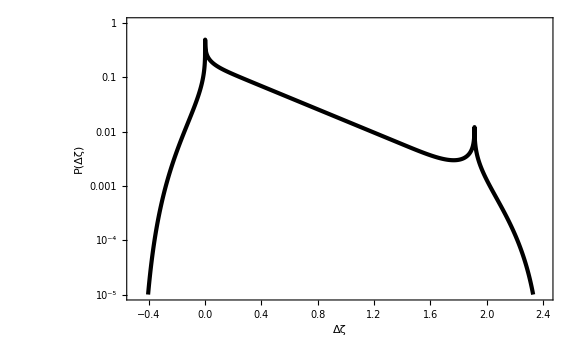

```mathematica
ListLogPlot[Re[PList13.{{-1,0},{0,1}}],PlotStyle->{AbsoluteThickness[3],Black},FrameLabel->{Δζ,P[Δζ]},PlotRange->{10^-5,1},GridLines->{{Log[1+5772/1000]},None}]
```

```mathematica
PList14=Table[{dz,P1[dz,1,1172/100,4]+P2[dz,1,1172/100,4]},{dz,-4,1,1/100}];//AbsoluteTiming
PList15=Table[{dz,P1[dz,1,1172/100,5]+P2[dz,1,1172/100,5]},{dz,-4,1,1/100}];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.53938024210636927698855922541}. NIntegrate obtained 6.63845267534259097200290476279×10^-20 and 2.38918431915232752454346947912×10^-36 for the integral and error estimates.

{50.8168,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.5431564961779656271110580195594377513090138207604915814140437913410299438115177}. NIntegrate obtained 0.010789790677444565033570256724253714587862734354996797069833315162418079181822835 and 3.4295504693349727738079337194715462525368894589651748548402894621931391128138141×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.53938024210636927698855922541}. NIntegrate obtained 5.62973796381575991239578122967×10^-21 and 2.02614710413538224022072136946×10^-37 for the integral and error estimates.

{37.0857,Null}

```mathematica
Log[1172/100+1]//N
Log[5772/1000+1]//N
```

2.54318

1.9128

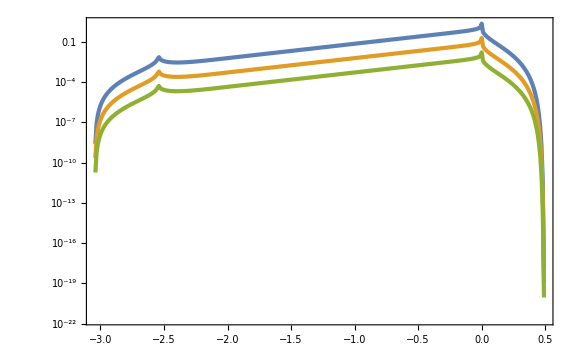

```mathematica
ListLogPlot[{Re[PList13],Re[PList14],Re[PList15]}]
```

```mathematica
P1List43=Table[{dz,P1[dz,4,1172/100,3]},{dz,-11,9,1/10}];//AbsoluteTiming
P2List43=Table[{dz,P2[dz,4,1172/100,3]},{dz,-11,9,1/10}];//AbsoluteTiming
PList43=Table[{P1List43[[i,1]],P1List43[[i,2]]+P2List43[[i,2]]},{i,Length[P1List43]}];
```

{18.3418,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.4837926784940400812222894502}. NIntegrate obtained 4.37925855354669594400971294669×10^-14 and 9.09538715548461540661510234351×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.48262431353671334215190512136}. NIntegrate obtained 4.63508540226019513361202883297×10^-24 and 6.50778510385552884091567561604×10^-35 for the integral and error estimates.

{15.908,Null}

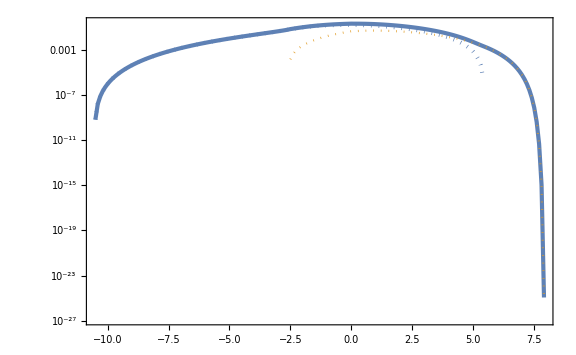

```mathematica
ListLogPlot[{Re[PList43],Re[P1List43],P2List43},PlotStyle->{AbsoluteThickness[3],{Color[1],AbsoluteThickness[3],Dotted},{Color[2],Dotted},{Color[3],Dashed}}]
```

```mathematica
PList44=Table[{dz,P1[dz,4,1172/100,4]+P2[dz,4,1172/100,4]},{dz,-11,9,1/10}];//AbsoluteTiming
PList45=Table[{dz,P1[dz,4,1172/100,5]+P2[dz,4,1172/100,5]},{dz,-11,9,1/10}];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.4837926784940400812222894502}. NIntegrate obtained 7.69537708868790686517003934215×10^-15 and 1.59894652910583566949110926207×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.48262431353671334215190512136}. NIntegrate obtained 8.14480663284138644148306808616×10^-25 and 1.14358243197996193251238718808×10^-35 for the integral and error estimates.

{31.3318,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.4837926784940400812222894502}. NIntegrate obtained 3.63671805377723788780035772429×10^-15 and 7.55707086834000628719816859169×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {2.48262431353671334215190512136}. NIntegrate obtained 3.84909952614790054184017777146×10^-25 and 5.404409850299293299425886359×10^-36 for the integral and error estimates.

{30.6542,Null}

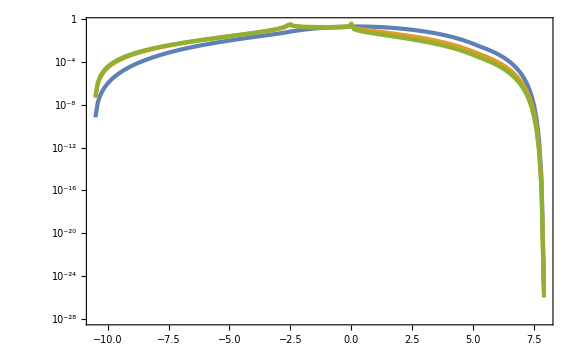

```mathematica
ListLogPlot[{Re[PList43],Re[PList44],Re[PList45]}]
```

### flat well (revised)

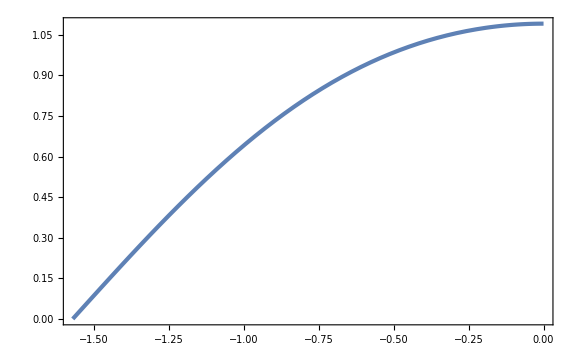

```mathematica
Plot[EllipticThetaPrime[1,x,1/10],{x,-π/2,0}]
```

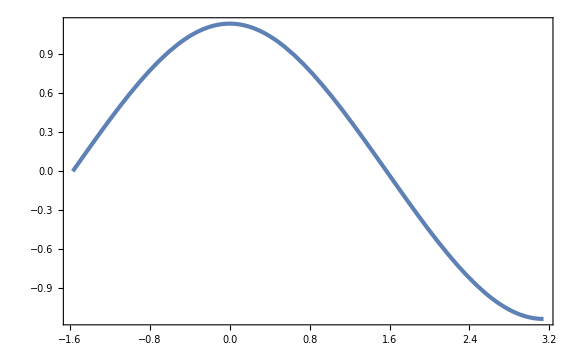

```mathematica
Plot[EllipticTheta[2,x,1/10],{x,-π/2,π}]
```

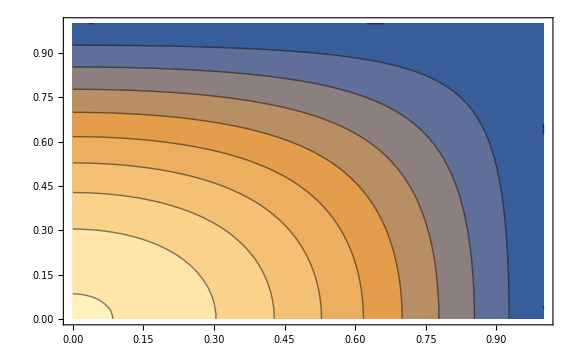

```mathematica
ContourPlot[EllipticTheta[2,-π/2(x1-x2),1/10]+EllipticTheta[2,π/2(x1+x2),1/10],{x1,0,1},{x2,0,1}]
```

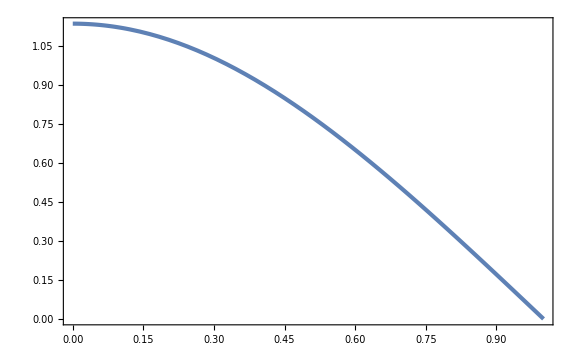

```mathematica
Plot[EllipticTheta[2,π/2 x,1/10],{x,0,1}]
```

```mathematica
xt2well[xt1_,dz_,μ_,β_]=Sqrt[xt1^2-2/μ^2(dz-Log[1+β])];
xt2cl[N1_,dz_,μ_,β_]=Sqrt[2]/μ Sqrt[Log[1+β]-dz-N1];
```

```mathematica
Clear[P1,P2]
```

```mathematica
P1[dz_,μ_,α_,β_,Nbw_]:=π/(4 μ^2)NIntegrate[(1-xt1)/xt2well[xt1,dz,μ,β] EllipticThetaPrime[1,-π/2 xt2well[xt1,dz,μ,β],Exp[-π^2/μ^2(Nbw+Log[α])]]
(EllipticTheta[2,-π/2(xt1-xt2well[xt1,dz,μ,β]),Exp[-π^2/μ^2 Log[1+β]]]
+EllipticTheta[2,π/2(xt1+xt2well[xt1,dz,μ,β]),Exp[-π^2/μ^2 Log[1+β]]]),{xt1,Sqrt[Max[0,2/μ^2(dz-Log[1+β])]],Min[1,Sqrt[1+2/μ^2(dz-Log[1+β])]]}]/;Log[1+β]-μ^2/2<dz<Log[1+β]+μ^2/2
P1[dz_,μ_,α_,β_,Nbw_]:=0/;!(Log[1+β]-μ^2/2<dz<Log[1+β]+μ^2/2)
```

```mathematica
P2[dz_,μ_,α_,β_,Nbw_]:=π/(4 μ^4)NIntegrate[1/xt2cl[N1,dz,μ,β] EllipticThetaPrime[1,-π/2 xt2cl[N1,dz,μ,β],Exp[-π^2/μ^2(Nbw+Log[α])]]
EllipticTheta[2,π/2 xt2cl[N1,dz,μ,β],Exp[-π^2/μ^2(Log[1+β]-N1)]],{N1,Max[0,Log[1+β]-dz-μ^2/2],Log[1+β]-Max[0,dz]},WorkingPrecision->15]/;-μ^2/2<dz<Log[1+β]
P2[dz_,μ_,α_,β_,Nbw_]:=0/;!(-μ^2/2<dz<Log[1+β])
```

```mathematica
P1Listp53=Table[{dz,P1[dz,5/10,23/100,577/100,3]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
P2Listp53=Table[{dz,P2[dz,5/10,23/100,577/100,3]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
PListp53=Table[{P1Listp53[[i,1]],P1Listp53[[i,2]]+P2Listp53[[i,2]]},{i,Length[P1Listp53]}];
```

{0.269892,Null}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{3.8659,Null}

```mathematica
Pp53int[dz_]=Interpolation[Re[PListp53]][dz];
```

```mathematica
NIntegrate[Pp53int[dz],{dz,-1,3}]
dzmeanp53=NIntegrate[dz Pp53int[dz],{dz,-1,3}]
s2p53=NIntegrate[(dz-dzmeanp53)^2 Pp53int[dz],{dz,-1,3}]
```

1.72523×10^-7

1.52586×10^-8

3.12614×10^-9

```mathematica
calPz[μ_,Nbw_]=0.02 μ^2 E^(-π^2/(4 μ^2)Nbw);
```

```mathematica
calPz[1/2,3]
```

6.91872×10^-16

```mathematica
LogPlot[calPz[1/2,Nbw],{Nbw,0,10}]
```

-Graphics-

```mathematica
s2Ando[μ_,Nbw_]=Integrate[calPz[μ,Np],{Np,Nbw+Log[0.23],Nbw+Log[0.23]+Log[1+5.77]}]
```

0.02 (-0.405285 2.71828^(-(2.4674 (0.442825+Nbw))/μ^2)+0.405285 ⅇ^((3.62628-2.4674 Nbw)/μ^2)) μ^4

```mathematica
s2Ando[1/2,3]
```

1.39708×10^-10

General::munfl: Exp[-15992.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14713.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13488.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

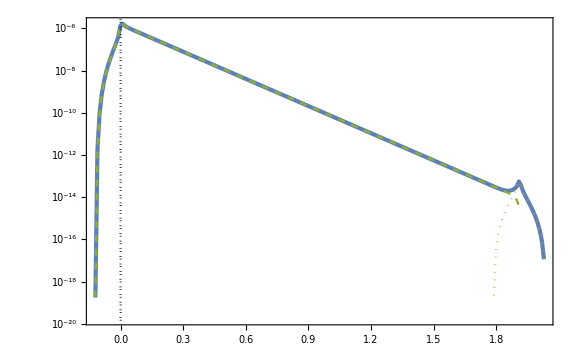

```mathematica
Show[ListLogPlot[{Re[PListp53],Re[P1Listp53],P2Listp53},PlotStyle->{AbsoluteThickness[3],{Color[2],Dotted},{Color[3],Dashed}}],LogPlot[1/Sqrt[2π s2p53] Exp[-dz^2/(2 s2p53)],{dz,-0.01,0.01},PlotStyle->{Black,Dotted}]]
```

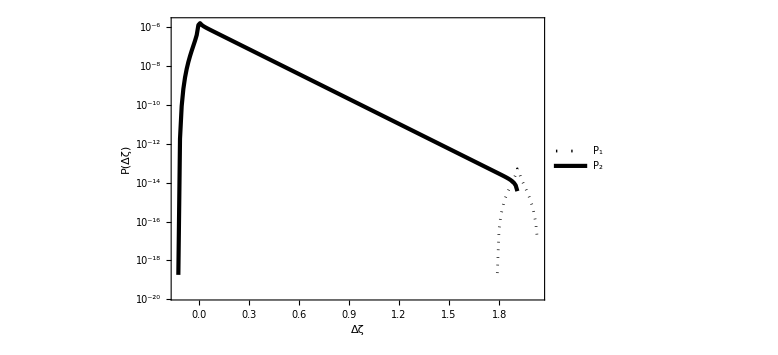

```mathematica
ListLogPlot[{P1Listp53,Re[P2Listp53]},PlotStyle->{{Dotted,Black,AbsoluteThickness[2]},{AbsoluteThickness[3],Black}},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==1,"/2, ",Subscript[N, bw][R]==3}]}},PlotLegends->Placed[{Subscript[P, 1],Subscript[P, 2]},{0.8,0.8}]]
```

```mathematica
P1Listp54=Table[{dz,P1[dz,5/10,23/100,577/100,4]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
P2Listp54=Table[{dz,P2[dz,5/10,23/100,577/100,4]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
PListp54=Table[{P1Listp54[[i,1]],P1Listp54[[i,2]]+P2Listp54[[i,2]]},{i,Length[P1Listp54]}];
```

{0.29341,Null}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{3.47223,Null}

```mathematica
P1Listp55=Table[{dz,P1[dz,5/10,23/100,577/100,5]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
P2Listp55=Table[{dz,P2[dz,5/10,23/100,577/100,5]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
PListp55=Table[{P1Listp55[[i,1]],P1Listp55[[i,2]]+P2Listp55[[i,2]]},{i,Length[P1Listp55]}];
```

{0.266372,Null}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{3.80181,Null}

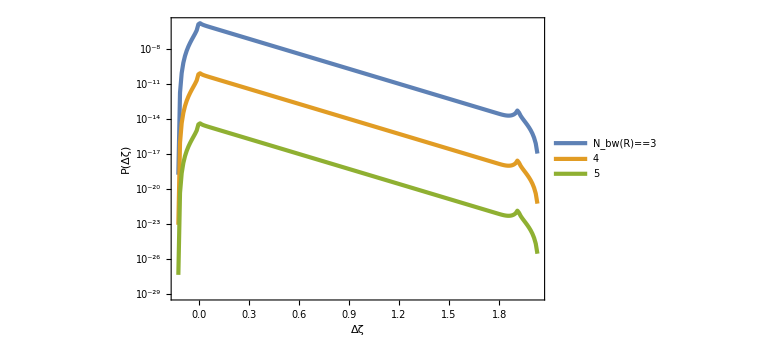

```mathematica
ListLogPlot[{PListp53,PListp54,PListp55},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==1,"/2"}]}},PlotLegends->Placed[LineLegend[{Subscript[N, bw][R]==3,4,5},LegendLayout->"Row"],{0.4,0.15}]]
```

```mathematica
P1List13=Table[{dz,P1[dz,1,23/100,577/100,3]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
P2List13=Table[{dz,P2[dz,1,23/100,577/100,3]},{dz,-1-10^-3,5,10^-2}];//AbsoluteTiming
PList13=Table[{P1List13[[i,1]],P1List13[[i,2]]+P2List13[[i,2]]},{i,Length[P1List13]}];
```

{1.382,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.912076045176364273293323362339172047074401117737497484168505335}. NIntegrate obtained 1.2270533895354164983636350331441201641196348773153756808493474997×10^-259 and 6.2582315313970484238729208949473712240200528570120930220697459161×10^-262 for the integral and error estimates.

{6.50447,Null}

```mathematica
Log[1+5.77]
```

1.9125

```mathematica
P2[-2-10^-3+5/100,2,23/100,577/100,3]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.89737978536264872734919734708}. NIntegrate obtained 8.8209862335622776043304377353×10^-16 and 3.11627507896750824040950148314×10^-35 for the integral and error estimates.

4.3299914919962424026309429799×10^-17

```mathematica
P1List23=Table[{dz,P1[dz,2,23/100,577/100,3]},{dz,-2-10^-3,5,10^-2}];//AbsoluteTiming
P2List23=Table[{dz,P2[dz,2,23/100,577/100,3]},{dz,-2-10^-3,5,10^-2}];//AbsoluteTiming
PList23=Table[{P1List23[[i,1]],P1List23[[i,2]]+P2List23[[i,2]]},{i,Length[P1List23]}];
```

{5.52462,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.91081344704942}. NIntegrate obtained 4.87027605121706×10^-262 and 1.94050693948691×10^-262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.91083086975801}. NIntegrate obtained 2.69826678373963×10^-260 and 1.71407888649129×10^-260 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9107758059881614183950524068460915619755594859055507483894796785}. NIntegrate obtained 8.8580978020317753187874797192398222863714428594504678589400854544×10^-259 and 4.6202119546171801907936338167739078973040724638337941233745571368×10^-259 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{6.91896,Null}

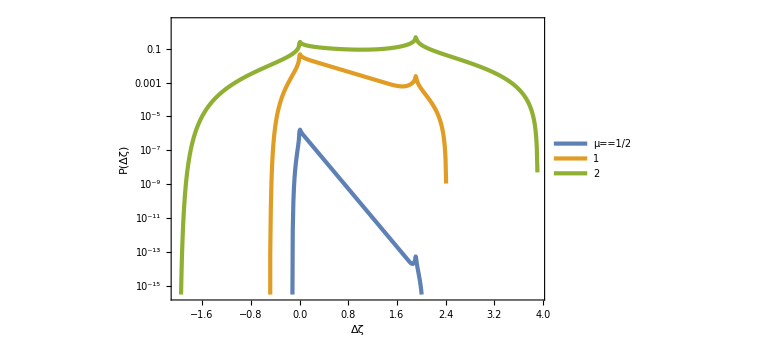

```mathematica
ListLogPlot[{PListp53,PList13,PList23},PlotRange->{10^-15.5,10^0.5},FrameLabel->{{P[Δζ],None},{Δζ,Subscript[N, bw][R]==3}},PlotLegends->Placed[LineLegend[{Row[{μ==1,"/2"}],1,2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.2}]]
```

### flat well PBH (RTHfFTHg)

```mathematica
xt2well[xt1_,dz_,μ_,β_]=Sqrt[xt1^2-2/μ^2(dz-Log[1+β])];
xt2cl[N1_,dz_,μ_,β_]=Sqrt[2]/μ Sqrt[Log[1+β]-dz-N1];
```

```mathematica
Clear[P1,P2]
```

```mathematica
P1[dz_,μ_,α_,β_,Nbw_]:=π/(4 μ^2)NIntegrate[(1-xt1)/xt2well[xt1,dz,μ,β] EllipticThetaPrime[1,-π/2 xt2well[xt1,dz,μ,β],Exp[-π^2/μ^2(Nbw+Log[α])]]
(EllipticTheta[2,-π/2(xt1-xt2well[xt1,dz,μ,β]),Exp[-π^2/μ^2 Log[1+β]]]
+EllipticTheta[2,π/2(xt1+xt2well[xt1,dz,μ,β]),Exp[-π^2/μ^2 Log[1+β]]]),{xt1,Sqrt[Max[0,2/μ^2(dz-Log[1+β])]],Min[1,Sqrt[1+2/μ^2(dz-Log[1+β])]]},MaxRecursion->20]/;Log[1+β]-μ^2/2<dz<Log[1+β]+μ^2/2
P1[dz_,μ_,α_,β_,Nbw_]:=0/;!(Log[1+β]-μ^2/2<dz<Log[1+β]+μ^2/2)
```

```mathematica
P2[dz_,μ_,α_,β_,Nbw_]:=π/(4 μ^4)NIntegrate[1/xt2cl[N1,dz,μ,β] EllipticThetaPrime[1,-π/2 xt2cl[N1,dz,μ,β],Exp[-π^2/μ^2(Nbw+Log[α])]]
EllipticTheta[2,π/2 xt2cl[N1,dz,μ,β],Exp[-π^2/μ^2(Log[1+β]-N1)]],{N1,Max[0,Log[1+β]-dz-μ^2/2],Log[1+β]-Max[0,dz]},WorkingPrecision->15,MaxRecursion->20]/;-μ^2/2<dz<Log[1+β]
P2[dz_,μ_,α_,β_,Nbw_]:=0/;!(-μ^2/2<dz<Log[1+β])
```

```mathematica
αRTHfFTHg=230/1000;
βRTHfFTHg=577/100;
γRTHfFTHg=146/100;
```

```mathematica
dzmin[μ_]=-μ^2/2;
dzmax[μ_]=Log[1+βRTHfFTHg]+μ^2/2;
```

#### sample

```mathematica
P1Listp53=Table[{dz,P1[dz,1/2,αGfFTHg,βGfFTHg,3]},{dz,dzmin[1/2],dzmax[1/2],10^-2}];//AbsoluteTiming
P2Listp53=Table[{dz,P2[dz,1/2,αGfFTHg,βGfFTHg,3]},{dz,dzmin[1/2],dzmax[1/2],10^-2}];//AbsoluteTiming
PListp53=Table[{P1Listp53[[i,1]],P1Listp53[[i,2]]+P2Listp53[[i,2]]},{i,Length[P1Listp53]}];
```

{0.359026,Null}

{1.43994,Null}

```mathematica
Pp53int[dz_]=Interpolation[Re[PListp53]][dz];
```

```mathematica
NIntegrate[Pp53int[dz],{dz,dzmin[1/2],dzmax[1/2]}]
dzmeanp53=NIntegrate[dz Pp53int[dz],{dz,dzmin[1/2],dzmax[1/2]}]
s2p53=NIntegrate[(dz-dzmeanp53)^2 Pp53int[dz],{dz,dzmin[1/2],dzmax[1/2]}]
```

InterpolatingFunction::dmvali: The integration endpoint 2.08369 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

6.81176×10^-10

6.02506×10^-11

1.23311×10^-11

```mathematica
calPz[μ_,Nbw_]=0.02 μ^2 E^(-π^2/(4 μ^2)Nbw);
```

```mathematica
calPz[1/2,3]
```

6.91872×10^-16

```mathematica
LogPlot[calPz[1/2,Nbw],{Nbw,0,10}]
```

-Graphics-

```mathematica
s2Ando[μ_,Nbw_]=Integrate[calPz[μ,Np],{Np,Nbw+Log[αGfFTHg],Nbw+Log[αGfFTHg]+Log[1+βGfFTHg]}]
```

0.00810569 ⅇ^((-2.59044-2.4674 Nbw)/μ^2) (-1.+1. ⅇ^(4.83286/μ^2)) μ^4

```mathematica
s2Ando[1/2,3]
```

5.51073×10^-13

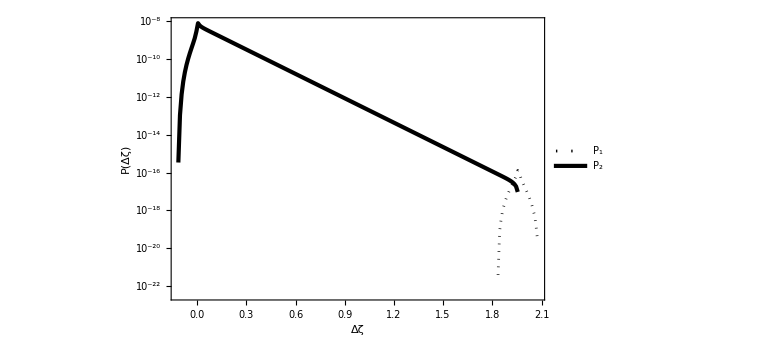

```mathematica
ListLogPlot[{P1Listp53,Re[P2Listp53]},PlotStyle->{{Dotted,Black,AbsoluteThickness[2]},{AbsoluteThickness[3],Black}},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==1,"/2, ",Subscript[N, bw][R]==3}]}},PlotLegends->Placed[{Subscript[P, 1],Subscript[P, 2]},{0.8,0.8}]]
```

```mathematica
P1Listp54=Table[{dz,P1[dz,1/2,αGfFTHg,βGfFTHg,4]},{dz,dzmin[1/2],dzmax[1/2],10^-2}];//AbsoluteTiming
P2Listp54=Table[{dz,P2[dz,1/2,αGfFTHg,βGfFTHg,4]},{dz,dzmin[1/2],dzmax[1/2],10^-2}];//AbsoluteTiming
PListp54=Table[{P1Listp54[[i,1]],P1Listp54[[i,2]]+P2Listp54[[i,2]]},{i,Length[P1Listp54]}];
```

{0.187897,Null}

{1.79091,Null}

```mathematica
P1Listp55=Table[{dz,P1[dz,1/2,αGfFTHg,βGfFTHg,5]},{dz,dzmin[1/2],dzmax[1/2],10^-2}];//AbsoluteTiming
P2Listp55=Table[{dz,P2[dz,1/2,αGfFTHg,βGfFTHg,5]},{dz,dzmin[1/2],dzmax[1/2],10^-2}];//AbsoluteTiming
PListp55=Table[{P1Listp55[[i,1]],P1Listp55[[i,2]]+P2Listp55[[i,2]]},{i,Length[P1Listp55]}];
```

{0.131449,Null}

{1.65888,Null}

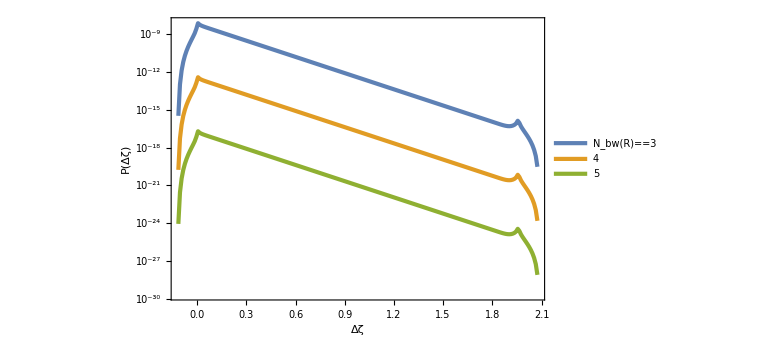

```mathematica
ListLogPlot[{PListp53,PListp54,PListp55},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==1,"/2"}]}},PlotLegends->Placed[LineLegend[{Subscript[N, bw][R]==3,4,5},LegendLayout->"Row"],{0.4,0.15}]]
```

```mathematica
P1List13=Table[{dz,P1[dz,1,αGfFTHg,βGfFTHg,3]},{dz,dzmin[1],dzmax[1],10^-2}];//AbsoluteTiming
P2List13=Table[{dz,P2[dz,1,αGfFTHg,βGfFTHg,3]},{dz,dzmin[1],dzmax[1],10^-2}];//AbsoluteTiming
PList13=Table[{P1List13[[i,1]],P1List13[[i,2]]+P2List13[[i,2]]},{i,Length[P1List13]}];
```

{0.727553,Null}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9578062788776307468000896589610455012103926740786329805006250876}. NIntegrate obtained 1.3878115496803079314844385527423121071924968347970418928095281241×10^-20-2.4584397496410929957780074286883329493783266028008074010561988462×10^-276 ⅈ and 2.7549766623652582091905431806367157353347424006529160431188021615×10^-24 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.95868534054404,1.958685340544035015129904560512405683023322497560223556765231425}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9586853405004291642929400121019503822869429556706629688190577858}. NIntegrate obtained 0.089448579259418550599394085601860909335005045100444758732151100237-6.1937437758807838829974678568526548293924431947595465831692659715×10^-18 ⅈ and 0.00096492642494336642336994094878585377420957696177799326149078008124 for the integral and error estimates.

{3.00679,Null}

```mathematica
P1List23=Table[{dz,P1[dz,2,αGfFTHg,βGfFTHg,3]},{dz,dzmin[2],dzmax[2],10^-2}];//AbsoluteTiming
P2List23=Table[{dz,P2[dz,2,αGfFTHg,βGfFTHg,3]},{dz,dzmin[2],dzmax[2],10^-2}];//AbsoluteTiming
PList23=Table[{P1List23[[i,1]],P1List23[[i,2]]+P2List23[[i,2]]},{i,Length[P1List23]}];
```

{1.94021,Null}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.95679065387763}. NIntegrate obtained 4.66540569303979×10^-24 and 5.8807400228099×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.95665377971123}. NIntegrate obtained -2.85154103291146×10^-24 and 5.2756971308728×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in N1 near {N1} = {1.9565754992948201332338747483728768857301930645140839873377647833}. NIntegrate obtained 1.0343355644005282609218218957125631878442580192669324145981334951×10^-22 and 1.3855152165201100809020463776763380103756544917602271846894563436×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{3.63885,Null}

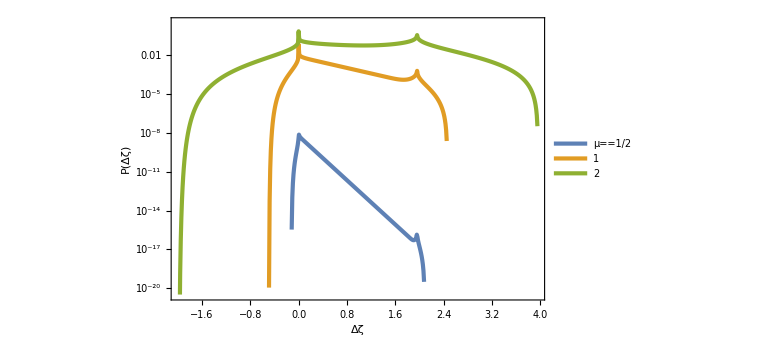

```mathematica
ListLogPlot[{PListp53,PList13,PList23},PlotRange->{10^-20.5,10^0.5},FrameLabel->{{P[Δζ],None},{Δζ,Subscript[N, bw][R]==3}},PlotLegends->Placed[LineLegend[{Row[{μ==1,"/2"}],1,2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.2}]]
```

#### PBH

```mathematica
(6 10^-3)^(1/4)//N
```

0.278316

```mathematica
μs=1/3;
dN=10^-3;
Nbwmin=-Log[αRTHfFTHg]-Log[1+βRTHfFTHg];Nbwmin//N
Nbws=-Log[αRTHfFTHg];Nbws//N
Nbwmax=20 μs^2+dN;Nbwmax//N
```

-0.442825

1.46968

2.22322

```mathematica
μs^4/6//N
```

0.00205761

```mathematica
Clear[P,P3,P4]
```

```mathematica
x1well[dz_,μ_,α_,β_,Nbw_]=1-Sqrt[1-2/μ^2(Nbw+Log[α]+Log[1+β]-dz)];
```

```mathematica
P3[dz_,μ_,α_,β_,Nbw_]:=-(π x1well[dz,μ,α,β,Nbw])/(2 μ^2(1-x1well[dz,μ,α,β,Nbw]))EllipticThetaPrime[2,π/2 x1well[dz,μ,α,β,Nbw],E^(-π^2(Nbw+Log[α]+Log[1+β])/μ^2)]/;Nbw+Log[α]+Log[1+β]-μ^2/2<dz<Nbw+Log[α]+Log[1+β]
P3[dz_,μ_,α_,β_,Nbw_]:=0/;!(Nbw+Log[α]+Log[1+β]-μ^2/2<dz<Nbw+Log[α]+Log[1+β])
```

```mathematica
P4[dz_,μ_,α_,β_,Nbw_]:=-π/(2 μ^2)EllipticThetaPrime[2,π/2,E^(-π^2(dz+μ^2/2)/μ^2)]/;-μ^2/2<dz≤Nbw+Log[α]+Log[1+β]-μ^2/2
P4[dz_,μ_,α_,β_,Nbw_]:=0/;!(-μ^2/2<dz≤Nbw+Log[α]+Log[1+β]-μ^2/2)
```

```mathematica
P[dz_,μ_,α_,β_,Nbw_]:=P1[dz,μ,α,β,Nbw]+P2[dz,μ,α,β,Nbw]/;Nbw>Nbws
P[dz_,μ_,α_,β_,Nbw_]:=P3[dz,μ,α,β,Nbw]+P4[dz,μ,α,β,Nbw]/;Nbw≤Nbws
```

```mathematica
LogPmin=-50;
ddz=10^-3;
```

```mathematica
Nbws//N
Nbwmin//N
Nbwmin+1913dN//N
```

1.46968

-0.442825

1.47017

```mathematica
ParallelTable[{dz,Log10[Max[Re[P[dz,μs,αRTHfFTHg,βRTHfFTHg,Nbws+10^-3(*Nbwmin+1913dN*)]],10^LogPmin]]//N},{dz,dzmin[μs]+2ddz,dzmax[μs],ddz}]
```

{{-241/4500,-9.0439},{-473/9000,-6.31544},{-58/1125,-4.81369},{-91/1800,-3.83356},{-223/4500,-3.12908},2013,{442/225,-27.2009},{17689/9000,-28.0964},{8849/4500,-29.2833},{17707/9000,-31.215}}
 |  |  |  |

```mathematica
LogPList=Join[Flatten[ParallelTable[{Nbw//N,dz,Log10[Max[Re[P[dz,μs,αRTHfFTHg,βRTHfFTHg,Nbw]],10^LogPmin]//N]},{Nbw,Nbwmin+dN,Nbws,dN},{dz,dzmin[μs]+2ddz,dzmax[μs],ddz}],1],
Flatten[ParallelTable[{Nbw//N,dz,Log10[Max[Re[P[dz,μs,αRTHfFTHg,βRTHfFTHg,Nbw]],10^LogPmin]//N]},{Nbw,Nbws+dN,Nbwmax,dN},{dz,dzmin[μs]+2ddz,dzmax[μs],ddz}],1]];//AbsoluteTiming
```

{2942.66,Null}

```mathematica
Export["LogPmu13rd.dat",LogPList];
```

```mathematica
LogPList=Import["LogPmu13rd.dat"]//ToExpression;
```

```mathematica
Pint[Nbw_,dz_]=10^(Interpolation[LogPList,InterpolationOrder->1][Nbw,dz]);
```

```mathematica
Nbwmin+dN//N
Nbwmax//N
```

-0.441825

2.22322

```mathematica
dzth=dz/.Solve[(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)==dth,dz][[2]]/.{dth->0.59,w->1/3,γ->γRTHfFTHg}
dzlim=dz/.Solve[(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)==dth,dz][[1]]/.{dth->0.59,w->1/3,γ->γRTHfFTHg}
```

1.35798

2.75161

```mathematica
Simplify[Solve[(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)==dth,dz]/.{w->1/3},{γ>0}]
```

{{dz→(6+3 √(4-6 dth))/(2 γ)},{dz→(6-3 √(4-6 dth))/(2 γ)}}

```mathematica
γRTHfFTHg//N
```

1.46

```mathematica
(6-3 √(4-6 dth))/(2 γ)/.{dth->0.59,γ->γRTHfFTHg}
(6+3 √(4-6 dth))/(2 γ)/.{dth->0.59,γ->γRTHfFTHg}
```

1.35798

2.75161

```mathematica
dzmax[μs]//N
```

1.96806

```mathematica
βRTHfFTHg//N
```

5.77

```mathematica
Manipulate[Show[LogPlot[Pint[Nbw,dz],{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotRange->{10^-40.5,10^3.5},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==μs,", ",Subscript[N, bw]==Nbw//N}]}},PlotStyle->{AbsoluteThickness[3],Black},GridLines->{None,{10^-16}}],LogPlot[10^4 UnitStep[dz-dzth,dzlim-dz],{dz,dzmin[μs],dzmax[μs]+1},Filling->Bottom,PlotRange->{10^4,10^-50}]],{Nbw,Nbwmin+dN,Nbwmax-dN,dN}]
```

```mathematica
Nbwmin//N
Nbws//N
Nbwmax//N
```

-0.442825

1.46968

2.22322

```mathematica
PintListn=Reverse[Table[Pint[Nbw,dz],{Nbw,Nbwmin+dN,Nbws,(Nbws-Nbwmin-dN)/10}]];
PintListp=Table[Pint[Nbw,dz],{Nbw,Nbws+dN,Nbwmax-dN,(Nbwmax-dN-Nbws-dN)/10}];
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

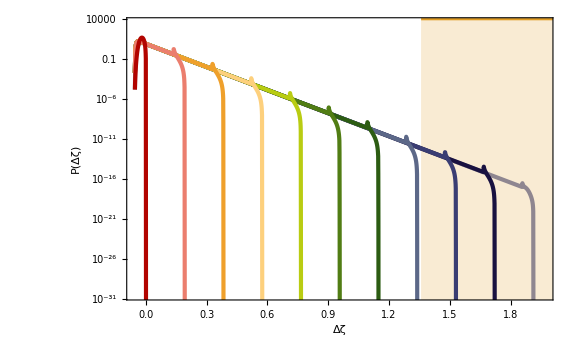

```mathematica
Show[LogPlot[10^-50,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotRange->{10^-30.5,10^3.5},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==μs,", ",Subscript[N, bw]^("(2)")<0}]}}],
LogPlot[10^4 UnitStep[dz-dzth,dzlim-dz],{dz,dzmin[μs],dzmax[μs]+1},Filling->Bottom,PlotRange->{10^-50,10^4},PlotStyle->Color[2]],
LogPlot[PintListn,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotStyle->Map[{AbsoluteThickness[3],#}&,Reverse[ColorData[10,"ColorList"]]]]]
```

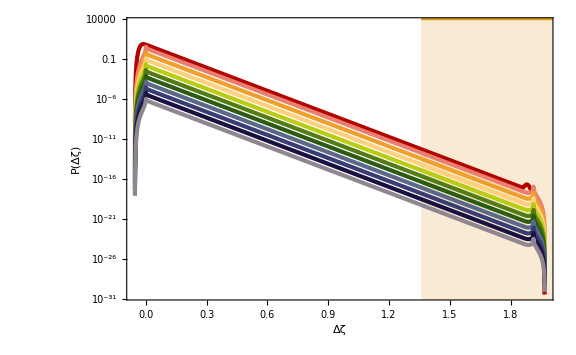

```mathematica
Show[LogPlot[10^-50,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotRange->{10^-30.5,10^3.5},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==μs,", ",Subscript[N, bw]^("(2)")>0}]}}],
LogPlot[10^4 UnitStep[dz-dzth,dzlim-dz],{dz,dzmin[μs],dzmax[μs]+1},Filling->Bottom,PlotRange->{10^4,10^-50},PlotStyle->Color[2]],
LogPlot[PintListp,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotRange->{10^-30.5,10^3.5},PlotStyle->Map[{AbsoluteThickness[3],#}&,ColorData[10,"ColorList"]]]]
```

```mathematica
dzmin[μs]//N
```

-0.0555556

```mathematica
NIntegrate[Pint[Min[Nbws,Nbwmax],dz],{dz,dzmin[μs]+2ddz,dzmax[μs]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {-0.04377535590850922635197672860840611974708735942840576171875}. NIntegrate obtained 0.714942 and 0.0000372217 for the integral and error estimates.

0.714942

```mathematica
P[dzth,μs,αRTHfFTHg,βRTHfFTHg,Min[Nbws,Nbwmax]]
```

6.59118×10^-13

```mathematica
dzmean=NIntegrate[dz Pint[Min[Nbws,Nbwmax],dz],{dz,dzmin[μs],dzmax[μs]}]
var=NIntegrate[(dz-dzmean)^2 Pint[Min[Nbws,Nbwmax],dz],{dz,dzmin[μs],dzmax[μs]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {-0.0437305272468047}. NIntegrate obtained 0.00768891 and 2.99403×10^-7 for the integral and error estimates.

0.00768891

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {-0.04373052724680470508544782859416955034248530864715576171875}. NIntegrate obtained 0.00152229 and 1.64167×10^-8 for the integral and error estimates.

0.00152229

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
(κ 10^20 gineV (1.56 10^13 MpcinvineV)^3)/(4π p MplineV^2 0.12 (100kminvsinvMpcineV)^2)/.{κ->3.3,p->0.36}
```

1.25405×10^16

```mathematica
((κ 10^20 gineV (1.56 10^13 MpcinvineV)^3)/(4π p MplineV^2 0.12 (100kminvsinvMpcineV)^2)/.{κ->3.3,p->0.36})^-1
```

7.97417×10^-17

```mathematica
CompactC[dz_]=(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)/.{w->1/3,γ->γRTHfFTHg}
```

2/3 (1-(1-(73 dz)/150)^2)

```mathematica
NbwPBH=dzth-Log[αRTHfFTHg]-Log[1+βRTHfFTHg]
```

0.915155

```mathematica
fPBHN[Nbw_,dz_]=1/(7.97 10^-17)E^-Nbw(CompactC[dz]-dth)^(p+1)Pint[Nbw,dz]/.{dth->0.59,p->0.36};
MPBHN20[Nbw_,dz_]=κ E^(-2Nbw)(CompactC[dz]-dth)^p/.{κ->3.3,p->0.36,dth->0.59};
```

```mathematica
dlogddz=10^-3;
logddzmin=-7;
```

```mathematica
fPBHNfixList=Table[{MPBHN20[(*NbwPBH+3dN*)Nbws,dzth+10^logddz],fPBHN[(*NbwPBH+3dN*)Nbws,dzth+10^logddz]},{logddz,logddzmin,Log10[dzmax[μs]-ddz-dzth],dlogddz}];
```

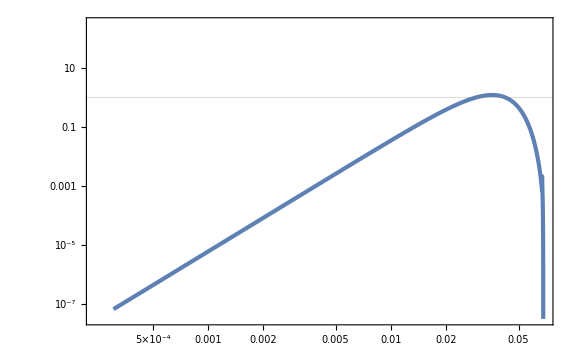

```mathematica
ListLogLogPlot[fPBHNfixList,GridLines->{None,{1}},PlotRange->{10^-7.5,10^2.5}]
```

```mathematica
LogfPBHNList=Table[{Nbw,Log10[MPBHN20[Nbw,dzth+10^logddz]],Log10[fPBHN[Nbw,dzth+10^logddz]//Quiet]},{Nbw,NbwPBH+dN,Nbwmax,dN},{logddz,logddzmin,Log10[dzmax[μs]-dzth],dlogddz}];//AbsoluteTiming
```

{267.664,Null}

```mathematica
Length[LogfPBHNList]
(Nbwmax-NbwPBH-dN)/dN
```

1308

1307.07

```mathematica
Logfmin=-50;
```

```mathematica
LogfPBHNintList[MPBH_]=Table[(Interpolation[LogfPBHNList[[i]].Transpose[{{0,1,0},{0,0,1}}],InterpolationOrder->1][Log10[MPBH]]-Logfmin )UnitStep[Log10[MPBH]-First[LogfPBHNList[[i]]][[2]],Last[LogfPBHNList[[i]]][[2]]-Log10[MPBH]]
+Logfmin,{i,Length[LogfPBHNList]}];
```

```mathematica
MPBHmin=0.001;
MPBHmax=0.5;
```

```mathematica
Manipulate[LogLinearPlot[LogfPBHNintList[M][[i]],{M,MPBHmin,MPBHmax},PlotRange->{-7,2}],{i,1,Length[LogfPBHNList],1}]
```

```mathematica
Manipulate[ListLogPlot[{LogfPBHNintList[10^logM],-LogfPBHNintList[10^logM]}],{logM,Log10[MPBHmin],Log10[MPBHmax],10^-2}]
```

InterpolatingFunction::dmval: Input value {-1.35} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.42} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.23} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
LogfPBHList=Table[{logM,Max[LogfPBHNintList[10^logM]]},{logM,Log10[MPBHmin],Log10[MPBHmax],10^-3}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-1.816} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.815} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{30.1842,Null}

```mathematica
Export["LogfPBH.dat",LogfPBHList];
```

```mathematica
LogfPBHList=Import["LogfPBH.dat"]//ToExpression;
```

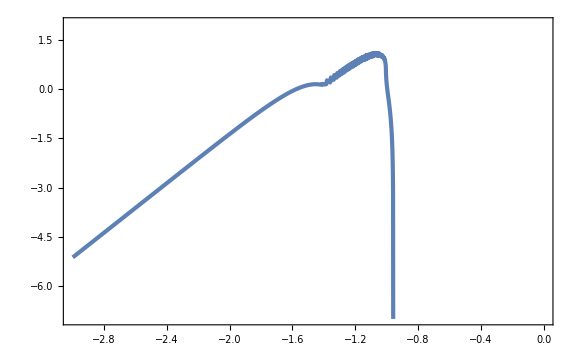

```mathematica
ListPlot[LogfPBHList,PlotRange->{-7,2}]
```

```mathematica
fPBHint[M_]=10^(Interpolation[LogfPBHList,InterpolationOrder->1][Log10[M]]);
```

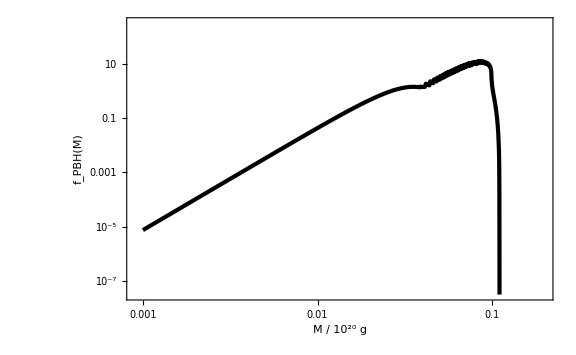

```mathematica
LogLogPlot[fPBHint[M],{M,MPBHmin,MPBHmax},PlotRange->{{0.0009,0.2},{10^-7.5,10^2.5}},PlotStyle->{Black,AbsoluteThickness[3]},FrameLabel->{Row[{M," / 10^20 g"}],Subscript[f, PBH][M]}]
```

```mathematica
Quotient[Length[LogfPBHNList]-150,5]
```

231

```mathematica
Table[i,{i,33,153,30}]
Table[i,{i,153+100,153+100 6,100}]
```

{33,63,93,123,153}

{253,353,453,553,653,753}

```mathematica
(Nbws-NbwPBH-dN)/dN
```

553.521

```mathematica
Table[i,{i,53,1053,100}][[10]]
```

953

```mathematica
fPBHNList=Table[Map[{10^(#[[2]]),10^(#[[3]])}&,Select[LogfPBHNList[[i]],#[[2]]>Log10[MPBHmin]&]],{i,53,1053,100}](*Join[Table[Map[{10^(#[[2]]),10^(#[[3]])}&,LogfPBHNList[[i]]],{i,33,153,30}],
Table[Map[{10^(#[[2]]),10^(#[[3]])}&,LogfPBHNList[[i]]],{i,153+100,153+100 6,100}]]*);
```

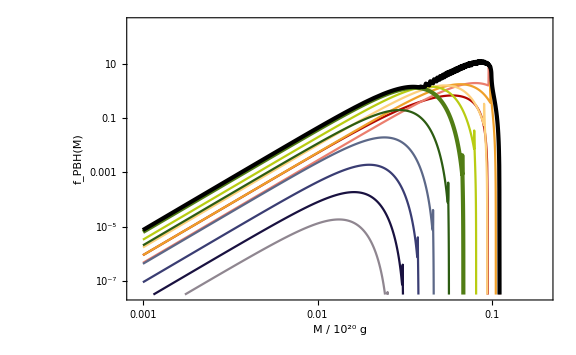

```mathematica
FigfPBH=Show[ListLogLogPlot[fPBHNList,PlotStyle->{ColorData[10,"ColorList"][[1]],ColorData[10,"ColorList"][[2]],ColorData[10,"ColorList"][[3]],ColorData[10,"ColorList"][[4]],ColorData[10,"ColorList"][[5]],{ColorData[10,"ColorList"][[6]],AbsoluteThickness[3]},ColorData[10,"ColorList"][[7]],ColorData[10,"ColorList"][[8]],ColorData[10,"ColorList"][[9]],ColorData[10,"ColorList"][[10]],ColorData[10,"ColorList"][[11]]},InterpolationOrder->1,PlotRange->{{0.0009,0.2},{10^-7.5,10^2.5}},FrameLabel->{{Subscript[f, PBH][M],None},{Row[{M," / 10^20 g"}],μ==1/3}}],
LogLogPlot[fPBHint[M],{M,MPBHmin,MPBHmax},PlotStyle->{Black,AbsoluteThickness[3]},PlotRange->{{0.0009,0.2},{10^-7.5,10^2.5}}]]
```

```mathematica
Export["fPBH.pdf",FigfPBH];
```

```mathematica
NIntegrate[fPBHint[M]/M,{M,MPBHmin,MPBHmax}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {0.0809102}. NIntegrate obtained 6.77826 and 0.0209827 for the integral and error estimates.

6.77826

#### PBH by power spectrum

```mathematica
((1-x)μ)^4/6+μ^4/6(1-(1-x)^4)//Simplify
```

μ^4/6

```mathematica
calPz[Nbw_]:=π μs^2/3 NIntegrate[(1-x)^2(5x-2)EllipticThetaPrime[2,π/2 x,Exp[-π^2 Nbw/μs^2]],{x,0,1}]
```

```mathematica
calPz[7 10^-3]
```

0.0300656

```mathematica
dlogN=10^-2;
```

```mathematica
calPzList=Table[{10^logNbw,Re[calPz[10^logNbw]]},{logNbw,-8,0,dlogN}];
```

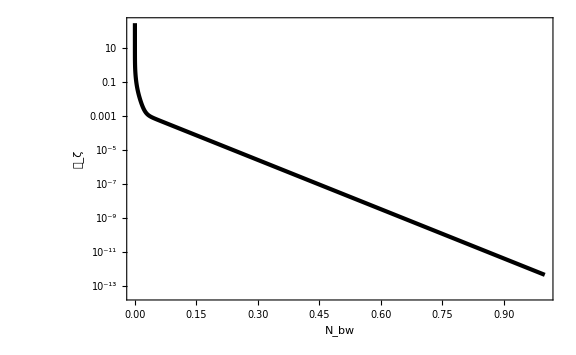

```mathematica
ListLogPlot[calPzList,PlotRange->Full,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],μ==1/3}},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
calPzint[Nbw_]=Interpolation[calPzList][Nbw];
```

```mathematica
NIntegrate[calPzint[Nbw],{Nbw,10^-8,1}]
μs^4/6//N
```

0.00205205

0.00205761

### flat well PBH (GfFTHg)

```mathematica
xt2well[xt1_,dz_,μ_,β_]=Sqrt[xt1^2-2/μ^2(dz-Log[1+β])];
xt2cl[N1_,dz_,μ_,β_]=Sqrt[2]/μ Sqrt[Log[1+β]-dz-N1];
```

```mathematica
Clear[P1,P2]
```

```mathematica
P1[dz_,μ_,α_,β_,Nbw_]:=π/(4 μ^2)NIntegrate[(1-xt1)/xt2well[xt1,dz,μ,β] EllipticThetaPrime[1,-π/2 xt2well[xt1,dz,μ,β],Exp[-π^2/μ^2(Nbw+Log[α])]]
(EllipticTheta[2,-π/2(xt1-xt2well[xt1,dz,μ,β]),Exp[-π^2/μ^2 Log[1+β]]]
+EllipticTheta[2,π/2(xt1+xt2well[xt1,dz,μ,β]),Exp[-π^2/μ^2 Log[1+β]]]),{xt1,Sqrt[Max[0,2/μ^2(dz-Log[1+β])]],Min[1,Sqrt[1+2/μ^2(dz-Log[1+β])]]},WorkingPrecision->15,MaxRecursion->20]/;Log[1+β]-μ^2/2<dz<Log[1+β]+μ^2/2
P1[dz_,μ_,α_,β_,Nbw_]:=0/;!(Log[1+β]-μ^2/2<dz<Log[1+β]+μ^2/2)
```

```mathematica
P2[dz_,μ_,α_,β_,Nbw_]:=π/(4 μ^4)NIntegrate[1/xt2cl[N1,dz,μ,β] EllipticThetaPrime[1,-π/2 xt2cl[N1,dz,μ,β],Exp[-π^2/μ^2(Nbw+Log[α])]]
EllipticTheta[2,π/2 xt2cl[N1,dz,μ,β],Exp[-π^2/μ^2(Log[1+β]-N1)]],{N1,Max[0,Log[1+β]-dz-μ^2/2],Log[1+β]-Max[0,dz]},WorkingPrecision->15,MaxRecursion->20]/;-μ^2/2<dz<Log[1+β]
P2[dz_,μ_,α_,β_,Nbw_]:=0/;!(-μ^2/2<dz<Log[1+β])
```

```mathematica
αGfFTHg=Exp[-1/2 Sqrt[(π^2+6 EulerGamma^2)/2]]/Sqrt[2];αGfFTHg//N
βGfFTHg=Exp[Sqrt[(π^2+6 EulerGamma^2)/2]]-1;βGfFTHg//N
γGfFTHg=Sqrt[2/(π^2+6 EulerGamma^2)];γGfFTHg//N
```

0.209172

10.4278

0.410501

```mathematica
dzmin[μ_]=-μ^2/2;
dzmax[μ_]=Log[1+βGfFTHg]+μ^2/2;
```

```mathematica
dzmax[1/3]//N
```

2.4916

#### sample

```mathematica
dzreg=5 10^-4;
ddz=10^-3;
```

```mathematica
P1Listp53=ParallelTable[{dz,P1[dz,1/2,αGfFTHg,βGfFTHg,3]//Quiet},{dz,dzmin[1/2]+dzreg,dzmax[1/2],ddz}];//AbsoluteTiming
P2Listp53=ParallelTable[{dz,P2[dz,1/2,αGfFTHg,βGfFTHg,3]//Quiet},{dz,dzmin[1/2]+dzreg,dzmax[1/2],ddz}];//AbsoluteTiming
PListp53=Table[{P1Listp53[[i,1]],P1Listp53[[i,2]]+P2Listp53[[i,2]]},{i,Length[P1Listp53]}];
```

{1.4708,Null}

{8.01266,Null}

```mathematica
Pp53int[dz_]=Interpolation[Re[PListp53]][dz];
```

```mathematica
NIntegrate[Pp53int[dz],{dz,dzmin[1/2]+dzreg,dzmax[1/2]}]
dzmeanp53=NIntegrate[dz Pp53int[dz],{dz,dzmin[1/2]+dzreg,dzmax[1/2]}]
s2p53=NIntegrate[(dz-dzmeanp53)^2 Pp53int[dz],{dz,dzmin[1/2]+dzreg,dzmax[1/2]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {0.00071329}. NIntegrate obtained 4.47277×10^-7 and 3.32848×10^-11 for the integral and error estimates.

4.47277×10^-7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {0.00233006}. NIntegrate obtained 3.89665×10^-8 and 4.48895×10^-14 for the integral and error estimates.

3.89665×10^-8

7.97766×10^-9

```mathematica
calPz[μ_,Nbw_]=0.02 μ^2 E^(-π^2/(4 μ^2)Nbw);
```

```mathematica
calPz[1/2,3]
```

6.91872×10^-16

```mathematica
LogPlot[calPz[1/2,Nbw],{Nbw,0,10}]
```

-Graphics-

```mathematica
s2Ando[μ_,Nbw_]=Integrate[calPz[μ,Np],{Np,Nbw+Log[αGfFTHg],Nbw+Log[αGfFTHg]+Log[1+βGfFTHg]}]
```

0.00810569 ⅇ^(-(π^2 (4 Nbw+√(2 (6 EulerGamma^2+π^2))-Log[4]))/(16 μ^2)) (-1.+ⅇ^((π^2 √(1/2 (6 EulerGamma^2+π^2)))/(4 μ^2))) μ^4

```mathematica
s2Ando[1/2,3]
```

3.56522×10^-10

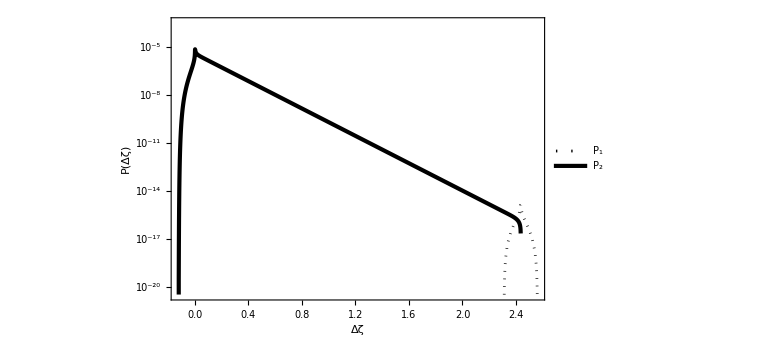

```mathematica
ListLogPlot[{P1Listp53,Re[P2Listp53]},PlotStyle->{{Dotted,Black,AbsoluteThickness[2]},{AbsoluteThickness[3],Black}},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==1/2,", ",Subscript[N, bw][R]==3}]}},PlotLegends->Placed[{Subscript[P, 1],Subscript[P, 2]},{0.8,0.8}],PlotRange->{10^-20.5,10^-3.5}]
```

```mathematica
P1Listp54=ParallelTable[{dz,P1[dz,1/2,αGfFTHg,βGfFTHg,4]//Quiet},{dz,dzmin[1/2]+dzreg,dzmax[1/2],ddz}];//AbsoluteTiming
P2Listp54=ParallelTable[{dz,P2[dz,1/2,αGfFTHg,βGfFTHg,4]//Quiet},{dz,dzmin[1/2]+dzreg,dzmax[1/2],ddz}];//AbsoluteTiming
PListp54=Table[{P1Listp54[[i,1]],P1Listp54[[i,2]]+P2Listp54[[i,2]]},{i,Length[P1Listp54]}];
```

{1.36174,Null}

{9.1328,Null}

```mathematica
P1Listp55=ParallelTable[{dz,P1[dz,1/2,αGfFTHg,βGfFTHg,5]//Quiet},{dz,dzmin[1/2]+dzreg,dzmax[1/2],ddz}];//AbsoluteTiming
P2Listp55=ParallelTable[{dz,P2[dz,1/2,αGfFTHg,βGfFTHg,5]//Quiet},{dz,dzmin[1/2]+dzreg,dzmax[1/2],ddz}];//AbsoluteTiming
PListp55=Table[{P1Listp55[[i,1]],P1Listp55[[i,2]]+P2Listp55[[i,2]]},{i,Length[P1Listp55]}];
```

{1.35003,Null}

{7.49833,Null}

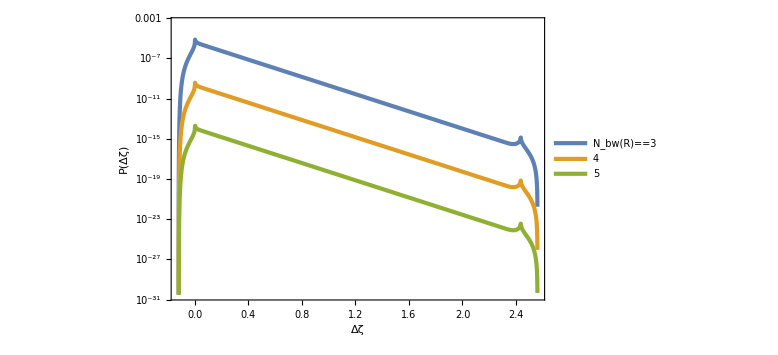

```mathematica
ListLogPlot[{PListp53,PListp54,PListp55},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==1/2}]}},PlotLegends->Placed[LineLegend[{Subscript[N, bw][R]==3,4,5},LegendLayout->"Row"],{0.4,0.15}],PlotRange->{10^-30.5,10^-3.5}]
```

```mathematica
P1List13=ParallelTable[{dz,P1[dz,1,αGfFTHg,βGfFTHg,3]//Quiet},{dz,dzmin[1]+dzreg,dzmax[1],ddz}];//AbsoluteTiming
P2List13=ParallelTable[{dz,P2[dz,1,αGfFTHg,βGfFTHg,3]//Quiet},{dz,dzmin[1]+dzreg,dzmax[1],ddz}];//AbsoluteTiming
PList13=Table[{P1List13[[i,1]],P1List13[[i,2]]+P2List13[[i,2]]},{i,Length[P1List13]}];
```

{3.98757,Null}

{40.6112,Null}

```mathematica
P1List23=ParallelTable[{dz,P1[dz,2,αGfFTHg,βGfFTHg,3]//Quiet},{dz,dzmin[2]+dzreg,dzmax[2],ddz}];//AbsoluteTiming
P2List23=ParallelTable[{dz,P2[dz,2,αGfFTHg,βGfFTHg,3]//Quiet},{dz,dzmin[2]+dzreg,dzmax[2],ddz}];//AbsoluteTiming
PList23=Table[{P1List23[[i,1]],P1List23[[i,2]]+P2List23[[i,2]]},{i,Length[P1List23]}];
```

{11.4928,Null}

{13.9724,Null}

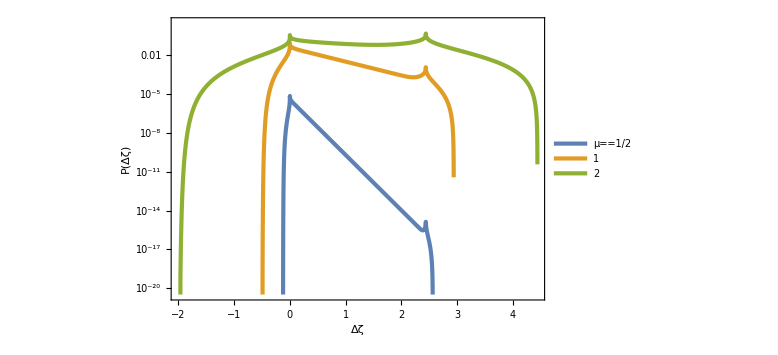

```mathematica
ListLogPlot[{PListp53,PList13,PList23},PlotRange->{10^-20.5,10^0.5},FrameLabel->{{P[Δζ],None},{Δζ,Subscript[N, bw][R]==3}},PlotLegends->Placed[LineLegend[{μ==1/2,1,2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.2}]]
```

#### PBH

```mathematica
(6 10^-3)^(1/4)//N
```

0.278316

```mathematica
1/Sqrt[6]//N
```

0.408248

```mathematica
μs=(*1/2*)(*1/3*)(*37/100*)1/Sqrt[6]
dN=10^-3(*10^-3*);
Nbwmin=-Log[αGfFTHg]-Log[1+βGfFTHg];Nbwmin//N
Nbws=-Log[αGfFTHg];Nbws//N
Nbwmax=20 μs^2+dN;Nbwmax//N
```

1/(√6)

-0.871451

1.5646

3.33433

```mathematica
μs^4/6//N
```

0.00462963

```mathematica
Clear[P,P3,P4]
```

```mathematica
x1well[dz_,μ_,α_,β_,Nbw_]=1-Sqrt[1-2/μ^2(Nbw+Log[α]+Log[1+β]-dz)];
```

```mathematica
P3[dz_,μ_,α_,β_,Nbw_]:=-(π x1well[dz,μ,α,β,Nbw])/(2 μ^2(1-x1well[dz,μ,α,β,Nbw]))EllipticThetaPrime[2,π/2 x1well[dz,μ,α,β,Nbw],E^(-π^2(Nbw+Log[α]+Log[1+β])/μ^2)]/;Nbw+Log[α]+Log[1+β]-μ^2/2<dz<Nbw+Log[α]+Log[1+β]
P3[dz_,μ_,α_,β_,Nbw_]:=0/;!(Nbw+Log[α]+Log[1+β]-μ^2/2<dz<Nbw+Log[α]+Log[1+β])
```

```mathematica
P4[dz_,μ_,α_,β_,Nbw_]:=-π/(2 μ^2)EllipticThetaPrime[2,π/2,E^(-π^2(dz+μ^2/2)/μ^2)]/;-μ^2/2<dz≤Nbw+Log[α]+Log[1+β]-μ^2/2
P4[dz_,μ_,α_,β_,Nbw_]:=0/;!(-μ^2/2<dz≤Nbw+Log[α]+Log[1+β]-μ^2/2)
```

```mathematica
P[dz_,μ_,α_,β_,Nbw_]:=P1[dz,μ,α,β,Nbw]+P2[dz,μ,α,β,Nbw]/;Nbw>Nbws
P[dz_,μ_,α_,β_,Nbw_]:=P3[dz,μ,α,β,Nbw]+P4[dz,μ,α,β,Nbw]/;Nbw≤Nbws
```

```mathematica
LogPmin=-50;
ddz=10^-3(*10^-3*);
```

```mathematica
Nbws//N
Nbwmin//N
Nbwmin+1913dN//N
```

1.5646

-0.871451

1.04155

```mathematica
ParallelTable[{dz,Log10[Max[Re[P[dz,μs,αGfFTHg,βGfFTHg,0.9Nbwmax(*Nbws+10^-3*)(*Nbwmin+1913dN*)]],10^LogPmin]]//N},{dz,dzmin[μs]+2ddz,dzmax[μs],ddz}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{-61/750,-24.0555},{-241/3000,-20.2803},{-119/1500,-18.2607},{-47/600,-16.9661},{-29/375,-16.0491},{-229/3000,-15.3564},2590,{943/375,-27.105},{7547/3000,-27.3666},{151/60,-27.7097},{7553/3000,-28.211},{1889/750,-29.1628}}
 |  |  |  |

```mathematica
LogPList=Join[Flatten[ParallelTable[{Nbw//N,dz,Log10[Max[Re[P[dz,μs,αGfFTHg,βGfFTHg,Nbw]//Quiet],10^LogPmin]//N]},{Nbw,Nbwmin+dN,Nbws,dN},{dz,dzmin[μs]+2ddz,dzmax[μs],ddz}],1],
Flatten[ParallelTable[{Nbw//N,dz,Log10[Max[Re[P[dz,μs,αGfFTHg,βGfFTHg,Nbw]//Quiet],10^LogPmin]//N]},{Nbw,Nbws+dN,Nbwmax,dN},{dz,dzmin[μs]+2ddz,dzmax[μs],ddz}],1]];//AbsoluteTiming
```

{10280.9,Null}

```mathematica
Export["LogPmuinvrt6G.dat",LogPList];
```

```mathematica
LogPList=Import["LogPmuinvrt6G.dat"]//ToExpression;//AbsoluteTiming
```

{131.431,Null}

```mathematica
Pint[Nbw_,dz_]=10^(Interpolation[LogPList,InterpolationOrder->1][Nbw,dz]);
```

```mathematica
Nbwmin+dN//N
Nbwmax//N
```

-0.870451

3.33433

```mathematica
dzth=dz/.Solve[(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)==dth,dz][[2]]/.{dth->1/3(*0.59*),w->1/3,γ->γGfFTHg};dzth//N
dzlim=dz/.Solve[(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)==dth,dz][[1]]/.{dth->1/3(*0.59*),w->1/3,γ->γGfFTHg};dzlim//N
```

2.14051

12.4758

```mathematica
Simplify[Solve[(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)==dth,dz]/.{w->1/3},{γ>0}]
```

{{dz→(6+3 √(4-6 dth))/(2 γ)},{dz→(6-3 √(4-6 dth))/(2 γ)}}

```mathematica
γGfFTHg//N
```

0.410501

```mathematica
(6-3 √(4-6 dth))/(2 γ)/.{dth->1/3(*0.59*),γ->γGfFTHg}//N
(6+3 √(4-6 dth))/(2 γ)/.{dth->1/3(*0.59*),γ->γGfFTHg}//N
```

2.14051

12.4758

```mathematica
dzmax[μs]//N
```

2.51938

```mathematica
βGfFTHg//N
```

10.4278

```mathematica
Nbwmin//N
Nbws//N
Nbwmax//N
```

-0.871451

1.5646

3.33433

```mathematica
PintListn=Reverse[Table[Pint[Nbw,dz],{Nbw,Nbwmin+dN,Nbws,(Nbws-Nbwmin-dN)/10}]];
PintListp=Table[Pint[Nbw,dz],{Nbw,Nbws+dN,Nbwmax-dN,(Nbwmax-dN-Nbws-dN)/10}];
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

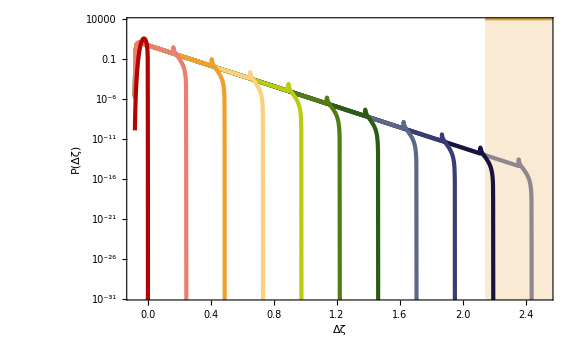

```mathematica
Show[LogPlot[10^-50,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotRange->{10^-30.5,10^3.5},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==μs,", ",Subscript[N, bw]^("(2)")<0}]}}],
LogPlot[10^4 UnitStep[dz-dzth,dzlim-dz],{dz,dzmin[μs],dzmax[μs]+1},Filling->Bottom,PlotRange->{10^-50,10^4},PlotStyle->Color[2]],
LogPlot[PintListn,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotStyle->Map[{AbsoluteThickness[3],#}&,Reverse[ColorData[10,"ColorList"]]]]]
```

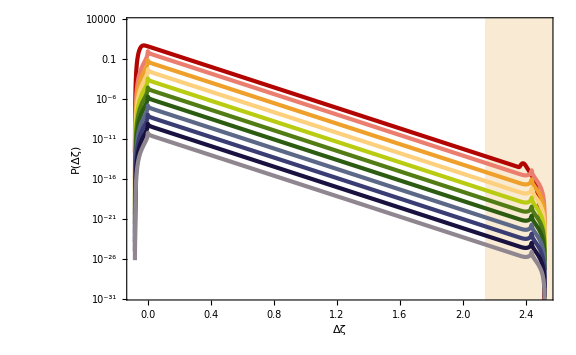

```mathematica
Show[LogPlot[10^-50,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotRange->{10^-30.5,10^3.5},FrameLabel->{{P[Δζ],None},{Δζ,Row[{μ==μs,", ",Subscript[N, bw]^("(2)")>0}]}}],
LogPlot[10^10 UnitStep[dz-dzth,dzlim-dz],{dz,dzmin[μs],dzmax[μs]+1},Filling->Bottom,PlotRange->{10^10,10^-50},PlotStyle->Color[2]],
LogPlot[PintListp,{dz,dzmin[μs]+2ddz,dzmax[μs]},PlotStyle->Map[{AbsoluteThickness[3],#}&,ColorData[10,"ColorList"]]]]
```

```mathematica
dzmin[μs]//N
```

-0.0833333

```mathematica
NIntegrate[Pint[Min[Nbws,Nbwmax],dz],{dz,dzmin[μs]+2ddz,dzmax[μs]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {-0.07327287276838626538244536590127609088085591793060302734375}. NIntegrate obtained 0.945841 and 0.0000135801 for the integral and error estimates.

0.945841

```mathematica
P[dzth,μs,αGfFTHg,βGfFTHg,Min[Nbws,Nbwmax]]//N
```

9.48817×10^-14

```mathematica
dzmean=NIntegrate[dz Pint[Min[Nbws,Nbwmax],dz],{dz,dzmin[μs],dzmax[μs]}]
var=NIntegrate[(dz-dzmean)^2 Pint[Min[Nbws,Nbwmax],dz],{dz,dzmin[μs],dzmax[μs]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {-0.07526667412093052990373909238996930071152746677398681640625}. NIntegrate obtained 0.00236867 and 1.18012×10^-6 for the integral and error estimates.

0.00236867

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dz near {dz} = {-0.06533195437394832827404655972713953815400600433349609375}. NIntegrate obtained 0.00440977 and 4.40333×10^-8 for the integral and error estimates.

0.00440977

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
(κ 10^20 gineV (1.56 10^13 MpcinvineV)^3)/(4π p MplineV^2 0.12 (100kminvsinvMpcineV)^2)/.{κ->(*3.3*)1,p->0.36}
```

3.80015×10^15

```mathematica
norm=((κ 10^20 gineV (1.56 10^13 MpcinvineV)^3)/(4π p MplineV^2 0.12 (100kminvsinvMpcineV)^2)/.{κ->(*3.3*)1,p->0.36})^-1
```

2.63148×10^-16

```mathematica
CompactC[dz_]=(3(1+w))/(5+3w)(1-(1-γ/3 dz)^2)/.{w->1/3,γ->γGfFTHg}
```

2/3 (1-(1-1/3 dz √(2/(6 EulerGamma^2+π^2)))^2)

```mathematica
NbwPBH=dzth-Log[αGfFTHg]-Log[1+βGfFTHg];NbwPBH//N
```

1.26906

```mathematica
fPBHN[Nbw_,dz_]=1/norm E^-Nbw(CompactC[dz]-dth)^(p+1)Pint[Nbw,dz]/.{dth->1/3(*0.59*),p->0.36};
MPBHN20[Nbw_,dz_]=κ E^(2Nbw)(CompactC[dz]-dth)^p/.{κ->1(*3.3*),p->0.36,dth->1/3(*0.59*)};
```

```mathematica
dlogddz=10^-2(*10^-3*);
logddzmin=-7;
```

```mathematica
fPBHNfixList=Table[{MPBHN20[(*NbwPBH+3dN*)(*Nbws*)Nbwmax-2dN,dzth+10^logddz],fPBHN[(*NbwPBH+3dN*)(*Nbws*)Nbwmax-2dN,dzth+10^logddz]},{logddz,logddzmin,Log10[dzmax[μs]-ddz-dzth],dlogddz}];
```

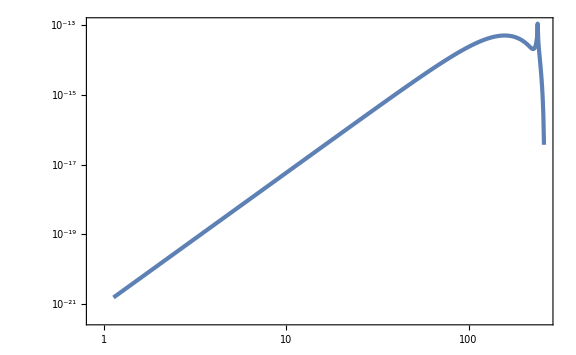

```mathematica
ListLogLogPlot[fPBHNfixList,GridLines->{None,{1}}]
```

```mathematica
LogfPBHNList=Table[{Nbw//N,Log10[MPBHN20[Nbw,dzth+10^logddz]],Log10[fPBHN[Nbw,dzth+10^logddz]//Quiet]},{Nbw,NbwPBH+dN,Nbwmax,dN},{logddz,logddzmin,Log10[dzmax[μs]-dzth],dlogddz}];//AbsoluteTiming
```

{314.818,Null}

```mathematica
Length[LogfPBHNList]
Ceiling[(Nbwmax-NbwPBH-dN)/dN]
Length[LogfPBHNList[[1]]]
Ceiling[(Log10[dzmax[μs]-dzth]-logddzmin)/dlogddz]
```

2065

2065

658

658

```mathematica
LogfPBHNList[[1,1]]
```

{1.27006,-3.94333,-12.6469}

```mathematica
Flatten[LogfPBHNList,1][[Ceiling[(Log10[dzmax[μs]-dzth]-logddzmin)/dlogddz]+1]]
```

{1.27106,-3.9442,-11.8791}

```mathematica
Flatten[Partition[Flatten[LogfPBHNList,1],{Ceiling[(Log10[dzmax[μs]-dzth]-logddzmin)/dlogddz],3}],1][[1,1]]
```

{1.27006,-3.94333,-12.6469}

```mathematica
Flatten[Partition[Flatten[LogfPBHNList,1],{Ceiling[(Log10[dzmax[μs]-dzth]-logddzmin)/dlogddz],3}],1]-LogfPBHNList
```

{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},635,{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},2064}
 |  |  |  |

```mathematica
Export["LogfPBHNinvrt6G.dat",Flatten[LogfPBHNList,1]];
```

```mathematica
LogfPBHNList=Flatten[Partition[Import["LogfPBHNinvrt6G.dat"]//ToExpression,{Ceiling[(Log10[dzmax[μs]-dzth]-logddzmin)/dlogddz],3}],1];//AbsoluteTiming
```

{14.2525,Null}

```mathematica
Logfmin=-50;
```

```mathematica
LogfPBHNintList[MPBH_]=Table[(Interpolation[LogfPBHNList[[i]].Transpose[{{0,1,0},{0,0,1}}],InterpolationOrder->1][Log10[MPBH]]-Logfmin )UnitStep[Log10[MPBH]-First[LogfPBHNList[[i]]][[2]],Last[LogfPBHNList[[i]]][[2]]-Log10[MPBH]]
+Logfmin,{i,Length[LogfPBHNList]}];
```

```mathematica
MPBHmin=10^-2(*10^-4*);
MPBHmax=200(*5 10^-2*);
```

```mathematica
LogfPBHList=Table[{logM,Max[LogfPBHNintList[10^logM]]},{logM,Log10[MPBHmin],Log10[MPBHmax],10^-3}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-Log[100]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{240.422,Null}

```mathematica
Export["LogfPBHinvrt6G.dat",LogfPBHList];
```

```mathematica
LogfPBHList=Import["LogfPBHinvrt6G.dat"]//ToExpression;
```

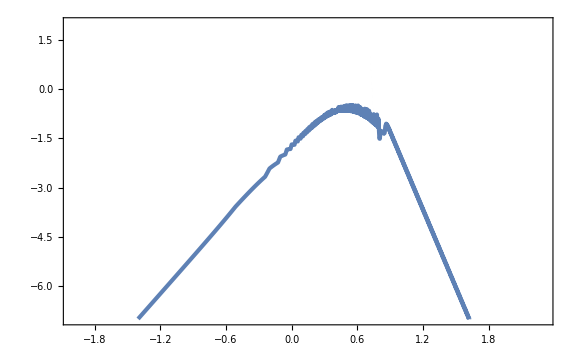

```mathematica
ListPlot[LogfPBHList,PlotRange->{-7,2}]
```

```mathematica
fPBHint[M_]=10^(Interpolation[LogfPBHList,InterpolationOrder->1][Log10[M]]);
```

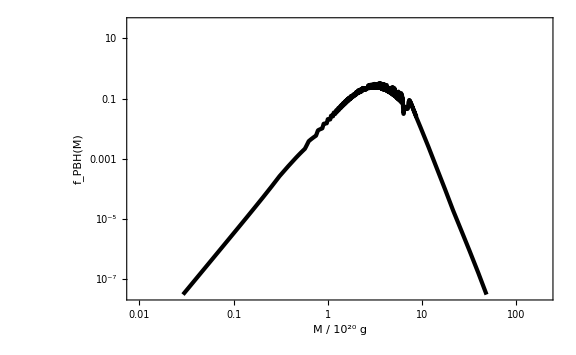

```mathematica
LogLogPlot[fPBHint[M],{M,MPBHmin,MPBHmax},PlotRange->{{9 10^-3,200},{10^-7.5,10^1.5}},PlotStyle->{Black,AbsoluteThickness[3]},FrameLabel->{Row[{M," / 10^20 g"}],Subscript[f, PBH][M]}]
```

```mathematica
Length[LogfPBHNList]
```

2065

```mathematica
(Nbws-NbwPBH-dN)/dN//N
```

294.542

```mathematica
(295-82)/5//N
```

42.6

```mathematica
fPBHNList=(*Table[Map[{10^(#[[2]]),10^(#[[3]])}&,Select[LogfPBHNList[[i]],#[[2]]>Log10[MPBHmin]&]],{i,55,855(*53,1053*),80}]*)Join[Table[Map[{10^(#[[2]]),10^(#[[3]])}&,LogfPBHNList[[i]]],{i,{82 ,100,150,210,295}}],
Table[Map[{10^(#[[2]]),10^(#[[3]])}&,LogfPBHNList[[i]]],{i,295+100,295+100 7,100}]];
```

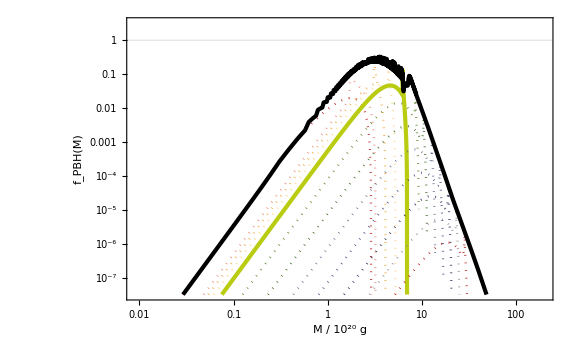

```mathematica
FigfPBH=Show[ListLogLogPlot[fPBHNList,PlotStyle->{{ColorData[10,"ColorList"][[1]],Dotted},{ColorData[10,"ColorList"][[2]],Dotted},{ColorData[10,"ColorList"][[3]],Dotted(*,AbsoluteThickness[3]*)},{ColorData[10,"ColorList"][[4]],Dotted(*,AbsoluteThickness[3]*)},{ColorData[10,"ColorList"][[5]],(*Dotted*)AbsoluteThickness[3]},{ColorData[10,"ColorList"][[6]],Dotted(*AbsoluteThickness[3]*)},{ColorData[10,"ColorList"][[7]],Dotted},{ColorData[10,"ColorList"][[8]],Dotted},{ColorData[10,"ColorList"][[9]],Dotted},{ColorData[10,"ColorList"][[10]],Dotted},{ColorData[10,"ColorList"][[11]],Dotted}},InterpolationOrder->1,PlotRange->{{9 10^-3,200},{10^-7.5,10^0.5}},FrameLabel->{{Subscript[f, PBH][M],None},{Row[{M," / 10^20 g"}],μ==μs}},GridLines->{None,{1}}],
LogLogPlot[fPBHint[M],{M,MPBHmin,MPBHmax},PlotStyle->{Black,AbsoluteThickness[3]},PlotRange->{{9 10^-3,200},{10^-7.5,10^0.5}}]]
```

```mathematica
NIntegrate[fPBHint[M]/M,{M,MPBHmin,MPBHmax}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in M near {M} = {0.00906563}. NIntegrate obtained 0.144097 and 0.000214373 for the integral and error estimates.

0.144097

#### PBH by power spectrum

```mathematica
((1-x)μ)^4/6+μ^4/6(1-(1-x)^4)//Simplify
```

μ^4/6

```mathematica
calPz[Nbw_]:=π μs^2/3 NIntegrate[(1-x)^2(5x-2)EllipticThetaPrime[2,π/2 x,Exp[-π^2 Nbw/μs^2]],{x,0,1}]
```

```mathematica
calPz[7 10^-3]
```

0.0884526

```mathematica
dlogN=10^-2;
```

```mathematica
calPzList=Table[{10^logNbw,Re[calPz[10^logNbw]]},{logNbw,-8,0,dlogN}];
```

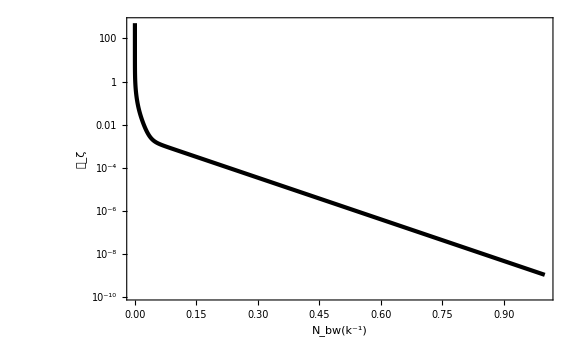

```mathematica
ListLogPlot[calPzList,PlotRange->Full,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw]["k^-1"],μ==μs}},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
calPzint[Nbw_]=Interpolation[calPzList][Nbw];
```

```mathematica
NIntegrate[calPzint[Nbw],{Nbw,10^-8,1}]
μs^4/6//N
```

0.0046194

0.00462963

#### fNL

```mathematica
xm=2.74;
```

```mathematica
(*WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);*)
WG[z_]=Exp[-z^2/2];
```

```mathematica
sX[A_]=4/9 xm^2(*WRTH[xm]*)WG[xm]Sqrt[A]
sY[A_,fNL_]=6/4 fNL Sinc[xm]Sqrt[A]
```

0.0781743 √A

0.213988 √A fNL

```mathematica
PfNL[dl_,A_,fNL_]=1/Sqrt[2π sX[A]^2](Exp[(-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)]+Exp[(-((-sX[A]-Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)])//Simplify
PGauss[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[Normal[Series[-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2,{fNL,0,0}]]/(2 sX[A]^2)]//Simplify
```

(5.10324 (ⅇ^(-(446.687 (-0.0781743 √A+√(A (0.00611122+0.0669135 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(446.687 (0.0781743 √A+√(A (0.00611122+0.0669135 dl fNL)))^2)/(A^2 fNL^2))))/(√A)

(5.10324 ⅇ^(-(81.8167 dl^2)/A))/(√A)

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
(1/0.12 1/(2(Sqrt[2]-1)(106.75/3.38)^(1/6))1/(0.07 2.74/(1.56 10^13)))^-1
```

2.17304×10^-15

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->(*0.587*)1/3}
β[dl_,A_,fNL_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PfNL[dl,A,fNL]/.{KK->1,γ->0.36,Cth->(*0.587*)1/3}
βGauss[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PGauss[dl,A]/.{KK->1,γ->0.36,Cth->(*0.587*)1/3}
fPBHPS[dl_,A_,fNL_]=β[dl,A,fNL]/(6.88 10^-16);
fPBHPSGauss[dl_,A_]=βGauss[dl,A]/(6.88 10^-16);
```

7.5076 (-1/3+dl-(3 dl^2)/8)^0.36

(14.1757 (-1/3+dl-(3 dl^2)/8)^1.36 (ⅇ^(-(446.687 (-0.0781743 √A+√(A (0.00611122+0.0669135 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(446.687 (0.0781743 √A+√(A (0.00611122+0.0669135 dl fNL)))^2)/(A^2 fNL^2))))/(√A (1-(3 dl)/4))

(14.1757 (-1/3+dl-(3 dl^2)/8)^1.36 ⅇ^(-(81.8167 dl^2)/A))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->1/3}
dlmax=4/3;
```

4/3 (1-1/(√2))

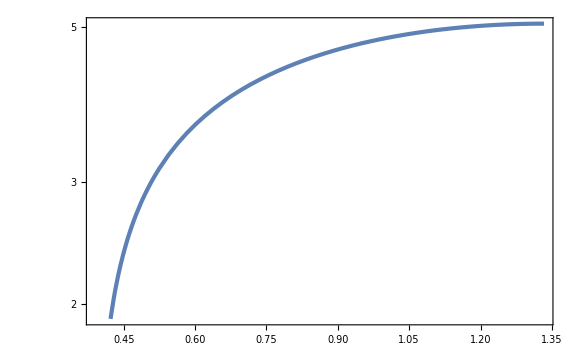

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

```mathematica
fPBHPSListfNL0=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPSGauss[dlth+10^logdl,10^logA]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL5h=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,5/2]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{7.13091,Null}

{9.83205,Null}

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

5.05519

0.00166462

```mathematica
fPBHPSintfNL0[M_,A_]=Interpolation[fPBHPSListfNL0][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL5h[M_,A_]=Interpolation[fPBHPSListfNL5h][M,A]UnitStep[Mmax-M,M-Mmin];
```

InterpolatingFunction::dmval: Input value {5.05519,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.05519,1/100} lies outside the range of data in the interpolating function. Extrapolation will be used.

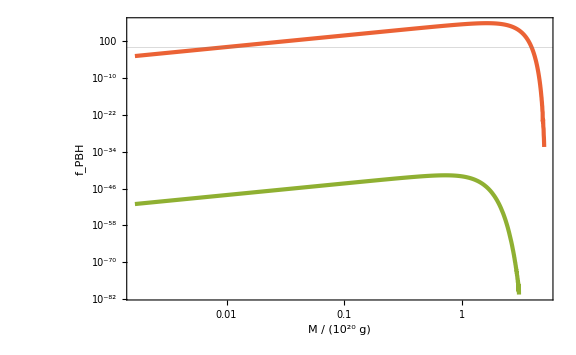

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,10^-3],fPBHPSintfNL0[M,10^-2],fPBHPSintfNL0[M,10^-1],fPBHPSintfNL0[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {5.05519,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

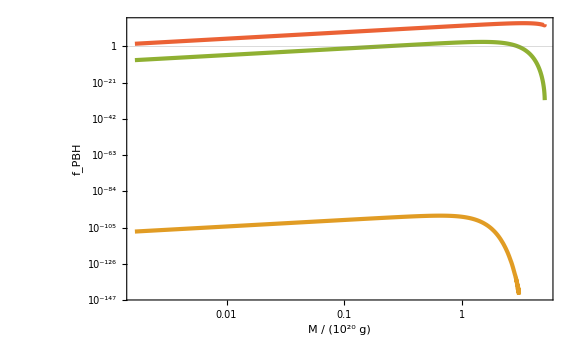

```mathematica
LogLogPlot[{fPBHPSintfNL5h[M,10^-3],fPBHPSintfNL5h[M,10^-2],fPBHPSintfNL5h[M,10^-1],fPBHPSintfNL5h[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
fPBHAPSListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL0[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL5h=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL5h[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.96811,Null}

{10.4674,Null}

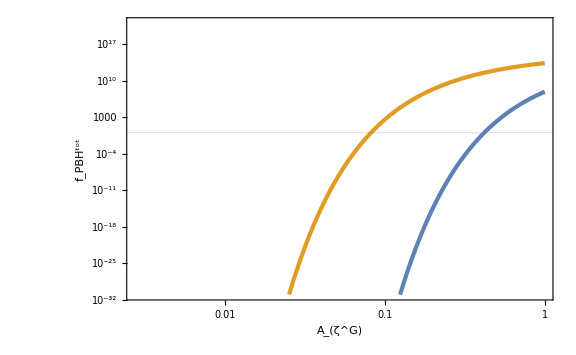

```mathematica
ListLogLogPlot[{fPBHAPSListfNL0,fPBHAPSListfNL5h},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{10^-31,10^21}},GridLines->{None,{1}}]
```

```mathematica
fPBHAPSintfNL0[A_]=Interpolation[fPBHAPSListfNL0][A];
fPBHAPSintfNL5h[A_]=Interpolation[fPBHAPSListfNL5h][A];
```

```mathematica
A1PSfNL0=A/.FindRoot[Log10[fPBHAPSintfNL0[A]]==0,{A,0.1}]
A1PSfNL5h=A/.FindRoot[Log10[fPBHAPSintfNL5h[A]]==0,{A,0.1}]
```

0.417764

0.0818378

InterpolatingFunction::dmval: Input value {0.000100024,0.417764} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.417764} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.417764} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

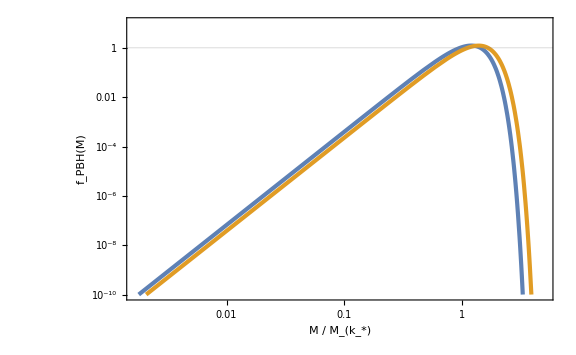

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,A1PSfNL0],fPBHPSintfNL5h[M,A1PSfNL5h]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10}]
```

#### exp-tail

```mathematica
xm=2.74;
```

```mathematica
(*WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);*)
WG[z_]=Exp[-z^2/2];
```

```mathematica
sX[A_]=4/9 xm^2(*WRTH[xm]*)WG[xm]Sqrt[A]
sYp[A_]=3Sinc[xm]Sqrt[A]
```

0.0781743 √A

0.427976 √A

```mathematica
Pexp[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[(-((sX[A]dl)/(sX[A]+sYp[A]dl))^2)/(2 sX[A]^2)]//Simplify
```

(5.10324 ⅇ^(-(2.7298 dl^2)/(A (0.18266+1. dl)^2)))/(√A)

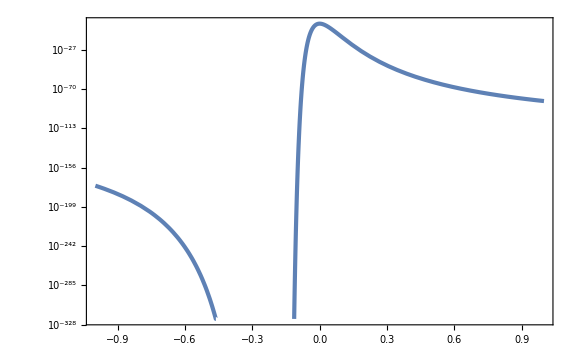

```mathematica
LogPlot[Pexp[dl,10^-2],{dl,-1,1}]
```

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->(*0.587*)1/3}
β[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))Pexp[dl,A]/.{KK->1,γ->0.36,Cth->(*0.587*)1/3}
fPBHPS[dl_,A_]=β[dl,A]/(6.88 10^-16);
```

7.5076 (-1/3+dl-(3 dl^2)/8)^0.36

(14.1757 (-1/3+dl-(3 dl^2)/8)^1.36 ⅇ^(-(2.7298 dl^2)/(A (0.18266+1. dl)^2)))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->(*0.587*)1/3}
dlmax=4/3;
```

4/3 (1-1/(√2))

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

-Graphics-

```mathematica
fPBHPSList=Flatten[Table[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA]},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

General::munfl: Exp[-12671.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12383.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12101.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{25.9768,Null}

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

5.05519

0.00166462

```mathematica
fPBHPSint[M_,A_]=Interpolation[fPBHPSList][M,A]UnitStep[Mmax-M,M-Mmin];
```

InterpolatingFunction::dmval: Input value {5.05519,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

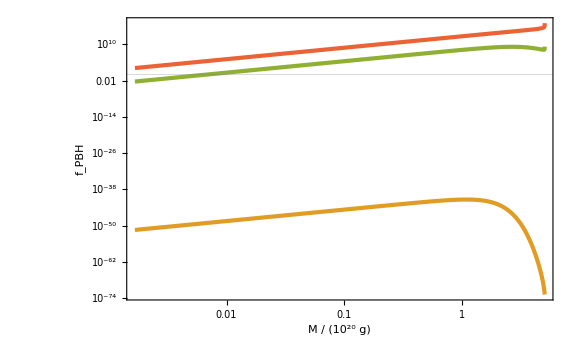

```mathematica
LogLogPlot[{fPBHPSint[M,10^-3],fPBHPSint[M,10^-2],fPBHPSint[M,10^-1],fPBHPSint[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
fPBHAPSList=ParallelTable[{10^logA,NIntegrate[fPBHPSint[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{10.206,Null}

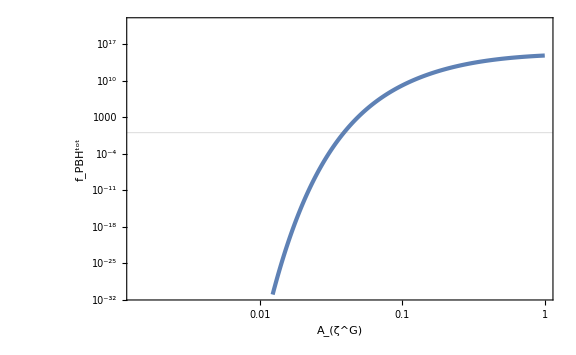

```mathematica
ListLogLogPlot[fPBHAPSList,FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{10^-31,10^21},GridLines->{None,{1}}]
```

```mathematica
fPBHAPSint[A_]=Interpolation[fPBHAPSList][A];
```

```mathematica
A1PS=A/.FindRoot[Log10[fPBHAPSint[A]]==0,{A,0.01}]
```

0.0388695

InterpolatingFunction::dmval: Input value {0.000100024,0.0388695} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.0388695} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.0388695} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

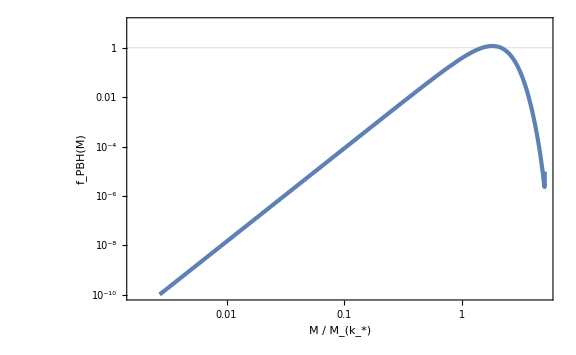

```mathematica
LogLogPlot[fPBHPSint[M,A1PS],{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10}]
```

### Window

#### preamble

```mathematica
(3(1+w))/(5+3w)/.{w->1/3}//Simplify
```

2/3

```mathematica
Log[1+β]/.{β->11.72}
```

2.54318

```mathematica
$Assumptions={zmax>0,z>0,α>0,β>0,γ>0};
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
WG[z_]=Exp[-z^2/2];
WFTH[z_]=UnitStep[1-z];
```

```mathematica
z^2 WRTH''[z]+4z WRTH'[z]+z^2 WRTH[z]//Simplify
```

0

```mathematica
ff[z_]=WRTH[z]WRTH[z/Sqrt[3]]//Simplify
```

(9 √3 (z Cos[z]-Sin[z]) (√3 z Cos[z/(√3)]-3 Sin[z/(√3)]))/z^6

```mathematica
z^2 ff''[z]+4z ff'[z]//Simplify
```

(18 (z Cos[z] ((27 z-2 z^3) Cos[z/(√3)]+√3 (-27+5 z^2) Sin[z/(√3)])+Sin[z] (z (-27+11 z^2) Cos[z/(√3)]+√3 (27-14 z^2+z^4) Sin[z/(√3)])))/z^6

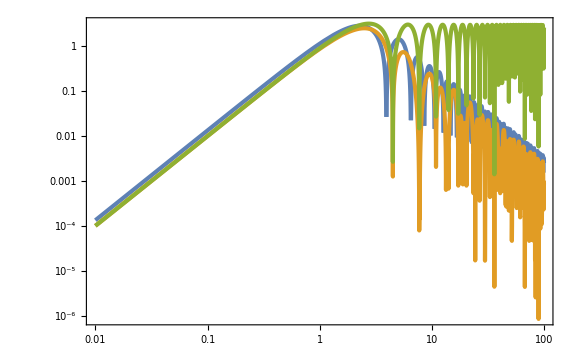

```mathematica
LogLogPlot[{Abs[z^2 ff''[z]+4z ff'[z]],Abs[z^2 ff[z]],Abs[z^2 WRTH[z]]},{z,0.01,100}]
```

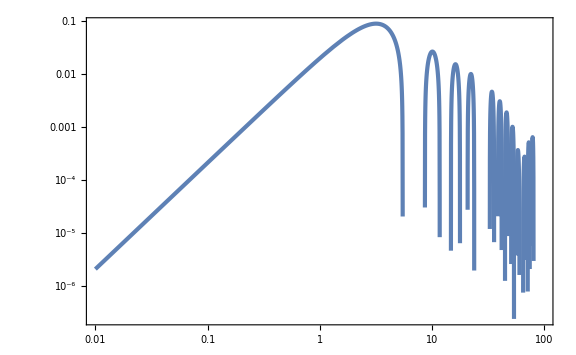

```mathematica
LogLogPlot[WRTH[z]-WRTH[1.1z],{z,0.01,100}]
```

```mathematica
fRTH[z_]=z^2 WRTH[z]WRTH[z/Sqrt[3]]//Simplify;
fG[z_]=z^2 WG[z];
fFTH[z_]=z^2 WFTH[z];
```

```mathematica
gRTH[z_]=γ(WRTH[α z]-WRTH[α(1+β)z]);
gG[z_]=γ(WG[α z]-WG[α(1+β)z]);
gFTH[z_]=γ(WFTH[α z]-WFTH[α(1+β)z]);
```

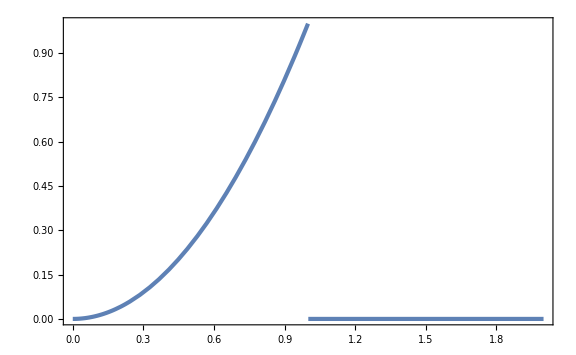

```mathematica
Plot[fFTH[z],{z,0,2}]
```

```mathematica
zmaxFTHf=1;
```

```mathematica
s2FTHf=Integrate[fFTH[z](Log[z]-Log[zmaxFTHf])^2 1/z,{z,0,∞}]
```

1/4

```mathematica
VFTHf=Integrate[fFTH[z]/z,{z,0,∞}]
```

1/2

```mathematica
zmaxFTHg=Sqrt[1/(α(1+β))1/α](*(1/(α(1+β))+1/α)/2*)//Simplify
```

1/(α √(1+β))

```mathematica
s2FTHg=Integrate[γ(logz-Log[zmaxFTHg])^2,{logz,-Log[α]-Log[1+β],-Log[α]}]//FullSimplify
```

1/12 γ Log[1+β]^3

```mathematica
VFTHg=Integrate[γ,{logx,-Log[α]-Log[1+β],-Log[α]}]
```

γ Log[1+β]

```mathematica
zmaxGf=z/.Solve[fG'[z]==0,z][[1]]
```

√2

```mathematica
s2Gf=Integrate[fG[z](Log[z]-Log[zmaxGf])^2 1/z,{z,0,∞}]
```

1/24 (6 EulerGamma^2+π^2)

```mathematica
VGf=Integrate[fG[z]/z,{z,0,∞}]
```

1

```mathematica
zmaxGg=z/.Solve[gG'[z]==0,z][[1]]//Simplify
```

(2 √(Log[1+β]/(β (2+β))))/α

```mathematica
s2Ggpre=Integrate[gG[z] Log[z]^2 1/z,{z,0,∞}]-2Log[zmax]Integrate[gG[z]Log[z] 1/z,{z,0,∞}]+Log[zmax]^2 Integrate[gG[z] 1/z,{z,0,∞}];//AbsoluteTiming
```

{59.4783,Null}

```mathematica
s2Gg=s2Ggpre/.{zmax->zmaxGg}//FullSimplify
```

1/24 γ Log[1+β] (6 EulerGamma^2+π^2+6 Log[2]^2-4 Log[8] Log[1+β]+8 Log[1+β]^2+6 (2 EulerGamma Log[(1+β)/2]+2 (EulerGamma+Log[(1+β)/2]) Log[(4 Log[1+β])/(β (2+β))]+Log[(4 Log[1+β])/(β (2+β))]^2))

```mathematica
VGg=Integrate[gG[z]/z,{z,0,∞}]
```

γ Log[1+β]

```mathematica
fRTH'[z]//Simplify
```

-(9 √3 (z Cos[z] (4 √3 z Cos[z/(√3)]+(-12+z^2) Sin[z/(√3)])+Sin[z] (√3 z (-4+z^2) Cos[z/(√3)]-4 (-3+z^2) Sin[z/(√3)])))/z^5

```mathematica
VRTHf=Integrate[fRTH[z]/z,{z,0,∞}]
```

1/2 (9-3 √3 ArcCoth[√3])

```mathematica
fRTHex=Simplify[fRTH'[z]==0]
```

z Cos[z] (4 √3 z Cos[z/(√3)]+(-12+z^2) Sin[z/(√3)])+Sin[z] (√3 z (-4+z^2) Cos[z/(√3)]-4 (-3+z^2) Sin[z/(√3)])==0

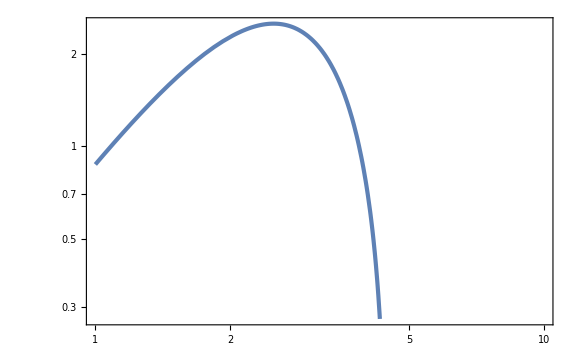

```mathematica
LogLogPlot[fRTH[z],{z,1,10}]
```

```mathematica
zmaxRTHf=z/.FindRoot[fRTHex,{z,3}]
```

2.49691

```mathematica
s2RTHf=NIntegrate[fRTH[z](Log[z]-Log[zmaxRTHf])^2 1/z,{z,0,10^4},WorkingPrecision->30]
```

NIntegrate::precw: The precision of the argument function ((9 √3 (-0.915052+Log[z])^2 (z Cos[z]-Sin[z]) (√3 z Cos[z/(√3)]-3 Sin[z/(√3)]))/z^5) is less than WorkingPrecision (30.).

1.29885746871598765753038333335

```mathematica
VRTHg=Integrate[gRTH[z]/z,{z,0,∞}]
```

γ Log[1+β]

```mathematica
gRTHex[z_]=1/(3α γ z^2)gRTH'[z/α]//Simplify
```

(3 z Cos[z]-3 Sin[z]+z^2 Sin[z]-(z^2 Sin[z+z β])/(1+β)+(3 (-z (1+β) Cos[z+z β]+Sin[z+z β]))/(1+β)^3)/z^6

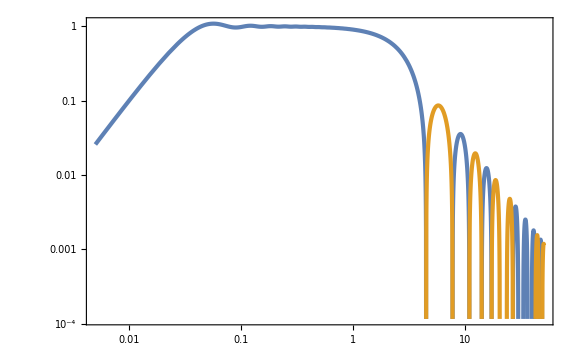

```mathematica
LogLogPlot[{gRTH[z]/.{α->1,β->100,γ->1},-gRTH[z]/.{α->1,β->100,γ->1}},{z,10^-2(2+β)/(2α(1+β))/.{α->1,β->100},10^2(2+β)/(2α(1+β))/.{α->1,β->100}},GridLines->{{(2+β)/(2α(1+β))/.{α->1,β->100}},None}]
```

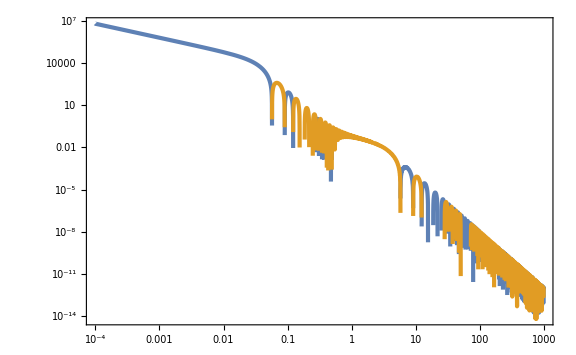

```mathematica
LogLogPlot[{gRTHex[z]/.{β->100},-gRTHex[z]/.{β->100}},{z,10^-4,1000},GridLines->{{(2+β)/(2α(1+β))1/10/.{α->1,β->100}},None}]
```

```mathematica
(1/(α(1+β))+1/α)//Simplify
```

(2+β)/(α+α β)

```mathematica
FindRoot[gRTHex[z]/.{β->100},{z,(2+β)/(2α(1+β))1/10/.{α->1,β->100}},WorkingPrecision->30]
```

{z→0.0570509809077758767039764316614}

```mathematica
zmaxoaRTHgList=ParallelTable[{10^logb,z/.FindRoot[gRTHex[z]/.{β->10^logb},{z,(2+β)/(2α(1+β))1/10/.{α->1,β->10^logb}},WorkingPrecision->30]},{logb,-2,2,1/100}];//AbsoluteTiming
```

{5.37373,Null}

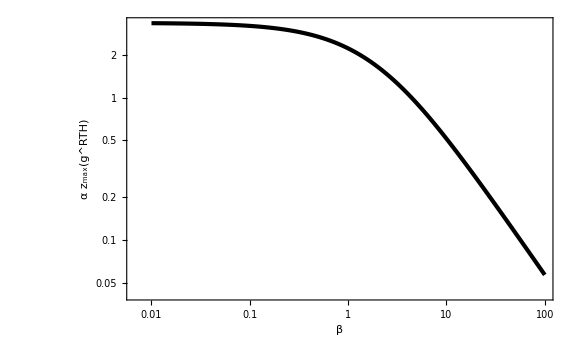

```mathematica
ListLogLogPlot[zmaxoaRTHgList,PlotStyle->{AbsoluteThickness[3],Black},FrameLabel->{β,α Subscript[z, max][g^RTH]}]
```

```mathematica
zmaxRTHgint[α_,β_]=1/α Interpolation[zmaxoaRTHgList][β];
```

```mathematica
zmaxRTHgint[2,1/10]
```

1.59127949979577039141525893936

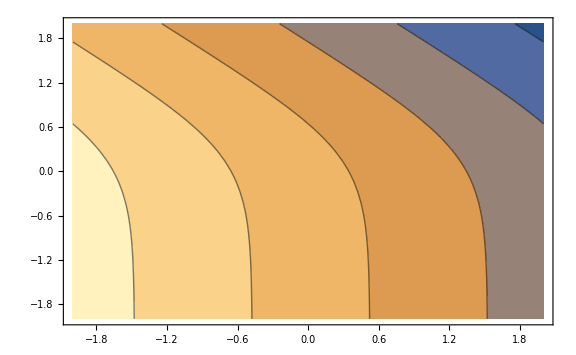

```mathematica
ContourPlot[Log10[zmaxRTHgint[10^loga,10^logb]],{loga,-2,2},{logb,-2,2}]
```

```mathematica
NIntegrate[gRTH[z]/z(Log[z]-Log[zmaxRTHgint[α,β]])^2/.{α->1,β->1/100,γ->1},{z,10^-2 zmaxRTHgint[α,β]/.{α->1,β->1/100},10^2 zmaxRTHgint[α,β]/.{α->1,β->1/100}}]
```

0.00486331

```mathematica
s2RTHgList=ParallelTable[{10^logb,NIntegrate[gRTH[z]/z(Log[z]-Log[zmaxRTHgint[α,β]])^2/.{α->1,β->10^logb,γ->1},{z,10^-2 zmaxRTHgint[α,β]/.{α->1,β->10^logb},10^2 zmaxRTHgint[α,β]/.{α->1,β->10^logb}}]},{logb,-2,2,1/10}];//AbsoluteTiming
```

{0.657086,Null}

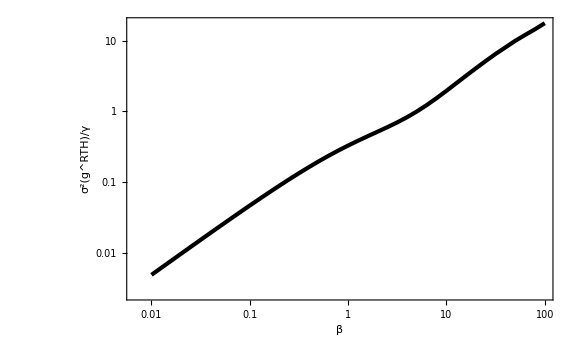

```mathematica
ListLogLogPlot[s2RTHgList,PlotStyle->{AbsoluteThickness[3],Black},FrameLabel->{β,Row[{(σ^2)[g^RTH],"/",γ}]}]
```

```mathematica
s2RTHgint[β_,γ_]=γ Interpolation[s2RTHgList][β];
```

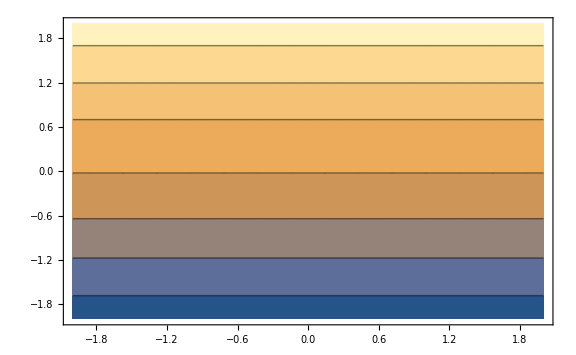

```mathematica
ContourPlot[Log10[s2RTHgint[10^logb,γ]/γ],{loga,-2,2},{logb,-2,2}]
```

#### FTH to FTH

```mathematica
zmaxFTHf
s2FTHf
VFTHf
zmaxFTHg
s2FTHg
VFTHg
```

1

1/4

1/2

(2+β)/(2 α+2 α β)

1/3 γ Log[1+β] (Log[1+β] Log[8 (1+β)]+3 (Log[2]^2+Log[2+β] Log[(2+β)/(4+4 β)]))

γ Log[1+β]

```mathematica
Solve[zmaxFTHf==zmaxFTHg&&s2FTHf==s2FTHg&&VFTHf==VFTHg,{α,β,γ}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1==(2+β)/(2 α+2 α β)&&1/4==1/3 γ Log[1+β] (Log[1+β] Log[8 (1+β)]+3 (Log[2]^2+Log[2+β] Log[(2+β)/(4+4 β)]))&&1/2==γ Log[1+β],{α,β,γ}]

```mathematica
FTHfFTHg=FindRoot[Simplify[zmaxFTHf==zmaxFTHg&&s2FTHf==s2FTHg&&VFTHf==VFTHg],{{α,1},{β,1},{γ,1}}]
```

{α→0.569926,β→6.15037,γ→0.254173}

```mathematica
zmaxFTHf/.FTHfFTHg//N
zmaxFTHg/.FTHfFTHg
s2FTHf/.FTHfFTHg//N
s2FTHg/.FTHfFTHg
VFTHf/.FTHfFTHg//N
VFTHg/.FTHfFTHg
```

1.

1.

0.25

0.25

0.5

0.5

#### FTH to G

```mathematica
zmaxFTHf
s2FTHf
VFTHf
zmaxGg
s2Gg
VGg
```

1

1/4

1/2

(2 √(Log[1+β]/(β (2+β))))/α

1/24 γ Log[1+β] (6 EulerGamma^2+π^2+6 Log[2]^2-4 Log[8] Log[1+β]+8 Log[1+β]^2+6 (2 EulerGamma Log[(1+β)/2]+2 (EulerGamma+Log[(1+β)/2]) Log[(4 Log[1+β])/(β (2+β))]+Log[(4 Log[1+β])/(β (2+β))]^2))

γ Log[1+β]

```mathematica
Solve[zmaxFTHf==zmaxGg&&s2FTHf==s2Gg&&VFTHf==VGg,{α,β,γ}]
```

$Aborted

```mathematica
FTHfGg=FindRoot[Simplify[zmaxFTHf==zmaxGg&&s2FTHf==s2Gg&&VFTHf==VGg],{{α,1},{β,1},{γ,1}}]
```

{α→1.15091,β→0.472832,γ→1.29136}

```mathematica
zmaxFTHf/.FTHfGg//N
zmaxGg/.FTHfGg
s2FTHf/.FTHfGg//N
s2Gg/.FTHfGg
VFTHf/.FTHfGg//N
VGg/.FTHfGg
```

1.

1.

0.25

0.25

0.5

0.5

#### G to FTH

```mathematica
zmaxGf
s2Gf
VGf
zmaxFTHg
s2FTHg
VFTHg
```

√2

1/24 (6 EulerGamma^2+π^2)

1

1/(α √(1+β))

1/12 γ Log[1+β]^3

γ Log[1+β]

```mathematica
GfFTHg=Solve[zmaxGf==zmaxFTHg&&s2Gf==s2FTHg&&VGf==VFTHg,{α,β,γ}][[1]]//Simplify
```

{α→(ⅇ^(-1/2 √(1/2 (6 EulerGamma^2+π^2))))/(√2),β→-1+ⅇ^(√(1/2 (6 EulerGamma^2+π^2))),γ→√(2/(6 EulerGamma^2+π^2))}

```mathematica
zmaxGf/.GfFTHg
zmaxFTHg/.GfFTHg
s2Gf/.GfFTHg
s2FTHg/.GfFTHg
VGf/.GfFTHg
VFTHg/.GfFTHg
```

√2

√2

1/24 (6 EulerGamma^2+π^2)

1/24 (6 EulerGamma^2+π^2)

1

1

#### G to G

```mathematica
zmaxGf
s2Gf
VGf
zmaxGg
s2Gg
VGg
```

√2

1/24 (6 EulerGamma^2+π^2)

1

(2 √(Log[1+β]/(β (2+β))))/α

1/24 γ Log[1+β] (6 EulerGamma^2+π^2+6 Log[2]^2-4 Log[8] Log[1+β]+8 Log[1+β]^2+6 (2 EulerGamma Log[(1+β)/2]+2 (EulerGamma+Log[(1+β)/2]) Log[(4 Log[1+β])/(β (2+β))]+Log[(4 Log[1+β])/(β (2+β))]^2))

γ Log[1+β]

```mathematica
Solve[zmaxGf==zmaxGg&&s2Gf==s2Gg&&VGf==VGg,{α,β,γ}]
```

$Aborted

```mathematica
GfGgγ=Solve[VGf==VGg,γ][[1]]
```

{γ→1/Log[1+β]}

```mathematica
Normal[Series[s2Gg/.GfGgγ,{β,0,0}]]
```

1/24 (6 EulerGamma^2+π^2)

```mathematica
GfGgα=Solve[zmaxGf==Normal[Series[zmaxGg,{β,0,0}]],α][[1]]
```

{α→1}

```mathematica
Normal[Series[Log[1+β]/β,{β,0,0}]]
```

1

```mathematica
zmaxGf
Normal[Series[zmaxGg/.GfGgα,{β,0,0}]]
s2Gf
Normal[Series[s2Gg/.GfGgγ,{β,0,0}]]
VGf
VGg/.GfGgγ
```

√2

√2

1/24 (6 EulerGamma^2+π^2)

1/24 (6 EulerGamma^2+π^2)

1

1

#### FTH to RTH

```mathematica
zmaxFTHf
s2FTHf
VFTHf
VRTHg
```

1

1/4

1/2

γ Log[1+β]

```mathematica
FTHfRTHgγ=Solve[VFTHf==VRTHg,γ][[1]]
```

{γ→1/(2 Log[1+β])}

```mathematica
s2RTHgintβ[β_]=s2RTHgint[β,γ]/.FTHfRTHgγ
```

(InterpolatingFunction[…][β])/(2 Log[1+β])

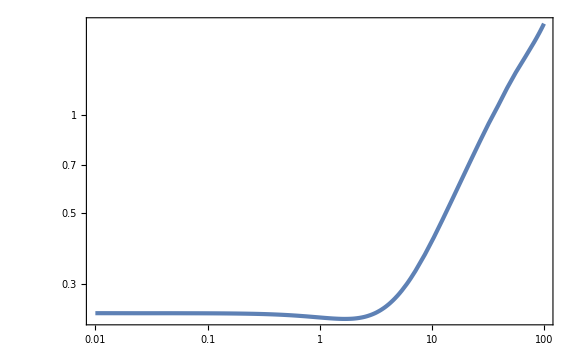

```mathematica
LogLogPlot[s2RTHgintβ[β],{β,10^-2,10^2},GridLines->{None,{s2FTHf}}]
```

```mathematica
FTHfRTHgαβ=FindRoot[zmaxFTHf==zmaxRTHgint[α,β]&&s2FTHf==s2RTHgintβ[β],{{α,1},{β,10}}]
```

{α→1.17208,β→3.51295}

```mathematica
FTHfRTHg=Join[FTHfRTHgαβ,FTHfRTHgγ/.FTHfRTHgαβ]
```

{α→1.17208,β→3.51295,γ→0.331796}

```mathematica
zmaxFTHf/.FTHfRTHg//N
zmaxRTHgint[α,β]/.FTHfRTHg
s2FTHf/.FTHfRTHg//N
s2RTHgint[β,γ]/.FTHfRTHg
VFTHf/.FTHfRTHg//N
VRTHg/.FTHfRTHg
```

1.

1.

0.25

0.25

0.5

0.5

#### G to RTH

```mathematica
zmaxGf
s2Gf
VGf
VRTHg
```

√2

1/24 (6 EulerGamma^2+π^2)

1

γ Log[1+β]

```mathematica
GfRTHg=FindRoot[zmaxGf==zmaxRTHgint[α,β]&&s2Gf==s2RTHgint[β,γ]&&VGf==VRTHg,{{α,1,10^-2,10^2},{β,10},{γ,1}}]
```

{α→0.859234,β→3.32775,γ→0.682572}

```mathematica
zmaxGf/.GfRTHg//N
zmaxRTHgint[α,β]/.GfRTHg
s2Gf/.GfRTHg//N
s2RTHgint[β,γ]/.GfRTHg
VGf/.GfRTHg//N
VRTHg/.GfRTHg
```

1.41421

1.41421

0.494528

0.494528

1.

1.

#### RTH to RTH

```mathematica
zmaxRTHf
s2RTHf
VRTHf
VRTHg
```

2.49691

1.29885746871598765753038333335

1/2 (9-3 √3 ArcCoth[√3])

γ Log[1+β]

```mathematica
RTHfRTHgγ=Solve[VRTHf==VRTHg,γ][[1]]
```

{γ→-(3 (-3+√3 ArcCoth[√3]))/(2 Log[1+β])}

```mathematica
s2RTHgintβ[β_]=s2RTHgint[β,γ]/.RTHfRTHgγ
```

-(3 (-3+√3 ArcCoth[√3]) InterpolatingFunction[…][β])/(2 Log[1+β])

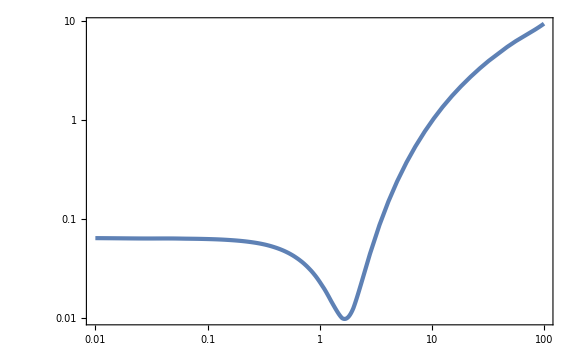

```mathematica
LogLogPlot[Abs[s2RTHgintβ[β]-s2RTHf],{β,10^-2,10^2}]
```

```mathematica
RTHfRTHgβ=FindMinimum[{s2RTHgintβ[β]-s2RTHf,10^-2<β<10^2},{β,1}][[2]]
```

{β→1.66779}

```mathematica
RTHfRTHgα=FindRoot[zmaxRTHf==zmaxRTHgint[α,β]/.RTHfRTHgβ,{α,1}]
```

{α→0.719861}

```mathematica
RTHfRTHg=Join[RTHfRTHgα,RTHfRTHgβ,RTHfRTHgγ/.RTHfRTHgβ]
```

{α→0.719861,β→1.66779,γ→2.84252}

```mathematica
zmaxRTHf/.RTHfRTHg//N
zmaxRTHgint[α,β]/.RTHfRTHg
s2RTHf/.RTHfRTHg//N
s2RTHgint[β,γ]/.RTHfRTHg
VRTHf/.RTHfRTHg//N
VRTHg/.RTHfRTHg
```

2.49691

2.49691

1.29886

1.30871

2.78922

2.78922

#### RTH to G

```mathematica
zmaxRTHf
s2RTHf
VRTHf
zmaxGg
s2Gg
VGg
```

2.49691

1.29885746871598765753038333335

1/2 (9-3 √3 ArcCoth[√3])

(2 √(Log[1+β]/(β (2+β))))/α

1/24 γ Log[1+β] (6 EulerGamma^2+π^2+6 Log[2]^2-4 Log[8] Log[1+β]+8 Log[1+β]^2+6 (2 EulerGamma Log[(1+β)/2]+2 (EulerGamma+Log[(1+β)/2]) Log[(4 Log[1+β])/(β (2+β))]+Log[(4 Log[1+β])/(β (2+β))]^2))

γ Log[1+β]

```mathematica
RTHfGgγ=Solve[VRTHf==VGg,γ][[1]]//Simplify
```

{γ→(9-3 √3 ArcCoth[√3])/(2 Log[1+β])}

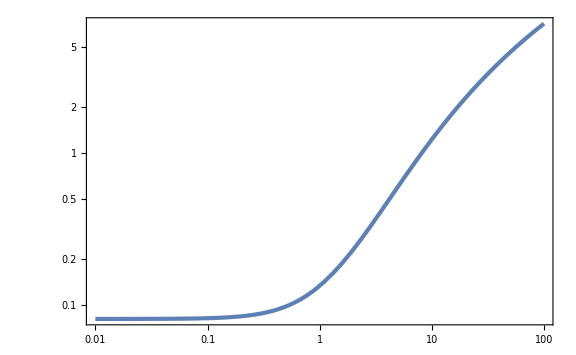

```mathematica
LogLogPlot[Abs[(s2Gg/.RTHfGgγ)-s2RTHf],{β,10^-2,10^2}]
```

```mathematica
RTHfGgα=FindRoot[zmaxRTHf==Normal[Series[zmaxGg,{β,0,0}]],{α,1}][[1]]
```

α→0.566386

```mathematica
zmaxRTHf
Normal[Series[zmaxGg/.RTHfGgα,{β,0,0}]]
s2RTHf
Normal[Series[s2Gg/.RTHfGgγ,{β,0,0}]]//N
VRTHf//N
VGg/.RTHfGgγ//N
```

2.49691

2.49691

1.29885746871598765753038333335

1.37935

2.78922

2.78922

#### RTH to FTH

```mathematica
zmaxRTHf
s2RTHf
VRTHf
zmaxFTHg
s2FTHg
VFTHg
```

2.49691

1.29885746871598765753038333335

1/2 (9-3 √3 ArcCoth[√3])

(2+β)/(2 α+2 α β)

1/3 γ Log[1+β] (Log[1+β] Log[8 (1+β)]+3 (Log[2]^2+Log[2+β] Log[(2+β)/(4+4 β)]))

γ Log[1+β]

```mathematica
Solve[zmaxRTHf==zmaxFTHg&&s2RTHf==s2FTHg&&VRTHf==VFTHg,{α,β,γ}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[2.49691==(2+β)/(2 α+2 α β)&&1.29885746871598765753038333335==1/3 γ Log[1+β] (Log[1+β] Log[8 (1+β)]+3 (Log[2]^2+Log[2+β] Log[(2+β)/(4+4 β)]))&&1/2 (9-3 √3 ArcCoth[√3])==γ Log[1+β],{α,β,γ}]

```mathematica
RTHfFTHg=FindRoot[Simplify[zmaxRTHf==zmaxFTHg&&s2RTHf==s2FTHg&&VRTHf==VFTHg],{{α,1},{β,1},{γ,1}}]
```

{α→0.229819,β→5.77183,γ→1.45821}

```mathematica
zmaxRTHf/.RTHfFTHg//N
zmaxFTHg/.RTHfFTHg
s2RTHf/.RTHfFTHg//N
s2FTHg/.RTHfFTHg
VRTHf/.RTHfFTHg//N
VFTHg/.RTHfFTHg
```

2.49691

2.49691

1.29886

1.29886

2.78922

2.78922

### Setup

```mathematica
B[NN_]=(2π xf)/H-(2π dotx0)/(3 H^2)(1-E^(-3NN));
NB[x_]=InverseFunction[B][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/3 Log[(2 dotx0 π)/(2 dotx0 π+3 H^2 x-6 H π xf)]

```mathematica
H=10^-8;
calPf=1/(2ϵfs)(H/(2π))^2
```

1/(80000000000000000 π^2 ϵfs)

```mathematica
ϵf=ϵfs/.Solve[calPf==10^-3,ϵfs][[1]];ϵf//N
```

1.26651×10^-15

```mathematica
ϵf
```

1/(80000000000000 π^2)

```mathematica
8 10^13
```

80000000000000

```mathematica
ϵi=10^-2;
```

```mathematica
Nf=Log[ϵi/ϵf]/6;Nf//N
```

4.94956

```mathematica
dotx0=dotx0s/.Solve[ϵi==dotx0s^2/(2 H^2),dotx0s][[2]]
dotxf=dotxfs/.Solve[ϵf==dotxfs^2/(2 H^2),dotxfs][[2]]
```

1/(500000000 √2)

1/(200000000000000 √10 π)

```mathematica
5 10^8
2 10^14
```

500000000

200000000000000

```mathematica
xf=(dotx0-dotxf)/(3H);xf//N
```

0.0471404

```mathematica
xf/(H/(2π))//N
```

2.96192×10^7

```mathematica
B[NN_]=(2π xf)/H-(2π dotx0)/(3 H^2)(1-E^(-3NN))//Simplify
P0[x_,NN_]=1/Sqrt[2π NN] Exp[-x^2/(2NN)];
```

10/3 √2 (-√5+2000000 ⅇ^(-3 NN) π)

```mathematica
g1[NN_]=(B[NN]/NN-2B'[NN])P0[B[NN],NN]//Simplify
g2[N1_,N2_]=(2B'[N1]-(B[N1]-B[N2])/(N1-N2))P0[B[N1]-B[N2],N1-N2]//Simplify
```

(ⅇ^(-3 NN-(100 (√5-2000000 ⅇ^(-3 NN) π)^2)/(9 NN)) (-10 √5 ⅇ^(3 NN)+20000000 (π+6 NN π)))/(3 NN^(3/2) √π)

(20000000 ⅇ^(-3 N1-3 N2-(400000000000000 ⅇ^(-6 (N1+N2)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

### Volterra

```mathematica
G1[N1_,N2_]=g2[N1,N2];
```

```mathematica
f1[NN_]:=g1[NN]+NIntegrate[g1[Np]G1[NN,Np],{Np,0,NN}]
```

```mathematica
f1[5]
```

-0.0520354

```mathematica
f1List=ParallelTable[{NN,f1[NN]//Quiet},{NN,4,8,1/10}];//AbsoluteTiming
```

{0.141571,Null}

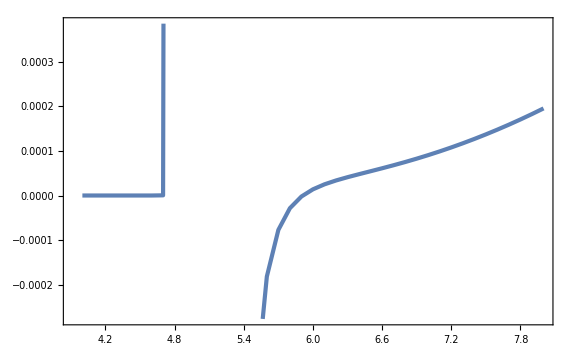

```mathematica
ListPlot[f1List]
```

```mathematica
G2[N1_,N2_]:=NIntegrate[g2[N1,Np]G1[Np,N2],{Np,N2,N1}]
```

```mathematica
G2[7,7-1/100]
```

0.00226944

```mathematica
G2List=Flatten[ParallelTable[{{N1,N2},If[N1<N2,0,G2[N1,N2]//Quiet]},{N1,4,8,1/100},{N2,4,8,1/100}],1];//AbsoluteTiming
```

$Aborted

```mathematica
G2int[N1_,N2_]=Interpolation[Flatten[G2List,1],InterpolationOrder->1][N1,N2];
```

```mathematica
G2List[[1,1]]
```

{{4,4},0.}

```mathematica
Normal[Series[1/Sqrt[x],{x,0,1}]]
```

1/(√x)

### Numerical Integrate

```mathematica
DN=(*1/200*)1/100;
Nmin=0;
Nmax=8;
NList=Table[NN,{NN,Nmin,Nmax,DN}];
Length[NList]
```

801

```mathematica
Delta=ParallelTable[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2[NList[[i]],Np],{Np,NList[[i]]-DN,NList[[i]]}]]//Quiet,N[DN/2 g2[NList[[i]],NList[[j]]-DN/2]]//Quiet]],{i,Length[NList]},{j,Length[NList]}];//AbsoluteTiming
```

{68.9982,Null}

```mathematica
FPFTList=Table[0,{i,Length[NList]}];
```

```mathematica
FPFTList[[1]]={NList[[1]],0};
FPFTList[[2]]={NList[[2]],g1[NList[[2]]](1-Delta[[2,2]])^-1}//Quiet;
For[i=3,i≤Length[FPFTList],i++,
FPFTList[[i]]={NList[[i]],(1-Delta[[i,i]])^-1(g1[NList[[i]]]+ParallelSum[FPFTList[[j,2]](Delta[[i,j]]+Delta[[i,j+1]])//Quiet,{j,2,i-1}])}//Quiet;]//AbsoluteTiming
```

{59.0427,Null}

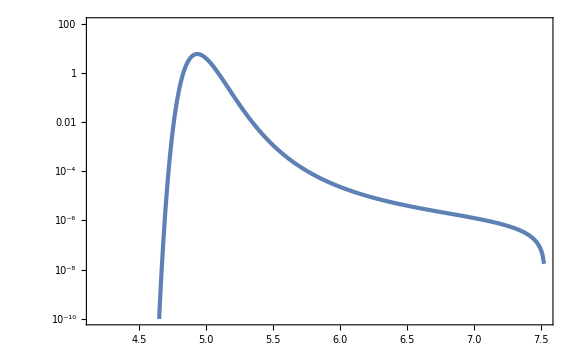

```mathematica
ListLogPlot[FPFTList,PlotRange->{10^-10,100}]
```

```mathematica
FPFTint[NN_]=Interpolation[FPFTList,InterpolationOrder->1][NN];
```

```mathematica
NIntegrate[FPFTint[NN],{NN,Nmin,Nmax}]
Nmean=NIntegrate[NN FPFTint[NN],{NN,Nmin,Nmax}]
varZ=NIntegrate[(NN-Nmean)^2 FPFTint[NN],{NN,Nmin,Nmax}]
Z3=NIntegrate[(NN-Nmean)^3 FPFTint[NN],{NN,Nmin,Nmax}]
Z4=NIntegrate[(NN-Nmean)^4 FPFTint[NN],{NN,Nmin,Nmax}]-3 varZ^2
fNL=5/18 Z3/varZ^2
```

1.00391

4.97525

0.00620451

0.0000656799

0.0000575418

0.47393

```mathematica
FPFTLogCut=Map[{#[[1]],Log[#[[2]]]}&,Select[FPFTList,6<#[[1]]&]];
```

```mathematica
expfit=FindFit[FPFTLogCut,a-b(x-Nmean),{a,b},x]
exp3fit=FindFit[FPFTLogCut,a-b(x-Nmean)-3Log[x-Nmean],{a,b},x]
```

{a→-9.09576-2.73541 ⅈ,b→2.19611-1.71912 ⅈ}

{a→-10.2666-2.73541 ⅈ,b→0.637697-1.71912 ⅈ}

```mathematica
Show[ListLogPlot[FPFTList,PlotRange->{10^-10,100}],LogPlot[{Exp[a] Exp[-b (x-Nmean)]/.expfit,Exp[a] Exp[-b (x-Nmean)]/(x-Nmean)^3/.exp3fit},{x,4.5,8},PlotStyle->{{Dashed,ColorData[97,"ColorList"][[2]]},{Dotted,ColorData[97,"ColorList"][[3]]}}]]
```

-Graphics-

```mathematica
Nf//N
```

4.94956

```mathematica
H3[x_]=x^3-3x;
H4[x_]=x^4-6 x^2+3;
```

```mathematica
Z3fNL=18/5 varZ^2 5/2
```

0.000346464

```mathematica
FPFTGauss[NN_]=1/Sqrt[2π varZ] Exp[(-(NN-Nmean)^2)/(2varZ)];
FPFTEdge[NN_]=(1+1/(3 2)Z3/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]]+1/(4 3 2)Z4/varZ^2 H4[(NN-Nmean)/Sqrt[varZ]])FPFTGauss[NN];
FPFTEdgefNL[NN_]=(1+1/(3 2)Z3fNL/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]])FPFTGauss[NN];
```

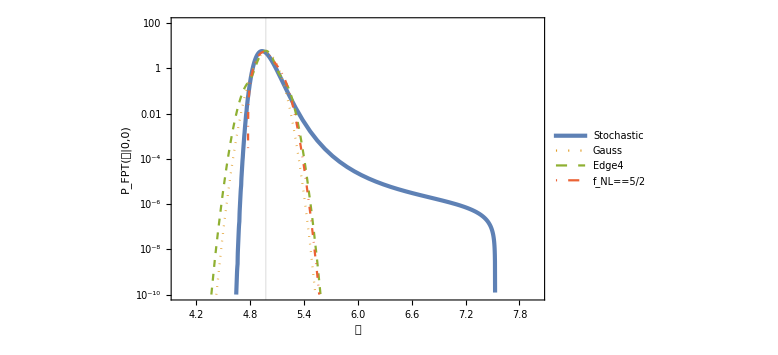

```mathematica
LogPlot[{FPFTint[NN],FPFTGauss[NN],FPFTEdge[NN],FPFTEdgefNL[NN]},{NN,4,8},PlotStyle->{AbsoluteThickness[3],Dotted,Dashed,DotDashed},PlotRange->{10^-10,10^2},FrameLabel->{𝒩,Subscript[P, FPT][𝒩|0,0]},GridLines->{{Nmean},None},PlotLegends->Placed[LineLegend[{"Stochastic","Gauss","Edge4",Subscript[f, NL]==5/2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.75,0.75}]]
```

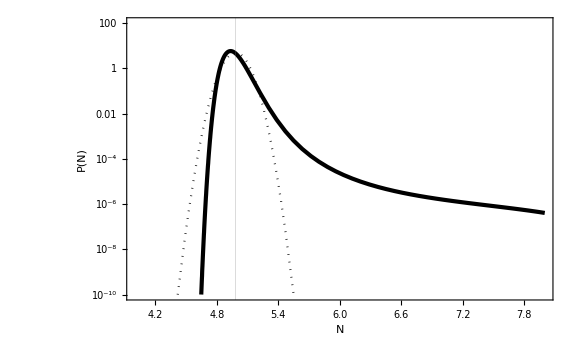

```mathematica
LogPlot[{FPFTint[NN],FPFTGauss[NN]},{NN,4,8},PlotStyle->{{AbsoluteThickness[3],Black},{Dotted,Black}},PlotRange->{10^-10,10^2},FrameLabel->{N,P[N]},GridLines->{{Nmean},None}]
```

```mathematica
FPFTint[Nmean+1]//ScientificForm
```

2.60123×10^-5

```mathematica
Ndrop=NN/.FindRoot[FPFTint[NN]==10^-9,{NN,7.4}]
```

7.5279

General::munfl: Exp[-3672.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2130.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1223.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

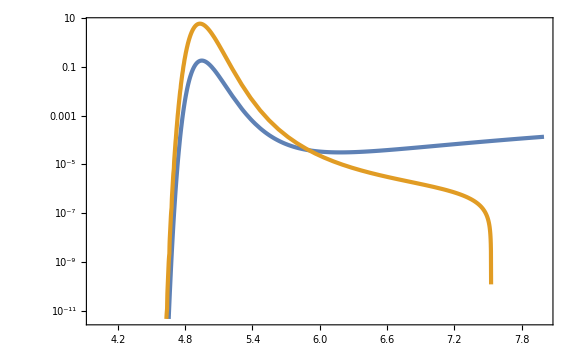

```mathematica
LogPlot[{P0[B[NN],NN],FPFTint[NN]},{NN,4,8}]
```

```mathematica
NIntegrate[FPFTGauss[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTGauss[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTGauss[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTGauss[NN],{NN,Nmin,Nmax}]/Z3
```

1.

1.

1.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.953}. NIntegrate obtained 5.87364×10^-20 and 5.47811×10^-19 for the integral and error estimates.

8.94284×10^-16

```mathematica
NIntegrate[FPFTEdge[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTEdge[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTEdge[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTEdge[NN],{NN,Nmin,Nmax}]/Z3
(NIntegrate[(NN-Nmean)^4 FPFTEdge[NN],{NN,Nmin,Nmax}]-3 varZ^2)/Z4
```

1.

1.

1.

«2 more identical outputs»

```mathematica
B[4]//N
```

171.446

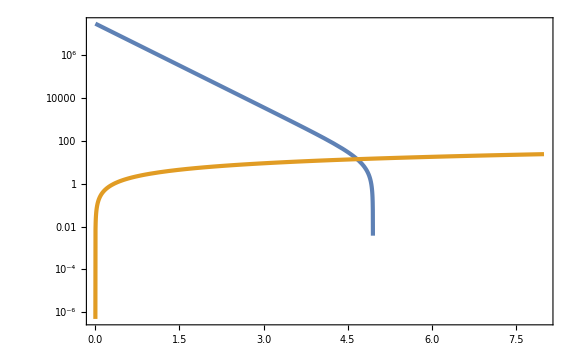

```mathematica
LogPlot[{B[NN],3NN},{NN,Nmin,Nmax}]
```

```mathematica
xmin=-20;
xmax=3NN/.FindRoot[B[NN]==3NN,{NN,4.5}]
```

14.0035

```mathematica
B[8]//N
```

-10.5398

```mathematica
PFP[x_,NN_]:=P0[x,NN]-NIntegrate[FPFTint[Np]P0[x-B[Np],NN-Np],{Np,0,NN}]/;x<B[NN]
PFP[x_,NN_]:=0/;x≥B[NN]
```

```mathematica
PFP[0,5]
```

0

```mathematica
PFPList=Flatten[ParallelTable[{x,NN,PFP[x,NN]//Quiet},{NN,Nmin+1/10,Nmax,1/10},{x,-3 Nmax,xmax,1/10}],1];//AbsoluteTiming
```

{2468.71,Null}

```mathematica
Export["PFPList.dat",PFPList];
```

```mathematica
PFPList=Import["PFPList.dat"]//ToExpression;
```

```mathematica
PFPList[[1]]
```

{-24,1/10,0.}

```mathematica
PFPint[x_,NN_]=Interpolation[PFPList,InterpolationOrder->1][x,NN];
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

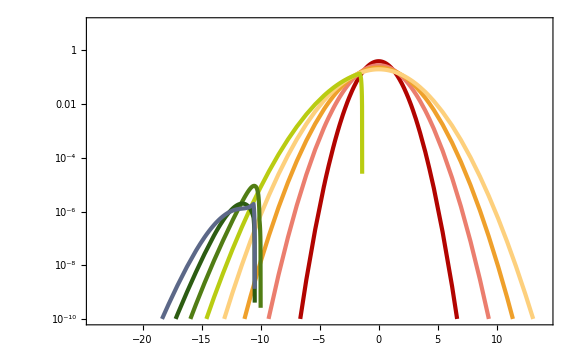

```mathematica
LogPlot[{PFPint[x,1],PFPint[x,2],PFPint[x,3],PFPint[x,4],PFPint[x,5],PFPint[x,6],PFPint[x,7],PFPint[x,8]},{x,-3 Nmax,xmax},PlotRange->{10^-10,10},PlotStyle->Map[{AbsoluteThickness[3],#}&,ColorData[10,"ColorList"]]]
```

```mathematica
NB[x_]=InverseFunction[B][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/3 Log[(20000000 √2 π)/(10 √10+3 x)]

```mathematica
FigPFP=Show[ContourPlot[Log10[Max[PFPint[x,NN],10^-20]],{x,-3Nmax,xmax},{NN,Nmin,Nmax},PlotRange->{{-20,xmax},{Nmin,Nmax},{-10,2}},Contours->11,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 P(z, 𝔑)",Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑}],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

InterpolatingFunction::dmval: Input value {-23.9973,0.000571429} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["../FigPFP.pdf",FigPFP];
```

```mathematica
N1List=Import["c++/Mn_USRzetaR.dat"];(*Select[Import["c++/Mn_USRzetaR.dat"],0≤#[[2]]≤8&];*)
```

```mathematica
Show[ListContourPlot[N1List,PlotRange->{{-15,10},{Nmin,Nmax}},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[⟨N⟩,Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑},Contours->14],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

-Graphics-

```mathematica
N1int[x_,NN_]=Interpolation[N1List][x,NN];
```

```mathematica
N1Contour=Table[7/2i,{i,2 7}];
```

```mathematica
N1Contour//N
```

{3.5,7.,10.5,14.,17.5,21.,24.5,28.,31.5,35.,38.5,42.,45.5,49.}

```mathematica
N1int[-13,1]
```

44.6191

```mathematica
FigN1=Show[ContourPlot[N1int[x,NN],{x,-15,10},{NN,Nmin,Nmax},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[⟨N⟩,Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑},Contours->N1Contour,PlotRange->{-1,49+7/2}],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

-Graphics-

```mathematica
Export["../FigN1.pdf",FigN1];
```

```mathematica
NmFP=N1int[0,0]
```

5.00236

```mathematica
N1x[x_,NN_]=D[N1int[x,NN], x];
```

```mathematica
Show[ContourPlot[N1x[x,NN],{x,-17,10},{NN,0,8},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[⟨N⟩,Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑}],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

-Graphics-

#### Nbw = 3

```mathematica
Nbw=3;
```

```mathematica
NLists=Table[NN,{NN,Nmin,Nbw,DN}];
Length[NLists]
```

301

```mathematica
Bs[NN_,xxs_,NNs_]=(2π xf)/H-xxs-(2π dotx0)/(3 H^2)(1-E^(-3(NN+NNs)))//Simplify;
g1s[NN_,xxs_,NNs_]=Simplify[(Bs[NN,xxs,NNs]/NN-2 D[Bs[NN,xxs,NNs], NN])P0[Bs[NN,xxs,NNs],NN]]
g2s[N1_,N2_,xxs_,NNs_]=Simplify[(2 D[Bs[N1,xxs,NNs], N1]-(Bs[N1,xxs,NNs]-Bs[N2,xxs,NNs])/(N1-N2))P0[Bs[N1,xxs,NNs]-Bs[N2,xxs,NNs],N1-N2]]
```

(ⅇ^(-3 NN-3 NNs-(((10 √10)/3-20000000/3 √2 ⅇ^(-3 (NN+NNs)) π+xxs)^2)/(2 NN)) (20000000 √2 (1+6 NN) π-ⅇ^(3 (NN+NNs)) (10 √10+3 xxs)))/(3 NN^(3/2) √(2 π))

(20000000 ⅇ^(-3 N1-3 N2-3 NNs-(400000000000000 ⅇ^(-6 (N1+N2+NNs)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
PbwList=Flatten[ParallelTable[{xs,Ns,
If[Bs[0,xs,Ns]≤0,0,
Deltas[xs,Ns]=Table[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2s[NLists[[i]],Np,xs,Ns],{Np,NLists[[i]]-DN,NLists[[i]]}]]//Quiet,N[DN/2 g2s[NLists[[i]],NLists[[j]]-DN/2,xs,Ns]]//Quiet]],{i,Length[NLists]},{j,Length[NLists]}];
FPFTLists[1,xs,Ns]=0;
FPFTLists[2,xs,Ns]=g1s[NLists[[2]],xs,Ns](1-Deltas[xs,Ns][[2,2]])^-1//Quiet;
For[i=3,i≤Length[NLists],i++,
FPFTLists[i,xs,Ns]=(1-Deltas[xs,Ns][[i,i]])^-1(g1s[NLists[[i]],xs,Ns]+Sum[FPFTLists[j,xs,Ns](Deltas[xs,Ns][[i,j]]+Deltas[xs,Ns][[i,j+1]])//Quiet,{j,2,i-1}])//Quiet;];
FPFTLists[Length[NLists],xs,Ns]PFPint[xs,Ns]
]},{Ns,Nmin+1/10,Nmax,1/10},{xs,-3 Nmax,xmax,1/10}],1];//AbsoluteTiming
```

General::munfl: 5.5252×10^-308 0.0872845 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.51721×10^-308 2.9749×10^-70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.22084×10^-307 1.33803×10^-69 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{44107.,Null}

```mathematica
48600/3600//N
```

13.5

```mathematica
Export["Pbw.dat",PbwList];
```

```mathematica
PbwList=Import["Pbw.dat"]//ToExpression;
```

```mathematica
ListContourPlot[PbwList]
```

-Graphics-

```mathematica
LogPbwList=Map[{#[[1]],#[[2]],If[#[[3]]≤10^-20,-20,Log10[#[[3]]]]}&,PbwList,1];
```

```mathematica
Show[ListContourPlot[LogPbwList,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 P_bw(z, 𝔑; N_bw = 3)",Right,Rotate[#,-90Degree]&]],PlotRange->{{-17,10},{1.5,8},{-10,2}},Contours->11,FrameLabel->{z,𝔑}],Plot[NB[x],{x,-10 Sqrt[10]/3,12},PlotRange->{4,9},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top]]
```

-Graphics-

```mathematica
Pbwint[x_,NN_]=10^(Interpolation[LogPbwList][x,NN]);
```

```mathematica
FigPbw=Show[ContourPlot[Log10[Pbwint[x,NN]],{x,-17,10},{NN,1.5,8},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 P_bw(z, 𝔑; N_bw = 3)",Right,Rotate[#,-90Degree]&]],PlotRange->{-10,2},Contours->11,FrameLabel->{z,𝔑},WorkingPrecision->30],Plot[NB[x],{x,-10 Sqrt[10]/3,12},PlotRange->{4,9},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top]]
```

-Graphics-

```mathematica
Export["../FigPbw.pdf",FigPbw];
```

```mathematica
FindRoot[zetaR==Ns-NmFP+N1int[xs,Ns]/.{zetaR->3,Ns->2.8},{xs,Min[-1,B[Ns]-1/100]}/.{zetaR->3,Ns->2.8}]
```

InterpolatingFunction::dmval: Input value {-21.,2.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-43.,2.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

{xs→-8.55715}

```mathematica
zmin=-1/5;
zmax=3;
```

```mathematica
xs3List=Flatten[Table[{zetaR,Ns,If[zetaR-Ns+NmFP>0,xs/.FindRoot[zetaR==Ns-NmFP+N1int[xs,Ns],{xs,Min[-1,B[Ns]-1/100]}]//Quiet,B[Ns]]},{zetaR,zmin,zmax,1/100},{Ns,Nmin,Nmax,1/10}],1];//AbsoluteTiming
```

{706.743,Null}

```mathematica
xs3int[zetaR_,Ns_]=Interpolation[xs3List,InterpolationOrder->1][zetaR,Ns];
```

```mathematica
PR3integrandxN[xs_,Ns_]:=Pbwint[xs,Ns]/Abs[N1x[xs,Ns]]/;xs<B[Ns]
PR3integrandxN[xs_,Ns_]:=0/;xs≥B[Ns]
```

```mathematica
PR3integrandxNList=Flatten[ParallelTable[{xs,Ns,PR3integrandxN[xs,Ns]},{xs,xmin,xmax,1/10},{Ns,Nmin+1/10,Nmax,1/10}],1];//AbsoluteTiming
```

{2.80154,Null}

```mathematica
PR3integrandxNLogList=Map[{#[[1]],#[[2]],If[#[[3]]≥10^-20,Log10[#[[3]]],-20]}&,PR3integrandxNList];
```

```mathematica
Show[ListContourPlot[PR3integrandxNLogList,PlotRange->{{-17,10},{1.5,8},{-10,2}},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 (P_bw(z, 𝔑; N_bw = 3))/(|∂⟨𝒩⟩/∂z_*|)",Right,Rotate[#,-90Degree]&]],Contours->11,FrameLabel->{z,𝔑}],ParametricPlot[{{xs3int[-1/5,Ns],Ns},{xs3int[-1/10,Ns],Ns},{xs3int[0,Ns],Ns},{xs3int[1/10,Ns],Ns},{xs3int[1/5,Ns],Ns},{xs3int[1/2,Ns],Ns},{xs3int[1,Ns],Ns},{xs3int[2,Ns],Ns},{xs3int[3,Ns],Ns}},{Ns,Nmin,Nmax},PlotStyle->Map[{AbsoluteThickness[2],Dashed,#}&,ColorData[10,"ColorList"]]],Plot[NB[x],{x,-10 Sqrt[10]/3,12},PlotRange->{4,9},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top]]
```

-Graphics-

```mathematica
PR3integrandxNint[x_,NN_]=10^(Interpolation[PR3integrandxNLogList][x,NN]);
```

```mathematica
FigPR3integrand=Show[ContourPlot[Log10[PR3integrandxNint[x,NN]],{x,-17,10},{NN,1.58,8},PlotRange->{-10,2},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 (P_bw(z, 𝔑; N_bw = 3))/(|∂⟨𝒩⟩/∂z_*|)",Right,Rotate[#,-90Degree]&]],Contours->11,FrameLabel->{z,𝔑}],ParametricPlot[{{xs3int[-1/5,Ns],Ns},{xs3int[-1/10,Ns],Ns},{xs3int[0,Ns],Ns},{xs3int[1/10,Ns],Ns},{xs3int[1/5,Ns],Ns},{xs3int[1/2,Ns],Ns},{xs3int[1,Ns],Ns},{xs3int[2,Ns],Ns},{xs3int[3,Ns],Ns}},{Ns,Nmin,Nmax},PlotStyle->Map[{AbsoluteThickness[2],Dashed,#}&,ColorData[10,"ColorList"]]],Plot[NB[x],{x,-10 Sqrt[10]/3,12},PlotRange->{4,9},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top]]
```

-Graphics-

```mathematica
Export["../FigPR3integrand.pdf",FigPR3integrand];
```

```mathematica
PR3integrand[zetaR_,Ns_]:=Pbwint[xs3int[zetaR,Ns],Ns]/Abs[N1x[xs3int[zetaR,Ns],Ns]]/;zetaR-Ns+NmFP≥0
PR3integrand[zetaR_,Ns_]:=0/;zetaR-Ns+NmFP<0
```

```mathematica
PR3integrand[13/50,4]
```

1.06744×10^-6

```mathematica
Pbwint[xs3int[zetaR,Ns],Ns]/Abs[N1x[xs3int[zetaR,Ns],Ns]]/.{zetaR->0,Ns->4}
```

4.42764×10^-19

```mathematica
PR3[zetaR_]:=NIntegrate[PR3integrand[zetaR,Ns],{Ns,Nmin,Nmax},WorkingPrecision->10]
```

```mathematica
PR3[13/50]
```

0.007080876184

```mathematica
PR3List=Table[{zetaR,PR3[zetaR]//Quiet},{zetaR,zmin,zmax,1/100}];//AbsoluteTiming
```

{5.75255,Null}

```mathematica
PR3LogCut=Map[{#[[1]],Log[#[[2]]]}&,Select[PR3List,#[[1]]>1&]];
```

```mathematica
expPR3fit=FindFit[PR3LogCut,a-b x,{a,b},x]
exp3PR3fit=FindFit[PR3LogCut,a-b x-3 Log[x],{a,b},x]
expnPR3fit=FindFit[PR3LogCut,a-b x-n Log[x],{a,b,n},x]
```

{a→-10.638894258,b→1.6401474324}

{a→-11.854680836,b→0.060210706682}

{a→-12.472980435,b→-0.7432808461,n→4.5256779712}

```mathematica
PR3int[zetaR_]=Interpolation[PR3List][zetaR];
```

```mathematica
NIntegrate[PR3int[zetaR],{zetaR,-1/2,3/2}]
NIntegrate[zetaR PR3int[zetaR],{zetaR,-1/2,3/2}]
var3=NIntegrate[zetaR^2 PR3int[zetaR],{zetaR,-1/2,3/2}]
k33=NIntegrate[zetaR^3 PR3int[zetaR],{zetaR,-1/2,3/2}]
NIntegrate[zetaR^4 PR3int[zetaR],{zetaR,-1/2,3/2}]-3 var3^2
```

InterpolatingFunction::dmvali: The integration endpoint -1/2 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.02227144

0.00893717

-0.00123732

0.00172036

-0.000711607

```mathematica
5/18 k33/var3^2
```

312.143

InterpolatingFunction::dmval: Input value {-0.499929} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

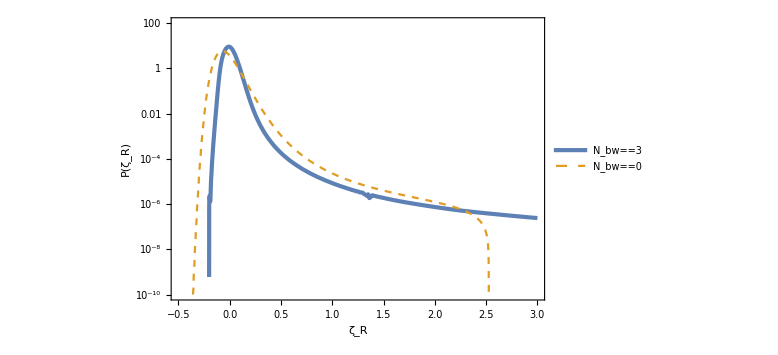

```mathematica
LogPlot[{PR3int[zeta],FPFTint[NmFP+zeta]},{zeta,-1/2,zmax},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted,DotDashed},FrameLabel->{Subscript[ζ, R],P[Subscript[ζ, R]]},PlotLegends->Placed[{Subscript[N, bw]==3,Subscript[N, bw]==0},{0.8,0.8}],PlotRange->{10^-10,10^2}]
```

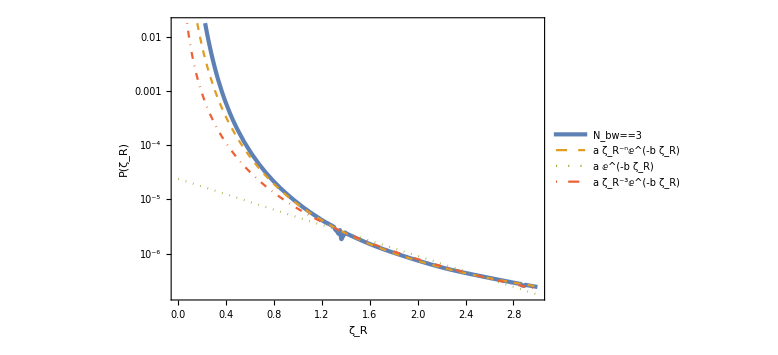

```mathematica
LogPlot[{PR3int[zeta],Exp[a] Exp[-b zeta]/zeta^n/.expnPR3fit,Exp[a]Exp[-b zeta]/.expPR3fit,Exp[a] Exp[-b zeta]/zeta^3/.exp3PR3fit},{zeta,0,zmax},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted,DotDashed},FrameLabel->{Subscript[ζ, R],P[Subscript[ζ, R]]},PlotLegends->Placed[LineLegend[{Subscript[N, bw]==3,Row[{a," ζ_R^-n",Exp[-b Subscript[ζ, R]]}],a Exp[-b Subscript[ζ, R]],Row[{a," ζ_R^-3",,Exp[-b Subscript[ζ, R]]}]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.75,0.7}]]
```

### C++

```mathematica
chiList=Import["c++/chi_USRchiN.dat"];
```

```mathematica
chiList[[1]]
```

{-20,0,0,1}

```mathematica
ITNo=(Length[chiList[[1]]]-2)/2
```

1

```mathematica
chiinvList=Flatten[Table[{chiList[[i,1]],chiList[[i,2]],chiList[[i,1+2j]],1/chiList[[i,2+2j]]},{i,Length[chiList]},{j,ITNo}],1];
```

```mathematica
chiinvList[[1]]
```

{-20,0,0,1}

```mathematica
chiinvint[xs_,Ns_,it_]=Interpolation[chiinvList][xs,Ns,it];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,0}.

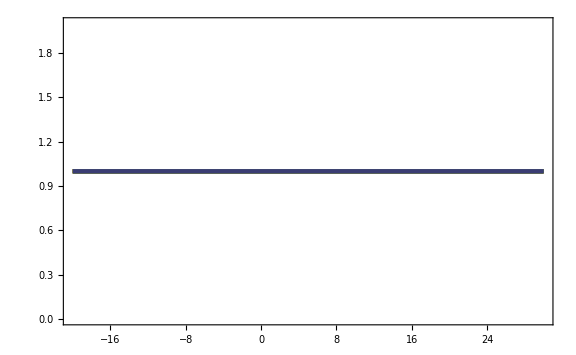

```mathematica
Plot[{chiinvint[xs,0,0],chiinvint[xs,1,0],chiinvint[xs,2,0],chiinvint[xs,3,0],chiinvint[xs,4,0],chiinvint[xs,5,0],chiinvint[xs,6,0],chiinvint[xs,7,0],chiinvint[xs,8,0]},{xs,-20,30},PlotRange->Full,PlotStyle->Map[{AbsoluteThickness[3],#}&,ColorData[10,"ColorList"]]]
```

#### SR

```mathematica
chiList=Import["c++/chi_SRchiN.dat"];
```

```mathematica
chiList[[1]]
```

{0,0.018,429.522}

```mathematica
ITNo=(Length[chiList[[1]]]-1)/2
```

1

```mathematica
chiinvList=Flatten[Table[{chiList[[i,1]],chiList[[i,2j]],(*1/chiList[[i,2j+1]]*)chiList[[i,2j+1]]},{i,Length[chiList]},{j,ITNo}],1];
```

```mathematica
chiinvList[[3]]
```

{0.2,0.018,429.311}

```mathematica
chiinvint[xs_,it_]=Interpolation[chiinvList,InterpolationOrder->2][xs,it];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2,0}.

```mathematica
(π/(2 10.1))^2/2//N
```

0.0120939

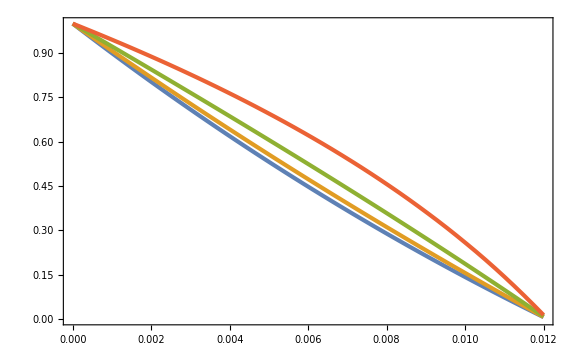

```mathematica
Plot[{chiinvint[0,it],chiinvint[3,it],chiinvint[5,it],chiinvint[7,it]},{it,0,0.012}]
```

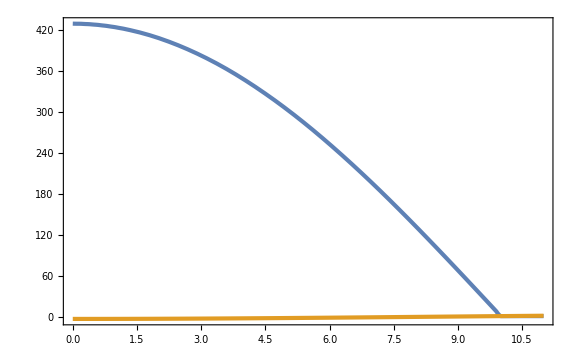

```mathematica
Plot[{chiinvint[xs,0.018],Cos[Sqrt[2 0.018]xs]/Cos[Sqrt[2 0.018]10]},{xs,0,11},PlotRange->Full]
```

```mathematica
chiinvint[2,1]
D[D[chiinvint[xs,1], xs], xs]/.{xs->2}
```

InterpolatingFunction::dmval: Input value {2,1} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.05741

InterpolatingFunction::dmval: Input value {2,1} lies outside the range of data in the interpolating function. Extrapolation will be used.

4.34236×10^-12

```mathematica
xs=-11;
Ns=Nmax;Ns//N
```

8.

```mathematica
Bs[NN_]=(2π xf)/H-xs-(2π dotx0)/(3 H^2)(1-E^(-3(NN+Ns)));
```

```mathematica
Bs[0]//N
```

0.460193

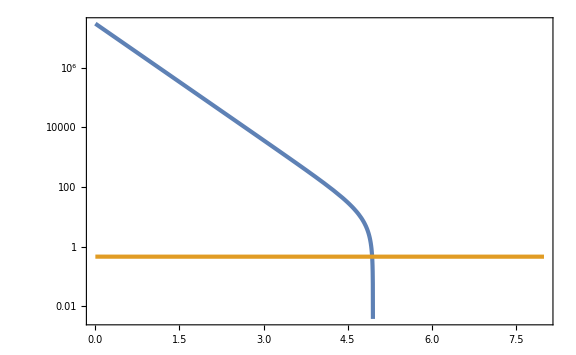

```mathematica
LogPlot[{B[NN],Bs[NN]},{NN,Nmin,Nmax}]
```

```mathematica
g1s[NN_]=(Bs[NN]/NN-2Bs'[NN])P0[Bs[NN],NN]//Simplify
g2s[N1_,N2_]=(2Bs'[N1]-(Bs[N1]-Bs[N2])/(N1-N2))P0[Bs[N1]-Bs[N2],N1-N2]//Simplify
```

1/(3 NN^(3/2) √(2 π))ⅇ^(-(ⅇ^(-6 (8+NN)) (ⅇ^(6 (8+NN)) (2089-660 √10+432 NN+54 NN^2)+40000000 (33 √2-20 √5) ⅇ^(3 (8+NN)) π+800000000000000 π^2))/(18 NN)) ((33-10 √10) ⅇ^(3 (8+NN))+20000000 √2 (1+6 NN) π)

(20000000 ⅇ^(-24-3 N1-3 N2-(400000000000000 ⅇ^(-6 (8+N1+N2)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
NLists=Table[NN,{NN,Nmin,Nbw,DN}];
Length[NLists]
```

301

```mathematica
Deltas=Table[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2s[NLists[[i]],Np],{Np,NLists[[i]]-DN,NLists[[i]]}]]//Quiet,N[DN/2 g2s[NLists[[i]],NLists[[j]]-DN/2]]//Quiet]],{i,Length[NLists]},{j,Length[NLists]}];//AbsoluteTiming
```

{29.9512,Null}

```mathematica
FPFTLists=Table[0,{i,Length[NLists]}];
```

```mathematica
FPFTLists[[1]]={NLists[[1]],0};
FPFTLists[[2]]={NLists[[2]],g1s[NLists[[2]]](1-Deltas[[2,2]])^-1}//Quiet;
For[i=3,i≤Length[FPFTLists],i++,
FPFTLists[[i]]={NLists[[i]],(1-Deltas[[i,i]])^-1(g1s[NLists[[i]]]+Sum[FPFTLists[[j,2]](Deltas[[i,j]]+Deltas[[i,j+1]])//Quiet,{j,2,i-1}])}//Quiet;]//AbsoluteTiming
```

{2.47389,Null}

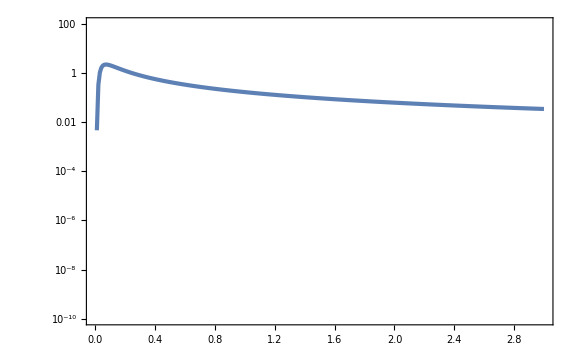

```mathematica
ListLogPlot[FPFTLists,PlotRange->{10^-10,10^2}]
```

```mathematica
Last[FPFTLists]
```

{3,0.0340606}

```mathematica
PFP6List=ParallelTable[{x,PFP[x,6]//Quiet},{x,-3 6,B[6],1/100}];//AbsoluteTiming
```

{66.6572,Null}

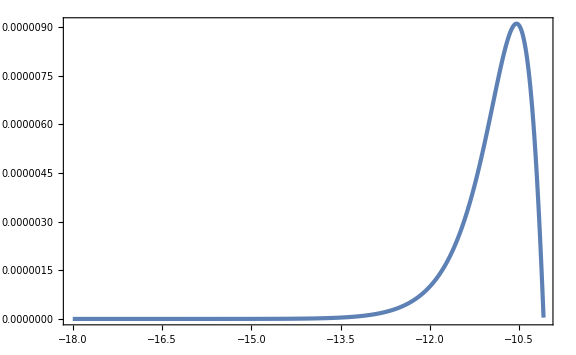

```mathematica
ListPlot[PFP6List,PlotRange->Full]
```

```mathematica
PFP6int[x_]=Interpolation[PFP6List][x];
```

```mathematica
NIntegrate[PFP6int[x],{x,-3 6,B[6]}]
```

InterpolatingFunction::dmvali: The integration endpoint -20000000/3 √2 (1-1/ⅇ^18) π+20000000000000000/3 (1/(500000000 √2)-1/(200000000000000 √10 π)) π in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

9.92386×10^-6

```mathematica
BR[NN_,NR_]=B[NN+NR];
```

```mathematica
g1R[NN_,NR_]=(BR[NN,NR]/NN-2 D[BR[NN,NR], NN])P0[BR[NN,NR],NN]//Simplify
g2R[N1_,N2_,NR_]=(2 D[BR[N1,NR], N1]-(BR[N1,NR]-BR[N2,NR])/(N1-N2))P0[BR[N1,NR]-BR[N2,NR],N1-N2]//Simplify
```

(ⅇ^(-(500+27 NN^2+27 NN NR-400000000 √5 ⅇ^(-3 (NN+NR)) π+400000000000000 ⅇ^(-6 (NN+NR)) π^2)/(9 NN)) (-10 √5 ⅇ^(3 (NN+NR))+20000000 (π+6 NN π)))/(3 NN^(3/2) √π)

(20000000 ⅇ^(-3 N1-3 N2-3 NR-(400000000000000 ⅇ^(-6 (N1+N2+NR)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
DN=1/100;
NRList=Table[NN,{NN,3-NR,11-NR,DN}]/.{NR->3};
Length[NRList]
```

801

```mathematica
DeltaR=ParallelTable[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2R[NRList[[i]],Np,NR]/.{NR->3},{Np,NRList[[i]]-DN,NRList[[i]]}]]//Quiet,N[DN/2 g2R[NRList[[i]],NRList[[j]]-DN/2,NR]/.{NR->3}]//Quiet]],{i,Length[NRList]},{j,Length[NRList]}];//AbsoluteTiming
```

{12.9626,Null}

```mathematica
FPFTRList=Table[0,{i,Length[NRList]}];
```

```mathematica
FPFTRList[[1]]={NRList[[1]],0};
FPFTRList[[2]]={NRList[[2]],g1R[NRList[[2]],NR](1-DeltaR[[2,2]])^-1/.{NR->3}}//Quiet;
For[i=3,i≤Length[FPFTRList],i++,
FPFTRList[[i]]={NRList[[i]],(1-DeltaR[[i,i]])^-1(g1R[NRList[[i]],NR]+ParallelSum[FPFTRList[[j,2]](DeltaR[[i,j]]+DeltaR[[i,j+1]])//Quiet,{j,2,i-1}])/.{NR->3}}//Quiet;]//AbsoluteTiming
```

{30.2999,Null}

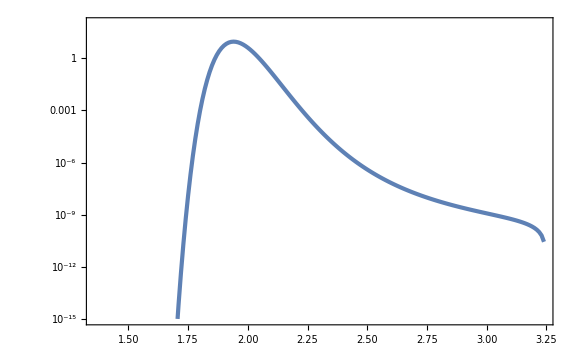

```mathematica
ListLogPlot[FPFTRList,PlotRange->{10^-15,10^2}]
```

```mathematica
NminR=1.5;
NmaxR=4;
```

```mathematica
FPFTRint[NN_]=Interpolation[FPFTRList,InterpolationOrder->1][NN];
```

```mathematica
NIntegrate[FPFTRint[NN],{NN,NminR,NmaxR}]
NmeanR=NIntegrate[NN FPFTRint[NN],{NN,NminR,NmaxR}]
varZR=NIntegrate[(NN-NmeanR)^2 FPFTRint[NN],{NN,NminR,NmaxR}]
Z3R=NIntegrate[(NN-NmeanR)^3 FPFTRint[NN],{NN,NminR,NmaxR}]
Z4R=NIntegrate[(NN-NmeanR)^4 FPFTRint[NN],{NN,NminR,NmaxR}]-3 varZR^2
fNLR=5/18 Z3R/varZR^2
```

1.00363

1.95776

0.00213992

4.4585×10^-6

1.28613×10^-6

0.270454

```mathematica
Nf-NR/.{NR->3}//N
```

1.94956

```mathematica
H3[x_]=x^3-3x;
H4[x_]=x^4-6 x^2+3;
```

```mathematica
Z3RfNL=18/5 varZR^2 5/2
```

0.0000412131

```mathematica
Nmean
```

4.97525

```mathematica
FPFTRGauss[NN_]=1/Sqrt[2π varZR] Exp[(-(NN-NmeanR)^2)/(2varZR)];
FPFTREdge[NN_]=(1+1/(3 2)Z3R/varZR^(3/2)H3[(NN-NmeanR)/Sqrt[varZR]]+1/(4 3 2)Z4R/varZR^2 H4[(NN-NmeanR)/Sqrt[varZR]])FPFTRGauss[NN];
FPFTREdgefNL[NN_]=(1+1/(3 2)Z3RfNL/varZR^(3/2)H3[(NN-NmeanR)/Sqrt[varZR]])FPFTRGauss[NN];
```

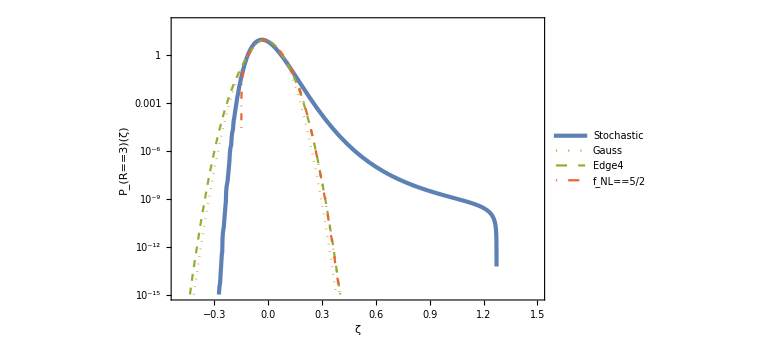

```mathematica
LogPlot[{FPFTRint[zeta+Nmean-NR]/.{NR->3},FPFTRGauss[zeta+Nmean-NR]/.{NR->3},FPFTREdge[zeta+Nmean-NR]/.{NR->3},FPFTREdgefNL[zeta+Nmean-NR]/.{NR->3}},{zeta,-0.5,1.5},PlotStyle->{AbsoluteThickness[3],Dotted,Dashed,DotDashed},PlotRange->{10^-15,10^2},FrameLabel->{ζ,Subscript[P, R==3][ζ]},PlotLegends->Placed[LineLegend[{"Stochastic","Gauss","Edge4",Subscript[f, NL]==5/2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.75,0.75}]]
```

```mathematica
FPFTRint[1+Nmean-NR]/.{NR->3}
```

1.42415×10^-9

```mathematica
varZ/Nmean
varZR/NmeanR
```

0.00124708

0.00109305

```mathematica
PR[zeta_,NR_]:=PFP[B[zeta+Nf],zeta+Nf-NR]
```

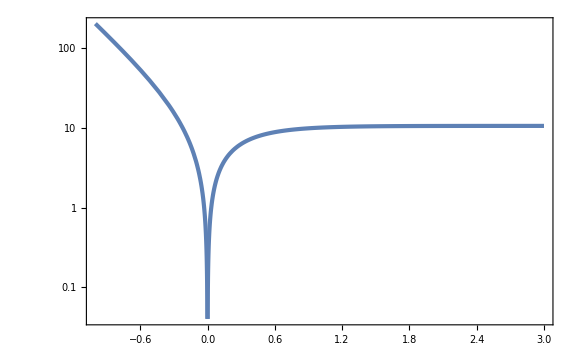

```mathematica
LogPlot[Abs[B[zeta+Nf]],{zeta,-1,3},PlotRange->Full]
```

```mathematica
zetamin[NR_]=NR-Nf;
```

```mathematica
zetamin[3]//N
```

-1.94956

```mathematica
PR[10,3]//Quiet
```

5.24715×10^-6

```mathematica
PR3List=ParallelTable[{zeta,PR[zeta,3]//Quiet},{zeta,-1,3,1/100}];//AbsoluteTiming
```

{20.6656,Null}

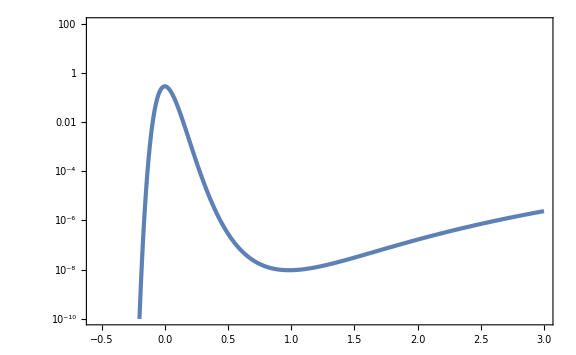

```mathematica
ListLogPlot[PR3List,PlotRange->{10^-10,10^2}]
```

```mathematica
PR3int[zeta_]=Interpolation[PR3List,InterpolationOrder->1][zeta];
```

```mathematica
Norm3=NIntegrate[PR3int[zeta],{zeta,-1,3}]
```

General::munfl: 1.29646×10^-306 (-0.01) is too small to represent as a normalized machine number; precision may be lost.

0.032382

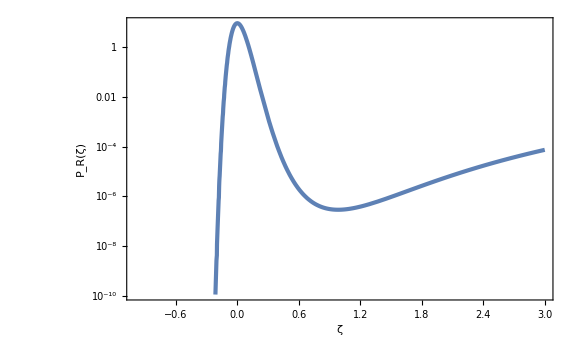

```mathematica
LogPlot[1/Norm3 PR3int[zeta],{zeta,-1,3},FrameLabel->{{Subscript[P, R][ζ],None},{ζ,Subscript[N, bw][R]==3}}]
```

```mathematica
zetamin[0]//N
```

-4.94956

```mathematica
PR[5,0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Np near {Np} = {5.13009}. NIntegrate obtained 0.000473562 and 1.96354×10^-8 for the integral and error estimates.

1.80601×10^-6

```mathematica
PR0List=ParallelTable[{zeta,PR[zeta,0]//Quiet},{zeta,-1,3,1/100}];//AbsoluteTiming
```

{102.387,Null}

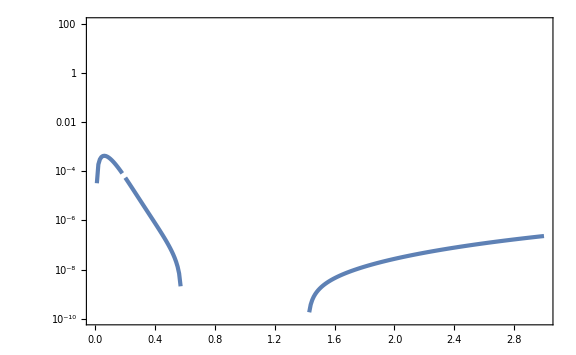

```mathematica
ListLogPlot[PR0List,PlotRange->{10^-10,10^2}]
```

```mathematica
C/Sqrt[S-(S-dS/2)]
1/(Sqrt[2]dS)Integrate[C/Sqrt[S-Sp],{Sp,S-dS,S}]
Integrate[1/Sqrt[S-Sp],{Sp,S-dS,S}]
```

(√2 C)/(√dS)

(√2 C)/(√dS)

2 √dS